```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\000Work\000 Ads ds amp\dS DE

## 1 IBP and DE (for check, not necessay to run)

## Generalize IBP to dS define function

### for a vertex at t (despite theta(t))

```mathematica
Prod[(-t)^(3/2) (1 - I k[i] t) E^[I k[i] t] , {i, iset}]* Prod[(-t)^(3/2) HankelH1[v[j], -k[j] t] , {j, jset}]
```

```mathematica
G[{v1,k1,0},{v2,k2,0},...,{v0,k0}]      ==     t^v0 E^(I k0 t) Product[  HankelH1[   v[i]  , -k[i] t  ] ,{i,n}]
```

### define function

```mathematica
(*listcalc1[list0_, list1_, list2_] := 
 Module[{tmp1 = list1, tmp2 = list2, results, list = list0, i3, i4, list4},
  results = Table[list[[i3]] + If[i3 == tmp1, tmp2, 0], {i3, 1, Length[list]}];
  Return[results];
  ]
listcalc[list0_, list1_, list2_] := 
 Module[{tmp1 = list1, tmp2 = list2, results, list = list0, i3, i4, list4},
  results = list;
  Do[results = listcalc1[results, tmp1[[i3]], tmp2[[i3]]],{i3, 1, Length[tmp1]}];
  Return[results];
  ]*)
```

```mathematica
Corder1="(2 list[[i,1]] + 1)"(*1 for Hankel, 0 for sphere Hankel, -2 for original, 2v+1 for no t^-2 !!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*); 
Ct2="0" (*0 for no t^-2, 1 for others*!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*);

dtGi[expr_,i_]:=Module[{n0,resi,res,tmp,tmp1,tmp2}, list=expr[[1]]; n0=Length[list];

If[i==n0,{tmp=list;tmp[[-1,1]]=list[[-1,1]]-1;resi[n0]=list[[-1,1]]G[tmp]+I list[[-1,2]] G[list];(*apply dt to {v0,k0}*)},
     If[list[[i,3]]==0,{tmp=list;tmp[[i,3]]=1;resi[i]=-tmp[[i,2]](*-k*)G[tmp];},
{tmp=list;tmp1=list;tmp2=list;
tmp[[i,3]]=1;    tmp[[-1,1]]=list[[-1,1]]-1;
tmp1[[i,3]]=0;
tmp2[[i,3]]=0;  tmp2[[-1,1]]=list[[-1,1]]-2;
resi[i]=- ToExpression[Corder1] G[tmp] +  list[[i,2]](* --k=k *)G[tmp1]  +  ToExpression[Ct2] 1/list[[i,2]](*k*)*list[[i,1]]^2(*v^2*)G[tmp2];}]];  
resi[i]];

dtG[expr_]:=Module[{n0,(*list,*)resi,res,tmp,tmp1,tmp2,C}, list=expr[[1]]; n0=Length[list];
tmp=list;(*tau*) tmp[[-1,1]]=list[[-1,1]]-1;resi[n0]=list[[-1,1]]G[tmp]+I list[[-1,2]] G[list](*apply dt to {v0,k0}*);
Do[  If[list[[i,3]]==0,{tmp=list;tmp[[i,3]]=1;resi[i]=-tmp[[i,2]]G[tmp];},
{tmp=list;tmp1=list;tmp2=list;
tmp[[i,3]]=1;    (*tau*) tmp[[-1,1]]=list[[-1,1]]-1;
tmp1[[i,3]]=0;
tmp2[[i,3]]=0;  (*tau*) tmp2[[-1,1]]=list[[-1,1]]-2;
resi[i]=- ToExpression[Corder1] G[tmp]  +  list[[i,2]]G[tmp1]   +   ToExpression[Ct2] 1/list[[i,2]]*list[[i,1]]^2G[tmp2];}];  
,{i,n0-1}];
res=Sum[resi[i],{i,n0}]]



getvset[expr_]:=Module[{n0,list}, list=expr[[1]]; n0=Length[list];Table[list[[i,1]],{i,n0-1}]]
getkset[expr_]:=Module[{n0,list}, list=expr[[1]]; n0=Length[list];Table[list[[i,2]],{i,n0}]]
G2g0[expr_]:=Module[{n0,list}, list=expr[[1]]; n0=Length[list];g[Join[Table[list[[i,3]],{i,n0-1}],{list[[n0,1]]}]]];
G2g[expr_]:=expr/.G[c1_]:>G2g0[G[c1]];
g2G0[expr_]:=Module[{n0,list}, list=expr[[1]]; n0=Length[list];g[Join[Table[{vset[[i]],kset[[i]],list[[i]]},{i,n0-1}],{{list[[n0]],kset[[n0]]}}]]];
g2G[expr_]:=expr/.g[c1_]:>g2G0[g[c1]];(*have vset and kset defined firstly*)

v0list[expr_]:=Table[expr[[i,1]]//Cases[#,_g,Infinity]&//DeleteDuplicates//ReplaceAll[#,{g[c1_]:>c1[[-1]]}]&//ReplaceAll[#,v0->0]&,{i,Length[expr]}];
v0listmin[expr_]:=Table[v0list[expr][[i]]//ReplaceAll[#,{c1___}:>Sequence[c1]]&//Min,{i,Length[Evaluate[v0list[expr]]]}];
v0listmax[expr_]:=Table[v0list[expr][[i]]//ReplaceAll[#,{c1___}:>Sequence[c1]]&//Max,{i,Length[Evaluate[v0list[expr]]]}];

(*----------TODO: dkG----------------------------*)
dkGi[expr_,i_,kj_]:=Module[{n0,(*list,*)resi,res,tmp,tmp1,tmp2,coeff}, list=expr[[1]]; n0=Length[list];coeff=D[list[[i,2]],kj];
If[i==n0,{tmp=list;  tmp[[-1,1]]=list[[-1,1]]+1;  resi[n0]=+I G[tmp](*apply dt to {v0,k0}*);},
     If[list[[i,3]]==0,{tmp=list;tmp[[i,3]]=1;  (*tau*) tmp[[-1,1]]=list[[-1,1]]+1;  resi[i]=- G[tmp];},
{tmp=list;tmp1=list;tmp2=list;
tmp[[i,3]]=1;    
tmp1[[i,3]]=0;  (*tau*) tmp1[[-1,1]]=list[[-1,1]]+1;
tmp2[[i,3]]=0;  (*tau*) tmp2[[-1,1]]=list[[-1,1]]-1;
resi[i]=- ToExpression[Corder1] 1/list[[i,2]]*G[tmp]   +  G[tmp1] + ToExpression[Ct2] 1/list[[i,2]]^2*list[[i,1]]^2G[tmp2];}]];  
resi[i]=coeff*resi[i]    ];

dkG[expr_,kj_]:=Module[{n0,(*list,*)resi,res,tmp,tmp1,tmp2,coefflist,coeffnonzerolist,null}, list=expr[[1]]; n0=Length[list];coefflist=Table[D[list[[i,2]],kj],{i,Length[list]}];(* Print[coefflist];*)
coeffnonzerolist=Table[If[coefflist[[i]]=!=0,i,null],{i,Length[list]}]//Complement[#,{null}]&;
res=Sum[dkGi[expr,i,kj],{i,coeffnonzerolist}]
]
```

```mathematica
repki=Table[ToExpression["k"<>ToString[i]]->Subscript[k,i],{i,0,10}];
repvi=Table[ToExpression["v"<>ToString[i]]->Subscript[ν,i],{i,0,10}];
reptotex[expr_]:=expr/.repki/.repvi(*/.Subscript[a,0]->Subscript[μ,0]*)//ReplaceAll[#,g[{c1___,c2_}]->V[c2,c1]]&
```

```mathematica
sigma3=DiagonalMatrix[{1,-1}]
sigma2={{0,-I},{I,0}}
sigma1={{0,1},{1,0}}
I2=DiagonalMatrix[{1,1}]
T={{1,-I},{-I,1}}/Sqrt[2](*Eigenvectors[{{0,-I},{I,0}}]*)
Tinv=Inverse[T]//Simplify
T.sigma1.Inverse[T]
```

{{1,0},{0,-1}}

{{0,-ⅈ},{ⅈ,0}}

{{0,1},{1,0}}

{{1,0},{0,1}}

{{1/(√2),-ⅈ/(√2)},{-ⅈ/(√2),1/(√2)}}

{{1/(√2),ⅈ/(√2)},{ⅈ/(√2),1/(√2)}}

{{0,1},{1,0}}

```mathematica
T.{{1,0},{0,-1}}.Tinv//Simplify
```

{{0,ⅈ},{-ⅈ,0}}

### dt test

```mathematica
test=G[{{v1,k1,0},{v2,k2,1},{v0,k0}}]+G[{{v1,k1,0},{v2,k2,0},{v0,k0}}]
test/.G[c1_]:>dtG[G[c1]]//Simplify
dtGi[test[[2]],1]
dtGi[test[[2]],2]
dtGi[test[[2]],3]

vset=getvset[test[[1]]]
kset=getkset[test[[1]]]

G2g[test]
g2G[test]
```

G[{{v1,k1,0},{v2,k2,0},{v0,k0}}]+G[{{v1,k1,0},{v2,k2,1},{v0,k0}}]

v0 G[{{v1,k1,0},{v2,k2,0},{-1+v0,k0}}]+ⅈ k0 G[{{v1,k1,0},{v2,k2,0},{v0,k0}}]+k2 G[{{v1,k1,0},{v2,k2,0},{v0,k0}}]+v0 G[{{v1,k1,0},{v2,k2,1},{-1+v0,k0}}]-(1+2 v2) G[{{v1,k1,0},{v2,k2,1},{-1+v0,k0}}]+ⅈ k0 G[{{v1,k1,0},{v2,k2,1},{v0,k0}}]-k2 G[{{v1,k1,0},{v2,k2,1},{v0,k0}}]-k1 G[{{v1,k1,1},{v2,k2,0},{v0,k0}}]-k1 G[{{v1,k1,1},{v2,k2,1},{v0,k0}}]

-k1 G[{{v1,k1,1},{v2,k2,1},{v0,k0}}]

Part::pkspec1: 表达式 i 不能作为部分指定使用.

k2 G[{{v1,k1,0},{v2,k2,0},{v0,k0}}]+G[{{v1,k1,0},{v2,k2,1},{-1+v0,k0}}] (-1-2 {{v1,k1,0},{v2,k2,1},{v0,k0}}⟦i,1⟧)

v0 G[{{v1,k1,0},{v2,k2,1},{-1+v0,k0}}]+ⅈ k0 G[{{v1,k1,0},{v2,k2,1},{v0,k0}}]

{v1,v2}

{k1,k2,k0}

g[{0,0,v0}]+g[{0,1,v0}]

G[{{v1,k1,0},{v2,k2,0},{v0,k0}}]+G[{{v1,k1,0},{v2,k2,1},{v0,k0}}]

### dk test

```mathematica
G[{{v1,k1,0},{v2,k1+k0,0},{v0,k0}}][[1]]
```

{{v1,k1,0},{v2,k0+k1,0},{v0,k0}}

```mathematica
G[{{v1,k1,1},{v2,a k1+k0,0},{v0,k0}}]//dkG[#,k1]&
```

G[{{v1,k1,0},{v2,k0+a k1,0},{1+v0,k0}}]+((-1-2 v1) G[{{v1,k1,1},{v2,k0+a k1,0},{v0,k0}}])/k1-a G[{{v1,k1,1},{v2,k0+a k1,1},{1+v0,k0}}]

## H^1

### IBP

```mathematica
Clear[vset,kset,test,test1,vilist,vilist1]
```

```mathematica
vset=getvset[G[{{v1,k1,0},{v0,k0}}]]
kset=getkset[G[{{v1,k1,0},{v0,k0}}]]
```

{v1}

{k1,k0}

```mathematica
nH=1;
vilist=Table[vi[i],{i,nH}];
vilist1=G[Table[{vi[i],0,1},{i,nH}]]/.G[{c1___}]->Sequence[c1];
glist=Table[g[Join[vilist,{v0}]],Evaluate[vilist1]]
Glist=glist//g2G;
IBPset0=Table[dtG[Glist[[i]]]==0,{i,Length[Glist]}]//G2g
(*test=v0listmin[IBPset0]
IBPset0=Table[IBPset0[[i]]/.v0->v0-test[[i]],{i,Length[IBPset0]}]*)
```

{g[{0,v0}],g[{1,v0}]}

{v0 g[{0,-1+v0}]+ⅈ k0 g[{0,v0}]-k1 g[{1,v0}]==0,k1 g[{0,v0}]+v0 g[{1,-1+v0}]+(-1-2 v1) g[{1,-1+v0}]+ⅈ k0 g[{1,v0}]==0}

```mathematica
IBPset0//InputForm
```

{v0*g[{0, -1 + v0}] + I*k0*g[{0, v0}] - k1*g[{1, v0}] == 0, k1*g[{0, v0}] + v0*g[{1, -1 + v0}] + (-1 - 2*v1)*g[{1, -1 + v0}] + I*k0*g[{1, v0}] == 0}

```mathematica
IBPset0={v0*g[{0, -1 + v0}] + I*k0*g[{0, v0}] - k1*g[{1, v0}] == 0, k1*g[{0, v0}] + v0*g[{1, -1 + v0}] + (-1 - 2*v1)*g[{1, -1 + v0}] + I*k0*g[{1, v0}] == 0}
```

{v0 g[{0,-1+v0}]+ⅈ k0 g[{0,v0}]-k1 g[{1,v0}]==0,k1 g[{0,v0}]+v0 g[{1,-1+v0}]+(-1-2 v1) g[{1,-1+v0}]+ⅈ k0 g[{1,v0}]==0}

#### numerical check ibp

```mathematica
ints=IBPset0//Cases[#,_g,Infinity]&//DeleteDuplicates
ints01=ints/.{g[{0,c2_}]->E^(I k0 t)  t^c2   *       (-k1 t)^(-v1) HankelH1[v1,- k1 t],g[{1,c2_}]->-1/k1   E^(I k0 t) t^c2   *   D[(-k1 t)^(-v1)HankelH1[v1,- k1 t],t]}//Simplify
repN={k0-> -I ,k1->13/5,v0->52/7,v1->7/3}
ints02=ints01/.repN//Simplify;
ints03=Table[NIntegrate[ints02[[i]],{t,-Infinity,0},WorkingPrecision->23],{i,Length[ints02]}];
repint2N=Table[Rule[ints[[i]],ints03[[i]]],{i,Length[ints]}]
```

{g[{0,-1+v0}],g[{0,v0}],g[{1,v0}],g[{1,-1+v0}]}

{ⅇ^(ⅈ k0 t) t^(-1+v0) (-k1 t)^-v1 HankelH1[v1,-k1 t],ⅇ^(ⅈ k0 t) t^v0 (-k1 t)^-v1 HankelH1[v1,-k1 t],-1/2 ⅇ^(ⅈ k0 t) t^v0 (-k1 t)^(-1-v1) (k1 t HankelH1[-1+v1,-k1 t]+2 v1 HankelH1[v1,-k1 t]-k1 t HankelH1[1+v1,-k1 t]),(ⅇ^(ⅈ k0 t) t^(-2+v0) (-k1 t)^-v1 (k1 t HankelH1[-1+v1,-k1 t]+2 v1 HankelH1[v1,-k1 t]-k1 t HankelH1[1+v1,-k1 t]))/(2 k1)}

{k0→-ⅈ,k1→13/5,v0→52/7,v1→7/3}

{g[{0,-1+v0}]→-0.01101047970789667065+0.00586324007241480885 ⅈ,g[{0,v0}]→0.013994851578378176883+0.011128779928724250288 ⅈ,g[{1,v0}]→-0.026075878228680199763282+0.02103241446519998970202 ⅈ,g[{1,-1+v0}]→-0.005852039280463898991228-0.028359786158852536473376 ⅈ}

```mathematica
IBPset0[[;;,1]] /.repint2N/.repN
```

{-2.×10^-20-4.×10^-20 ⅈ,5.×10^-21-3.×10^-21 ⅈ}

```mathematica
IBPset0[[2]]//reptotex//TeXForm
```

k_1 V\left(\nu _0,0\right)+i k_0 V\left(\nu _0,1\right)+\nu _0 V\left(\nu _0-1,1\right)+\left(-2 \nu _1-1\right) V\left(\nu _0-1,1\right)=0

#### solve ibp

```mathematica
(*test={-1,0}*)

v0max=2;v0min=-1
IBPset1=Table[Table[IBPset0[[i]](*/.G[{c1___,{c2_,c3_}}]:>G[c1,{c2-v0+j,c3}]*)/.v0->v0+j,{j,v0min(*+test[[i]]*),v0max}],{i,Length[IBPset0]}]//Transpose//Flatten;
ints=IBPset1//Cases[#,_g,Infinity]&//DeleteDuplicates//ReplaceAll[#,g[{c1___,c2_}]->g[{c2,c1}]]&//Sort//ReplaceAll[#,g[{c1_,c2___}]->g[{c2,c1}]]&
IBPmatrix=Table[Coefficient[IBPset1[[i]][[1]],ints[[j]]],{i,Length[IBPset1]},{j,Length[ints]}]
MatrixRank[IBPmatrix]
MIs={g[{0,v0}],g[{1,v0}](*,g[0,1],g[1,1]*)};
ints1=Complement[ints,MIs];
SolH=Solve[IBPset1,ints1][[1]]//Collect[#,_g]&
SolH[[;;,2]]/.g[c1___]/;MemberQ[MIs,g[c1]]->0  (*Check Master*)
```

-1

{g[{0,-2+v0}],g[{1,-2+v0}],g[{0,-1+v0}],g[{1,-1+v0}],g[{0,v0}],g[{1,v0}],g[{0,1+v0}],g[{1,1+v0}],g[{0,2+v0}],g[{1,2+v0}]}

{{-1+v0,0,ⅈ k0,-k1,0,0,0,0,0,0},{0,-2+v0-2 v1,k1,ⅈ k0,0,0,0,0,0,0},{0,0,v0,0,ⅈ k0,-k1,0,0,0,0},{0,0,0,-1+v0-2 v1,k1,ⅈ k0,0,0,0,0},{0,0,0,0,1+v0,0,ⅈ k0,-k1,0,0},{0,0,0,0,0,v0-2 v1,k1,ⅈ k0,0,0},{0,0,0,0,0,0,2+v0,0,ⅈ k0,-k1},{0,0,0,0,0,0,0,1+v0-2 v1,k1,ⅈ k0}}

8

{g[{0,-2+v0}]→(-k0^2/((-1+v0) v0)-k1^2/((-1+v0) (-1+v0-2 v1))) g[{0,v0}]+(-(ⅈ k0 k1)/((-1+v0) v0)-(ⅈ k0 k1)/((-1+v0) (-1+v0-2 v1))) g[{1,v0}],g[{0,-1+v0}]→-(ⅈ k0 g[{0,v0}])/v0+(k1 g[{1,v0}])/v0,g[{0,1+v0}]→(ⅈ (k0+k0 v0) g[{0,v0}])/(k0^2-k1^2)+(ⅈ (-ⅈ k1 v0+2 ⅈ k1 v1) g[{1,v0}])/(k0^2-k1^2),g[{0,2+v0}]→-((2 k0^2+k1^2+3 k0^2 v0+2 k1^2 v0+k0^2 v0^2+k1^2 v0^2-2 k1^2 v1-2 k1^2 v0 v1) g[{0,v0}])/((k0^2-k1^2)^2)-((-3 ⅈ k0 k1 v0-2 ⅈ k0 k1 v0^2+6 ⅈ k0 k1 v1+6 ⅈ k0 k1 v0 v1-4 ⅈ k0 k1 v1^2) g[{1,v0}])/((k0^2-k1^2)^2),g[{1,-2+v0}]→((ⅈ k0 k1)/(v0 (-2+v0-2 v1))+(ⅈ k0 k1)/((-2+v0-2 v1) (-1+v0-2 v1))) g[{0,v0}]+(-k1^2/(v0 (-2+v0-2 v1))-k0^2/((-2+v0-2 v1) (-1+v0-2 v1))) g[{1,v0}],g[{1,-1+v0}]→-(k1 g[{0,v0}])/(-1+v0-2 v1)-(ⅈ k0 g[{1,v0}])/(-1+v0-2 v1),g[{1,1+v0}]→-((-k1-k1 v0) g[{0,v0}])/(-k0^2+k1^2)-((ⅈ k0 v0-2 ⅈ k0 v1) g[{1,v0}])/(-k0^2+k1^2),g[{1,2+v0}]→-((3 ⅈ k0 k1+5 ⅈ k0 k1 v0+2 ⅈ k0 k1 v0^2-2 ⅈ k0 k1 v1-2 ⅈ k0 k1 v0 v1) g[{0,v0}])/((k0^2-k1^2)^2)-((k0^2 v0+2 k1^2 v0+k0^2 v0^2+k1^2 v0^2-2 k0^2 v1-4 k1^2 v1-4 k0^2 v0 v1-2 k1^2 v0 v1+4 k0^2 v1^2) g[{1,v0}])/((k0^2-k1^2)^2)}

{0,0,0,0,0,0,0,0}

```mathematica
v0min=-1;v0max=2;
IBPset1=Table[Table[IBPset0[[i]]/.v0->v0+j,{j,v0min,v0max(*-test[[i]]*)}],{i,Length[IBPset0]}]//Transpose//Flatten
%//Length
ints=IBPset1//Cases[#,_g,Infinity]&//DeleteDuplicates//ReplaceAll[#,g[{c1___,c2_}]->g[{c2,c1}]]&//Sort//ReplaceAll[#,g[{c1_,c2___}]->g[{c2,c1}]]&
IBPmatrix=Table[Coefficient[IBPset1[[i]][[1]],ints[[j]]],{i,Length[IBPset1]},{j,Length[ints]}](*/.k0->0*);
%//MatrixForm
```

{(-1+v0) g[{0,-2+v0}]+ⅈ k0 g[{0,-1+v0}]-k1 g[{1,-1+v0}]==0,k1 g[{0,-1+v0}]+(-1+v0) g[{1,-2+v0}]+(-1-2 v1) g[{1,-2+v0}]+ⅈ k0 g[{1,-1+v0}]==0,v0 g[{0,-1+v0}]+ⅈ k0 g[{0,v0}]-k1 g[{1,v0}]==0,k1 g[{0,v0}]+v0 g[{1,-1+v0}]+(-1-2 v1) g[{1,-1+v0}]+ⅈ k0 g[{1,v0}]==0,(1+v0) g[{0,v0}]+ⅈ k0 g[{0,1+v0}]-k1 g[{1,1+v0}]==0,k1 g[{0,1+v0}]+(1+v0) g[{1,v0}]+(-1-2 v1) g[{1,v0}]+ⅈ k0 g[{1,1+v0}]==0,(2+v0) g[{0,1+v0}]+ⅈ k0 g[{0,2+v0}]-k1 g[{1,2+v0}]==0,k1 g[{0,2+v0}]+(2+v0) g[{1,1+v0}]+(-1-2 v1) g[{1,1+v0}]+ⅈ k0 g[{1,2+v0}]==0}

8

{g[{0,-2+v0}],g[{1,-2+v0}],g[{0,-1+v0}],g[{1,-1+v0}],g[{0,v0}],g[{1,v0}],g[{0,1+v0}],g[{1,1+v0}],g[{0,2+v0}],g[{1,2+v0}]}

(-1+v0 | 0 | ⅈ k0 | -k1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2+v0-2 v1 | k1 | ⅈ k0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | v0 | 0 | ⅈ k0 | -k1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1+v0-2 v1 | k1 | ⅈ k0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1+v0 | 0 | ⅈ k0 | -k1 | 0 | 0
0 | 0 | 0 | 0 | 0 | v0-2 v1 | k1 | ⅈ k0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2+v0 | 0 | ⅈ k0 | -k1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1+v0-2 v1 | k1 | ⅈ k0)

```mathematica
IBPmatrix1=Table[IBPmatrix[[i]],{i,{3,4,1}}]//MatrixForm//reptotex//TeXForm
```

\left(
\begin{array}{cccccccccc}
 0 & 0 & \nu _0 & 0 & i k_0 & -k_1 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & \nu _0-2 \nu _1-1 & k_1 & i k_0 & 0 & 0 & 0 & 0 \\
 \nu _0-1 & 0 & i k_0 & -k_1 & 0 & 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

```mathematica
ints//reptotex//TeXForm
```

\left\{V\left(\nu _0-2,0\right),V\left(\nu _0-2,1\right),V\left(\nu _0-1,0\right),V\left(\nu _0-1,1\right),V\left(\nu _0,0\right),V\left(\nu
   _0,1\right),V\left(\nu _0+1,0\right),V\left(\nu _0+1,1\right),V\left(\nu _0+2,0\right),V\left(\nu _0+2,1\right)\right\}

```mathematica
H1p=Table[Coefficient[{g[{0,v0+1}],g[{1,v0+1}]}/.SolH,MIs[[i]]],{i,Length[MIs]}]//Transpose
H1m=Table[Coefficient[{g[{0,v0-1}],g[{1,v0-1}]}/.SolH,MIs[[i]]],{i,Length[MIs]}]//Transpose
((H1p//Inverse)/.v0->v0-1)-H1m//Simplify
H1A[v0_]:=Evaluate[H1p]
H1A[v0+1]-(H1p/.v0->v0+1)//Simplify
Inverse[H1A[v0-1]]-H1m//Simplify
```

{{(ⅈ (k0+k0 v0))/(k0^2-k1^2),(ⅈ (-ⅈ k1 v0+2 ⅈ k1 v1))/(k0^2-k1^2)},{-(-k1-k1 v0)/(-k0^2+k1^2),-(ⅈ k0 v0-2 ⅈ k0 v1)/(-k0^2+k1^2)}}

{{-(ⅈ k0)/v0,k1/v0},{-k1/(-1+v0-2 v1),-(ⅈ k0)/(-1+v0-2 v1)}}

{{0,0},{0,0}}

{{0,0},{0,0}}

{{0,0},{0,0}}

```mathematica
H1p/.k0->0//Simplify//reptotex//MatrixForm//TeXForm
```

\left(
\begin{array}{cc}
 0 & -\frac{\nu _0-2 \nu _1}{k_1} \\
 \frac{\nu _0+1}{k_1} & 0 \\
\end{array}
\right)

```mathematica
(H1A[v0+1].H1A[v0](*-H1A[v0]*)//Simplify)-(Table[Coefficient[{g[{0,v0+2}],g[{1,v0+2}]}/.SolH,MIs[[i]]],{i,Length[MIs]}]//Transpose)//Simplify
```

{{0,0},{0,0}}

```mathematica
H1A[v0+1].H1A[v0]//Simplify
```

{{-((1+v0) (k0^2 (2+v0)+k1^2 (1+v0-2 v1)))/((k0^2-k1^2)^2),(ⅈ k0 k1 (2 v0^2+v0 (3-6 v1)+2 v1 (-3+2 v1)))/((k0^2-k1^2)^2)},{-(ⅈ k0 k1 (1+v0) (3+2 v0-2 v1))/((k0^2-k1^2)^2),-((k1^2 (2+v0)+k0^2 (1+v0-2 v1)) (v0-2 v1))/((k0^2-k1^2)^2)}}

### DE H

```mathematica
MIs//g2G
```

{g[{{v1,k1,0},{v0,k0}}],g[{{v1,k1,1},{v0,k0}}]}

```mathematica
dkG[MIs[[1]]//g2G,k1]
```

-G[{{v1,k1,1},{1+v0,k0}}]

```mathematica
(*{Table[dkG[MIs[[i]]//g2G,k1],{i,Length[MIs]}]//G2g}*)test0//reptotex//Transpose//MatrixForm//TeXForm
```

\text{test0}^T

```mathematica
(Table[dkG[MIs[[i]]//g2G,k1],{i,Length[MIs]}]//G2g)/.SolH//Simplify;
test1=Table[Coefficient[%,MIs[[i]]],{i,Length[MIs]}]//Transpose
```

{{(k1 (1+v0))/(k0^2-k1^2),-(ⅈ k0 (v0-2 v1))/(k0^2-k1^2)},{-(ⅈ k0 k1 (1+v0))/(-k0^2 k1+k1^3),(-k1^2 (1+v0)+k0^2 (1+2 v1))/(-k0^2 k1+k1^3)}}

```mathematica
(Table[dkG[MIs[[i]]//g2G,k0],{i,Length[MIs]}]//G2g)/.SolH//Simplify;
test0=Table[Coefficient[%,MIs[[i]]],{i,Length[MIs]}]//Transpose
```

{{-(k0 (1+v0))/(k0^2-k1^2),(ⅈ k1 (v0-2 v1))/(k0^2-k1^2)},{-(ⅈ k1 (1+v0))/(k0^2-k1^2),-(k0 (v0-2 v1))/(k0^2-k1^2)}}

```mathematica
Clear[test3,test4,test5]
```

```mathematica
test1i=test1(*/.v0->v0+1/2+v1*)//Integrate[#,k1]&//Simplify
test0i=test0//Integrate[#,k0]&//Simplify
```

{{-1/2 (1+v0) Log[k0^2-k1^2],-ⅈ (v0-2 v1) ArcTanh[k1/k0]},{ⅈ (1+v0) ArcTanh[k1/k0],-((1+2 v1) Log[k1])-1/2 (v0-2 v1) Log[-k0^2+k1^2]}}

{{-1/2 (1+v0) Log[k0^2-k1^2],-ⅈ (v0-2 v1) ArcTanh[k0/k1]},{ⅈ (1+v0) ArcTanh[k0/k1],-1/2 (v0-2 v1) Log[k0^2-k1^2]}}

```mathematica
test1i//InputForm
```

{{-1/2*((1 + v0)*Log[k0^2 - k1^2]), (-I)*(v0 - 2*v1)*ArcTanh[k1/k0]}, {I*(1 + v0)*ArcTanh[k1/k0], 
  -((1 + 2*v1)*Log[k1]) - ((v0 - 2*v1)*Log[-k0^2 + k1^2])/2}}

```mathematica
test1i/2//Coefficient[#,ArcTanh[k1/k0]]&//reptotex//TeXForm
```

\left(
\begin{array}{cc}
 0 & -\frac{1}{2} i \left(\nu _0-2 \nu _1\right) \\
 \frac{1}{2} i \left(\nu _0+1\right) & 0 \\
\end{array}
\right)

### transformation of DE useless now

```mathematica
trans={{1,0},{a k0/k1,1}}
invtrans=Inverse[trans];
test2=trans.test1.invtrans+D[trans,k1].invtrans//Simplify
test3=test2//Integrate[#,k1]&//Simplify
```

{{1,0},{(a k0)/k1,1}}

{{-(k1^2 (1+v0)+ⅈ a k0^2 (v0-2 v1))/(-k0^2 k1+k1^3),-(ⅈ k0 (v0-2 v1))/(k0^2-k1^2)},{-(ⅈ k0 (k1^2 (1-ⅈ a+v0)+a k0^2 (a (v0-2 v1)-2 ⅈ v1)))/(-k0^2 k1^2+k1^4),(-k1^2 (1+v0)+k0^2 (1+ⅈ a (v0-2 v1)+2 v1))/(-k0^2 k1+k1^3)}}

{{ⅈ a (v0-2 v1) Log[k1]-1/2 (1+v0+ⅈ a v0-2 ⅈ a v1) Log[-k0^2+k1^2],-ⅈ (v0-2 v1) ArcTanh[k1/k0]},{(a k0 (-ⅈ a (v0-2 v1)-2 v1))/k1+(ⅈ+a) (1+v0+ⅈ a v0-2 ⅈ a v1) ArcTanh[k1/k0],(-1-ⅈ a (v0-2 v1)-2 v1) Log[k1]+1/2 ⅈ (ⅈ+a) (v0-2 v1) Log[-k0^2+k1^2]}}

```mathematica
(-v1^2+a^2 (v0+v0^2+v1^2)+ⅈ a (v0+2 v1^2))==0//Solve[#,a]&//ReplaceAll[#,{Power[4v1^2-1,1/2]->I Sqrt[1-4v1^2]}]&
```

{{a→(-ⅈ v0-2 ⅈ v1^2-ⅈ v0 √(1-4 v1^2))/(2 (v0+v0^2+v1^2))},{a→(-ⅈ v0-2 ⅈ v1^2+ⅈ v0 √(1-4 v1^2))/(2 (v0+v0^2+v1^2))}}

```mathematica
trans={{1,0},{(-ⅈ v0-2 ⅈ v1^2-a ⅈ v0 √(1-4 v1^2))/(2 (v0+v0^2+v1^2)) k0/k1,1}}
invtrans=Inverse[trans];
test2=trans.test1.invtrans+D[trans,k1].invtrans//Simplify;
test3=test2//Integrate[#,k1]&//Simplify
test4=trans.test0.invtrans+D[trans,k0].invtrans//Simplify;
test5=test4//Integrate[#,k0]&//Simplify
```

{{1,0},{(k0 (-ⅈ v0-2 ⅈ v1^2-ⅈ a v0 √(1-4 v1^2)))/(2 k1 (v0+v0^2+v1^2)),1}}

{{1/(4 (v0+v0^2+v1^2))(2 (v0-2 v1) (v0+2 v1^2+a v0 √(1-4 v1^2)) Log[k1]-(2 v0^3+2 (1-2 v1) v1^2+v0^2 (5+a √(1-4 v1^2))+v0 (2+4 v1^2-2 v1 (1+a √(1-4 v1^2)))) Log[-k0^2+k1^2]),-ⅈ (v0-2 v1) ArcTanh[k1/k0]},{1/(4 k1 (v0+v0^2+v1^2)^2)ⅈ v0 (k0 (4 v1^3 (1+v1-a √(1-4 v1^2))+v0^2 (1+4 v1+2 a (1+2 v1) √(1-4 v1^2)+a^2 (1-4 v1^2))+2 v0 v1 (1+2 v1+4 v1^2+2 a v1 √(1-4 v1^2)+a^2 (-1+4 v1^2)))+k1 (12 v0^3+4 v0^4+2 v1^2 (-1+2 v1) (-1+a √(1-4 v1^2))-v0^2 (-9+4 v1-8 v1^2+4 a (1+v1) √(1-4 v1^2)+a^2 (1-4 v1^2))-2 v0 (-1+v1-a^2 v1+4 (1+a^2) v1^3+a √(1-4 v1^2)+2 v1^2 (-2+a √(1-4 v1^2)))) ArcTanh[k1/k0]),-(2 (2 v1^2+v0^2 (3+4 v1+a √(1-4 v1^2))+2 v0 (1+v1+v1^2-a v1 √(1-4 v1^2))) Log[k1]+v0 (v0-2 v1) (1+2 v0-a √(1-4 v1^2)) Log[-k0^2+k1^2])/(4 (v0+v0^2+v1^2))}}

{{1/4 (-2 (1+v0)-((v0-2 v1) (v0+2 v1^2+a v0 √(1-4 v1^2)))/(v0+v0^2+v1^2)) Log[k0^2-k1^2],-ⅈ (v0-2 v1) ArcTanh[k0/k1]},{1/(4 (v0+v0^2+v1^2)^2)ⅈ v0 (1/k1 k0 (4 v1^3 (1+v1-a √(1-4 v1^2))+v0^2 (1+4 v1+2 a (1+2 v1) √(1-4 v1^2)+a^2 (1-4 v1^2))+2 v0 v1 (1+2 v1+4 v1^2+2 a v1 √(1-4 v1^2)+a^2 (-1+4 v1^2)))+(12 v0^3+4 v0^4+2 v1^2 (-1+2 v1) (-1+a √(1-4 v1^2))-v0^2 (-9+4 v1-8 v1^2+4 a (1+v1) √(1-4 v1^2)+a^2 (1-4 v1^2))-2 v0 (-1+v1-a^2 v1+4 (1+a^2) v1^3+a √(1-4 v1^2)+2 v1^2 (-2+a √(1-4 v1^2)))) ArcTanh[k0/k1]),-(v0 (v0-2 v1) (1+2 v0-a √(1-4 v1^2)) Log[k0^2-k1^2])/(4 (v0+v0^2+v1^2))}}

```mathematica
trans/.v1^2->-Subscript[ν,1]^2+1/4//Simplify[#,Subscript[ν,1]>0]&//reptotex//MatrixForm//TeXForm
```

\left(
\begin{array}{cc}
 1 & 0 \\
 -\frac{i k_0 \left(4 a \nu _0 \nu _1-4 \nu _1^2+2 \nu _0+1\right)}{k_1 \left(\left(2 \nu _0+1\right){}^2-4 \nu _1^2\right)} & 1 \\
\end{array}
\right)

```mathematica
test6=test3/.v1^2->-mu^2+1/4/.a^2->1//Simplify[#,mu>0]&
test5/.v1^2->-mu^2+1/4/.a^2->1//Simplify[#,mu>0]&//MatrixForm
```

{{(-2 (1-4 mu^2+2 v0+4 a mu v0) (v0-2 v1) Log[k1]+(4 a mu v0 (v0-2 v1)+(1+2 v0) (1+4 v0+2 v0^2-2 v1)+mu^2 (-4-8 v0+8 v1)) Log[-k0^2+k1^2])/(8 mu^2-2 (1+2 v0)^2),-ⅈ (v0-2 v1) ArcTanh[k1/k0]},{1/(k1 (-4 mu^2+(1+2 v0)^2)^2)2 ⅈ v0 (2 k0 (4 v1^3 (1-2 a mu+v1)+4 v0 v1 (1-4 mu^2+v1+2 a mu v1)+v0^2 (1+4 mu^2+4 v1+4 a (mu+2 mu v1)))+k1 (1+8 v0+22 v0^2+24 v0^3+8 v0^4+8 a mu^3 (1+2 v0-2 v1)-4 mu^2 (1+4 v0+6 v0^2-2 v1)-2 v1-8 v0^2 v1-32 v0 v1^3-2 a mu (1+2 v0) (1-2 v1+4 v0 (1+v1))) ArcTanh[k1/k0]),((-4 mu^2 (1+v0)+4 a mu v0 (v0-2 v1)+(1+2 v0) (1+v0 (3+4 v1))) Log[k1]+v0 (1-2 a mu+2 v0) (v0-2 v1) Log[-k0^2+k1^2])/(4 mu^2-(1+2 v0)^2)}}

(((mu^2 (4+8 v0-8 v1)-4 a mu v0 (v0-2 v1)-(1+2 v0) (1+4 v0+2 v0^2-2 v1)) Log[k0^2-k1^2])/(-8 mu^2+2 (1+2 v0)^2) | -ⅈ (v0-2 v1) ArcTanh[k0/k1]
(2 ⅈ v0 (2 k0 (4 v1^3 (1-2 a mu+v1)+4 v0 v1 (1-4 mu^2+v1+2 a mu v1)+v0^2 (1+4 mu^2+4 v1+4 a (mu+2 mu v1)))+k1 (1+8 v0+22 v0^2+24 v0^3+8 v0^4+8 a mu^3 (1+2 v0-2 v1)-4 mu^2 (1+4 v0+6 v0^2-2 v1)-2 v1-8 v0^2 v1-32 v0 v1^3-2 a mu (1+2 v0) (1-2 v1+4 v0 (1+v1))) ArcTanh[k0/k1]))/(k1 (-4 mu^2+(1+2 v0)^2)^2) | -(v0 (1-2 a mu+2 v0) (v0-2 v1) Log[k0^2-k1^2])/(-4 mu^2+(1+2 v0)^2))

```mathematica
test6//InputForm
```

{{(-2*(1 - 4*mu^2 + 2*v0 + 4*a*mu*v0)*(v0 - 2*v1)*Log[k1] + (4*a*mu*v0*(v0 - 2*v1) + (1 + 2*v0)*(1 + 4*v0 + 2*v0^2 - 2*v1) + mu^2*(-4 - 8*v0 + 8*v1))*
     Log[-k0^2 + k1^2])/(8*mu^2 - 2*(1 + 2*v0)^2), (-I)*(v0 - 2*v1)*ArcTanh[k1/k0]}, 
 {((2*I)*v0*(2*k0*(4*v1^3*(1 - 2*a*mu + v1) + 4*v0*v1*(1 - 4*mu^2 + v1 + 2*a*mu*v1) + v0^2*(1 + 4*mu^2 + 4*v1 + 4*a*(mu + 2*mu*v1))) + 
     k1*(1 + 8*v0 + 22*v0^2 + 24*v0^3 + 8*v0^4 + 8*a*mu^3*(1 + 2*v0 - 2*v1) - 4*mu^2*(1 + 4*v0 + 6*v0^2 - 2*v1) - 2*v1 - 8*v0^2*v1 - 32*v0*v1^3 - 
       2*a*mu*(1 + 2*v0)*(1 - 2*v1 + 4*v0*(1 + v1)))*ArcTanh[k1/k0]))/(k1*(-4*mu^2 + (1 + 2*v0)^2)^2), 
  ((-4*mu^2*(1 + v0) + 4*a*mu*v0*(v0 - 2*v1) + (1 + 2*v0)*(1 + v0*(3 + 4*v1)))*Log[k1] + v0*(1 - 2*a*mu + 2*v0)*(v0 - 2*v1)*Log[-k0^2 + k1^2])/
   (4*mu^2 - (1 + 2*v0)^2)}}

```mathematica
test61=test6/.mu->Subscript[ν, 1]//Coefficient[#,ArcTanh[k1/k0]]&//reptotex
test61[[1,2]]//Factor
test61[[2,1]]//Factor
```

{{0,-ⅈ (ν_0-2 ν_1)},{1/(((1+2 ν_0)^2-4 ν_1^2)^2)2 ⅈ ν_0 (1+8 ν_0+22 ν_0^2+24 ν_0^3+8 ν_0^4-2 ν_1-8 ν_0^2 ν_1-4 (1+4 ν_0+6 ν_0^2-2 ν_1) ν_1^2-32 ν_0 ν_1^3+8 a (1+2 ν_0-2 ν_1) ν_1^3-2 a (1+2 ν_0) ν_1 (1-2 ν_1+4 ν_0 (1+ν_1))),0}}

-ⅈ (ν_0-2 ν_1)

1/((1+2 ν_0-2 ν_1)^2 (1+2 ν_0+2 ν_1)^2)2 ⅈ ν_0 (1+8 ν_0+22 ν_0^2+24 ν_0^3+8 ν_0^4-2 ν_1-2 a ν_1-12 a ν_0 ν_1-8 ν_0^2 ν_1-16 a ν_0^2 ν_1-4 ν_1^2+4 a ν_1^2-16 ν_0 ν_1^2-24 ν_0^2 ν_1^2-16 a ν_0^2 ν_1^2+8 ν_1^3+8 a ν_1^3-32 ν_0 ν_1^3+16 a ν_0 ν_1^3-16 a ν_1^4)

```mathematica
ArcTanh[a]//TrigToExp
```

-1/2 Log[1-a]+1/2 Log[1+a]

```mathematica
trans={{(k1^2-k0^2)^(I v1/2+3/4) k1^(-I v1),0},{0,(k1^2-k0^2)^(I v1/2+3/4) k1^(-I v1)}}.{{1,0},{v1/(v0+ⅈ v1)k0/k1,1}}
invtrans=Inverse[trans];
test2=trans.test1.invtrans+D[trans,k1].invtrans//Simplify
test3=test2//Integrate[#,k1]&//Simplify
test3/.v0->1/2/.v1->I (v1(*+1/2*))//Simplify
```

{{k1^(-ⅈ v1) (-k0^2+k1^2)^(3/4+(ⅈ v1)/2),0},{(k0 k1^(-1-ⅈ v1) (-k0^2+k1^2)^(3/4+(ⅈ v1)/2) v1)/(v0+ⅈ v1),k1^(-ⅈ v1) (-k0^2+k1^2)^(3/4+(ⅈ v1)/2)}}

{{-(k1^2 (-1+2 v0) (v0+ⅈ v1)+(2-4 ⅈ) k0^2 v1^2)/(2 k1 (-k0^2+k1^2) (v0+ⅈ v1)),-(ⅈ k0 (v0-2 v1))/(k0^2-k1^2)},{-(k0 v0 ((2+ⅈ) k0^2 v1^2+ⅈ k1^2 (v0+v0^2+2 ⅈ v0 v1-v1 (-ⅈ+v1))))/(k1^2 (-k0^2+k1^2) (v0+ⅈ v1)^2),(-k1^2 (-1+2 v0) (v0+ⅈ v1)+2 k0^2 (v0+(2+2 ⅈ) v0 v1-v1 (-ⅈ+v1)))/(2 k1 (-k0^2+k1^2) (v0+ⅈ v1))}}

{{((4-8 ⅈ) v1^2 Log[k1]+(v0-2 v0^2-2 ⅈ v0 v1+ⅈ v1 (1+(4+2 ⅈ) v1)) Log[-k0^2+k1^2])/(4 (v0+ⅈ v1)),-ⅈ (v0-2 v1) ArcTanh[k1/k0]},{(v0 ((-2-ⅈ) k0 v1^2+k1 (ⅈ v0^2+v0 (ⅈ-2 v1)+v1 (-1+2 v1)) ArcTanh[k1/k0]))/(k1 (v0+ⅈ v1)^2),(-4 (v0+(2+2 ⅈ) v0 v1-v1 (-ⅈ+v1)) Log[k1]+(-2 v0^2+(3 ⅈ-2 v1) v1+v0 (3+(4+2 ⅈ) v1)) Log[-k0^2+k1^2])/(4 (v0+ⅈ v1))}}

{{((1-2 ⅈ) v1^2 (2 Log[k1]-Log[-k0^2+k1^2]))/(-1+2 v1),-1/2 (ⅈ+4 v1) ArcTanh[k1/k0]},{((8+4 ⅈ) k0 v1^2+k1 (3 ⅈ-8 ⅈ v1-8 v1^2) ArcTanh[k1/k0])/(2 k1 (1-2 v1)^2),((1-(4-2 ⅈ) v1+2 v1^2) (2 Log[k1]-Log[-k0^2+k1^2]))/(-2+4 v1)}}

## H^2

```mathematica
Clear[vset,kset,test,test1,vilist,vilist1]
```

```mathematica
vset=getvset[G[{{v1,k1,0},{v2,k2,0},{v0,k0}}]]
kset=getkset[G[{{v1,k1,0},{v2,k2,0},{v0,k0}}]](*/.k0->0*)
```

{v1,v2}

{k1,k2,k0}

```mathematica
nH=2;
vilist=Table[vi[i],{i,nH}];
vilist1=G[Table[{vi[i],0,1},{i,nH}]]/.G[{c1___}]->Sequence[c1];
glist=Table[g[Join[vilist,{v0}]],Evaluate[vilist1]]//Flatten//Sort
Glist=glist//g2G;
IBPset0=Table[dtG[Glist[[i]]]==0,{i,Length[Glist]}]//G2g
Table[IBPset0[[i]]//Cases[#,_g,Infinity]&//DeleteDuplicates//Sort,{i,Length[IBPset0]}]//MatrixForm
test=v0listmin[IBPset0](*+{1,0,0,0}*)
(*IBPset0=Table[IBPset0[[i]]/.v0->v0-test[[i]],{i,Length[IBPset0]}]*)
```

{g[{0,0,v0}],g[{0,1,v0}],g[{1,0,v0}],g[{1,1,v0}]}

{v0 g[{0,0,-1+v0}]+ⅈ k0 g[{0,0,v0}]-k2 g[{0,1,v0}]-k1 g[{1,0,v0}]==0,k2 g[{0,0,v0}]+v0 g[{0,1,-1+v0}]+(-1-2 v2) g[{0,1,-1+v0}]+ⅈ k0 g[{0,1,v0}]-k1 g[{1,1,v0}]==0,k1 g[{0,0,v0}]+v0 g[{1,0,-1+v0}]+(-1-2 v1) g[{1,0,-1+v0}]+ⅈ k0 g[{1,0,v0}]-k2 g[{1,1,v0}]==0,k1 g[{0,1,v0}]+k2 g[{1,0,v0}]+v0 g[{1,1,-1+v0}]+(-1-2 v1) g[{1,1,-1+v0}]+(-1-2 v2) g[{1,1,-1+v0}]+ⅈ k0 g[{1,1,v0}]==0}

(g[{0,0,-1+v0}] | g[{0,0,v0}] | g[{0,1,v0}] | g[{1,0,v0}]
g[{0,0,v0}] | g[{0,1,-1+v0}] | g[{0,1,v0}] | g[{1,1,v0}]
g[{0,0,v0}] | g[{1,0,-1+v0}] | g[{1,0,v0}] | g[{1,1,v0}]
g[{0,1,v0}] | g[{1,0,v0}] | g[{1,1,-1+v0}] | g[{1,1,v0}])

{-1,-1,-1,-1}

```mathematica
(*test={-2,-1,-1,0}*)(*v0listmax[IBPset0]*)
v0max=1(*1*)
v0min=-1(*-1*)
IBPset1=Table[Table[IBPset0[[i]]/.v0->v0+j,{j,v0min(*+test[[i]]*),v0max}],{i,Length[IBPset0]}]//Transpose//Flatten;
ints=IBPset1//Cases[#,_g,Infinity]&//DeleteDuplicates//ReplaceAll[#,g[{c1___,c2_}]->g[{c2,c1}]]&//Sort//ReplaceAll[#,g[{c1_,c2___}]->g[{c2,c1}]]&
IBPmatrix=Table[Coefficient[IBPset1[[i]][[1]],ints[[j]]],{i,Length[IBPset1]},{j,Length[ints]}];
MatrixRank[IBPmatrix]
MIs={g[{0,0,v0}],g[{0,1,v0}],g[{1,0,v0}],g[{1,1,v0}](*,g[{0,0,v0+1}]*)(*,g[{1,0,v0+1}]*)};
ints1=Complement[ints,MIs];
SolH=Solve[IBPset1,ints1][[1]]//Simplify//Collect[#,_g]&;
SolH[[;;,2]]/.g[c1___]/;MemberQ[MIs,g[c1]]->0  (*Check Master*)
```

1

-1

{g[{0,0,-2+v0}],g[{0,1,-2+v0}],g[{1,0,-2+v0}],g[{1,1,-2+v0}],g[{0,0,-1+v0}],g[{0,1,-1+v0}],g[{1,0,-1+v0}],g[{1,1,-1+v0}],g[{0,0,v0}],g[{0,1,v0}],g[{1,0,v0}],g[{1,1,v0}],g[{0,0,1+v0}],g[{0,1,1+v0}],g[{1,0,1+v0}],g[{1,1,1+v0}]}

12

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
IBPmatrix
```

{{-1+v0,0,0,0,ⅈ k0,-k2,-k1,0,0,0,0,0,0,0,0,0},{0,-2+v0-2 v2,0,0,k2,ⅈ k0,0,-k1,0,0,0,0,0,0,0,0},{0,0,-2+v0-2 v1,0,k1,0,ⅈ k0,-k2,0,0,0,0,0,0,0,0},{0,0,0,-3+v0-2 v1-2 v2,0,k1,k2,ⅈ k0,0,0,0,0,0,0,0,0},{0,0,0,0,v0,0,0,0,ⅈ k0,-k2,-k1,0,0,0,0,0},{0,0,0,0,0,-1+v0-2 v2,0,0,k2,ⅈ k0,0,-k1,0,0,0,0},{0,0,0,0,0,0,-1+v0-2 v1,0,k1,0,ⅈ k0,-k2,0,0,0,0},{0,0,0,0,0,0,0,-2+v0-2 v1-2 v2,0,k1,k2,ⅈ k0,0,0,0,0},{0,0,0,0,0,0,0,0,1+v0,0,0,0,ⅈ k0,-k2,-k1,0},{0,0,0,0,0,0,0,0,0,v0-2 v2,0,0,k2,ⅈ k0,0,-k1},{0,0,0,0,0,0,0,0,0,0,v0-2 v1,0,k1,0,ⅈ k0,-k2},{0,0,0,0,0,0,0,0,0,0,0,-1+v0-2 v1-2 v2,0,k1,k2,ⅈ k0}}

```mathematica
test=Table[IBPmatrix[[i,j]],{i,5,8},{j,5,12}]
```

{{v0,0,0,0,ⅈ k0,-k2,-k1,0},{0,-1+v0-2 v2,0,0,k2,ⅈ k0,0,-k1},{0,0,-1+v0-2 v1,0,k1,0,ⅈ k0,-k2},{0,0,0,-2+v0-2 v1-2 v2,0,k1,k2,ⅈ k0}}

```mathematica
test//reptotex(*//MatrixForm*)//TeXForm
```

\left(
\begin{array}{cccccccc}
 \nu _0 & 0 & 0 & 0 & i k_0 & -k_2 & -k_1 & 0 \\
 0 & \nu _0-2 \nu _2-1 & 0 & 0 & k_2 & i k_0 & 0 & -k_1 \\
 0 & 0 & \nu _0-2 \nu _1-1 & 0 & k_1 & 0 & i k_0 & -k_2 \\
 0 & 0 & 0 & \nu _0-2 \nu _1-2 \nu _2-2 & 0 & k_1 & k_2 & i k_0 \\
\end{array}
\right)

```mathematica
(*H1p=Table[Coefficient[MIs/.v0->v0+1/.SolH,MIs[[i]]],{i,Length[MIs]}]//Transpose//Simplify*)
H1m=Table[Coefficient[MIs/.v0->v0-1/.SolH,MIs[[i]]],{i,Length[MIs]}]//Transpose//Simplify
```

{{-(ⅈ k0)/v0,k2/v0,k1/v0,0},{k2/(1-v0+2 v2),(ⅈ k0)/(1-v0+2 v2),0,k1/(-1+v0-2 v2)},{k1/(1-v0+2 v1),0,(ⅈ k0)/(1-v0+2 v1),k2/(-1+v0-2 v1)},{0,-k1/(v0-2 (1+v1+v2)),-k2/(v0-2 (1+v1+v2)),-(ⅈ k0)/(v0-2 (1+v1+v2))}}

```mathematica
H1m//Inverse//Simplify
```

{{(ⅈ k0 (k0^2-k1^2-k2^2) v0)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k2 (k0^2+k1^2-k2^2) (-1+v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k1 (k0^2-k1^2+k2^2) (-1+v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(2 ⅈ k0 k1 k2 (v0-2 (1+v1+v2)))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{-(k2 (k0^2+k1^2-k2^2) v0)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k0 (k0^2-k1^2-k2^2) (-1+v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(2 ⅈ k0 k1 k2 (-1+v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k1 (k0^2-k1^2+k2^2) (v0-2 (1+v1+v2)))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{-(k1 (k0^2-k1^2+k2^2) v0)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(2 ⅈ k0 k1 k2 (-1+v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k0 (k0^2-k1^2-k2^2) (-1+v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k2 (k0^2+k1^2-k2^2) (v0-2 (1+v1+v2)))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{-(2 ⅈ k0 k1 k2 v0)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(k1 (k0^2-k1^2+k2^2) (-1+v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(k2 (k0^2+k1^2-k2^2) (-1+v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k0 (k0^2-k1^2-k2^2) (v0-2 (1+v1+v2)))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))}}

### DE

```mathematica
MIs//g2G
```

{g[{{v1,k1,0},{v2,k2,0},{v0,k0}}],g[{{v1,k1,0},{v2,k2,1},{v0,k0}}],g[{{v1,k1,1},{v2,k2,0},{v0,k0}}],g[{{v1,k1,1},{v2,k2,1},{v0,k0}}]}

```mathematica
dkG[MIs[[1]]//g2G,k0]
```

ⅈ G[{{v1,k1,0},{v2,k2,0},{1+v0,k0}}]

```mathematica
(*{Table[dkG[MIs[[i]]//g2G,k0],{i,Length[MIs]}]//G2g}*)test0//reptotex//Transpose//MatrixForm//TeXForm
```

\left(
\begin{array}{cc}
 -\frac{k_0 \left(\nu _0+1\right)}{k_0^2-k_1^2} & -\frac{i k_1 \left(\nu _0+1\right)}{k_0^2-k_1^2} \\
 \frac{i k_1 \left(\nu _0-2 \nu _1\right)}{k_0^2-k_1^2} & -\frac{k_0 \left(\nu _0-2 \nu _1\right)}{k_0^2-k_1^2} \\
\end{array}
\right)

```mathematica
(Table[dkG[MIs[[i]]//g2G,k2],{i,Length[MIs]}]//G2g)/.SolH//Simplify;
test2=Table[Coefficient[%,MIs[[i]]],{i,Length[MIs]}]//Transpose
```

{{(k2 (k0^2+k1^2-k2^2) (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(ⅈ k0 (k0^2-k1^2-k2^2) (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(2 ⅈ k0 k1 k2 (v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(k1 (k0^2-k1^2+k2^2) (-1+v0-2 v1-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{(ⅈ k0 (k0^2-k1^2-k2^2) (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(-k0^4 (1+2 v2)-(k1^2-k2^2) (-k2^2 (1+v0)+k1^2 (1+2 v2))+k0^2 (k2^2 (2+v0+2 v2)+k1^2 (2+4 v2)))/(k2 (k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))),(k0^2 k1 k2 v0-k1^3 k2 v0+k1 k2^3 v0-2 k0^2 k1 k2 v1+2 k1^3 k2 v1-2 k1 k2^3 v1)/(k2 (k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))),(2 ⅈ k0 k1 k2^2-2 ⅈ k0 k1 k2^2 v0+4 ⅈ k0 k1 k2^2 v1+4 ⅈ k0 k1 k2^2 v2)/(k2 (k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)))},{(2 ⅈ k0 k1 k2 (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k1 (k0^2-k1^2+k2^2) (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k2 (k0^2+k1^2-k2^2) (v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(ⅈ k0 (k0^2-k1^2-k2^2) (-1+v0-2 v1-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{-(k1 (k0^2-k1^2+k2^2) (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(2 ⅈ k0 k1 k2 (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k0 (k0^2-k1^2-k2^2) (v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k2^2 (k0^2+k1^2-k2^2) (-1+v0-2 v1-2 v2)-(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)) (1+2 v2))/(k2 (k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)))}}

```mathematica
(Table[dkG[MIs[[i]]//g2G,k1],{i,Length[MIs]}]//G2g)/.SolH//Simplify;
test1=Table[Coefficient[%,MIs[[i]]],{i,Length[MIs]}]//Transpose
```

{{(k1 (k0^2-k1^2+k2^2) (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(2 ⅈ k0 k1 k2 (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(-ⅈ k0^3 v0+ⅈ k0 k1^2 v0+ⅈ k0 k2^2 v0+2 ⅈ k0^3 v1-2 ⅈ k0 k1^2 v1-2 ⅈ k0 k2^2 v1)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k0^2 k2+k1^2 k2-k2^3-k0^2 k2 v0-k1^2 k2 v0+k2^3 v0+2 k0^2 k2 v1+2 k1^2 k2 v1-2 k2^3 v1+2 k0^2 k2 v2+2 k1^2 k2 v2-2 k2^3 v2)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{(2 ⅈ k0 k1 k2 (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k1 (k0^2-k1^2+k2^2) (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k2 (k0^2+k1^2-k2^2) (v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(ⅈ k0 (k0^2-k1^2-k2^2) (-1+v0-2 v1-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{(ⅈ k0 (k0^2-k1^2-k2^2) (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k2 (k0^2+k1^2-k2^2) (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k1^2 (k0^2-k1^2+k2^2) (v0-2 v1)-(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)) (1+2 v1))/(k1 (k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))),(2 ⅈ k0 k1 k2 (1-v0+2 v1+2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{-(k2 (k0^2+k1^2-k2^2) (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k0 (k0^2-k1^2-k2^2) (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(2 ⅈ k0 k1 k2 (v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-((k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)) (1+2 v1)+k1^2 (k0^2-k1^2+k2^2) (1-v0+2 v1+2 v2))/(k1 (k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)))}}

```mathematica
(Table[dkG[MIs[[i]]//g2G,k0],{i,Length[MIs]}]//G2g)/.SolH//Simplify;
test0=Table[Coefficient[%,MIs[[i]]],{i,Length[MIs]}]//Transpose
```

{{-(k0 (k0^2-k1^2-k2^2) (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k2 (k0^2+k1^2-k2^2) (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k1 (k0^2-k1^2+k2^2) (v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(2 k0 k1 k2 (-1+v0-2 v1-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{-(ⅈ k2 (k0^2+k1^2-k2^2) (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(k0 (k0^2-k1^2-k2^2) (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(2 k0 k1 k2 (v0-2 v1))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k1 (k0^2-k1^2+k2^2) (-1+v0-2 v1-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{-(ⅈ k1 (k0^2-k1^2+k2^2) (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(2 k0 k1 k2 (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(k0^3 v0-k0 k1^2 v0-k0 k2^2 v0-2 k0^3 v1+2 k0 k1^2 v1+2 k0 k2^2 v1)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(ⅈ k0^2 k2+ⅈ k1^2 k2-ⅈ k2^3-ⅈ k0^2 k2 v0-ⅈ k1^2 k2 v0+ⅈ k2^3 v0+2 ⅈ k0^2 k2 v1+2 ⅈ k1^2 k2 v1-2 ⅈ k2^3 v1+2 ⅈ k0^2 k2 v2+2 ⅈ k1^2 k2 v2-2 ⅈ k2^3 v2)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))},{(2 k0 k1 k2 (1+v0))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),-(ⅈ k1 (k0^2-k1^2+k2^2) (v0-2 v2))/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(-ⅈ k0^2 k2 v0-ⅈ k1^2 k2 v0+ⅈ k2^3 v0+2 ⅈ k0^2 k2 v1+2 ⅈ k1^2 k2 v1-2 ⅈ k2^3 v1)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(k0^3-k0 k1^2-k0 k2^2-k0^3 v0+k0 k1^2 v0+k0 k2^2 v0+2 k0^3 v1-2 k0 k1^2 v1-2 k0 k2^2 v1+2 k0^3 v2-2 k0 k1^2 v2-2 k0 k2^2 v2)/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))}}

```mathematica
test1i=test1(*/.v0->v0+1/2+v1*)//Integrate[#,k1]&//Simplify[#,k0>k1>k2>0]&
test2i=test2(*/.v0->v0+1/2+v1*)//Integrate[#,k2]&//Simplify[#,k0>k1>k2>0]&
test0i=test0//Integrate[#,k0]&//Simplify[#,k0>k1>k2>0]&
```

{{-1/4 (1+v0) Log[k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)],1/2 ⅈ (v0-2 v2) (ArcTanh[k0/(k1-k2)]-ArcTanh[k0/(k1+k2)]),-1/2 ⅈ (v0-2 v1) (ArcTanh[k0/(k1-k2)]+ArcTanh[k0/(k1+k2)]),1/2 (-1+v0-2 v1-2 v2) ArcTanh[(-k0^2+k1^2+k2^2)/(2 k1 k2)]},{-1/2 ⅈ (1+v0) (ArcTanh[k0/(k1-k2)]-ArcTanh[k0/(k1+k2)]),-1/4 (v0-2 v2) Log[k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)],-1/2 (v0-2 v1) ArcTanh[(-k0^2+k1^2+k2^2)/(2 k1 k2)],-1/2 ⅈ (-1+v0-2 v1-2 v2) (ArcTanh[k0/(k1-k2)]+ArcTanh[k0/(k1+k2)])},{1/2 ⅈ (1+v0) (ArcTanh[k0/(k1-k2)]+ArcTanh[k0/(k1+k2)]),-1/2 (v0-2 v2) ArcTanh[(-k0^2+k1^2+k2^2)/(2 k1 k2)],-1/4 (v0-2 v1) Log[k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)],1/2 ⅈ (-1+v0-2 v1-2 v2) (ArcTanh[k0/(k1-k2)]-ArcTanh[k0/(k1+k2)])},{1/2 (1+v0) ArcTanh[(-k0^2+k1^2+k2^2)/(2 k1 k2)],1/2 ⅈ (v0-2 v2) (ArcTanh[k0/(k1-k2)]+ArcTanh[k0/(k1+k2)]),-1/2 ⅈ (v0-2 v1) (ArcTanh[k0/(k1-k2)]-ArcTanh[k0/(k1+k2)]),-1/4 (-1+v0-2 v1-2 v2) Log[k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)]}}

```mathematica
D[test1i-test2i//Simplify,k1]//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,-(1+2 v1)/k1,0},{0,0,0,-(1+2 v1)/k1}}

```mathematica
test0-Omegek0//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
sigma2
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
T.sigma3.Tinv
```

{{0,ⅈ},{-ⅈ,0}}

## H^n matrix form

```mathematica
Clear[M1i,M2i,M0i,I2]
M1i[i_]:={{0,0},{0,-2ToExpression["v"<>ToString[i]]-1}}
M0i[i_]:=-I ToExpression["k"<>ToString[i]] sigma2
M1ti[i_]:=T.{{0,0},{0,-2ToExpression["v"<>ToString[i]]-1}}.Tinv
M0ti[i_]:=-I ToExpression["k"<>ToString[i]] sigma3
I2=IdentityMatrix[2];
f[I2,M1i[1],M0i[1],M1ti[1],M0ti[1]]
```

f[{{1,0},{0,1}},{{0,0},{0,-1-2 v1}},{{0,-k1},{k1,0}},{{1/2 (-1-2 v1),-1/2 ⅈ (-1-2 v1)},{1/2 ⅈ (-1-2 v1),1/2 (-1-2 v1)}},{{-ⅈ k1,0},{0,ⅈ k1}}]

```mathematica
M0=KroneckerProduct[M0i[1],I2]+KroneckerProduct[I2,M0i[2]]+I k0 KroneckerProduct[I2,I2]
M1=KroneckerProduct[M1i[1],I2]+KroneckerProduct[I2,M1i[2]]+v0 KroneckerProduct[I2,I2]
Mt0=KroneckerProduct[M0ti[1],I2]+KroneckerProduct[I2,M0ti[2]]+I k0 KroneckerProduct[I2,I2]
Mt1=KroneckerProduct[M1ti[1],I2]+KroneckerProduct[I2,M1ti[2]]+v0 KroneckerProduct[I2,I2]//Simplify
```

{{ⅈ k0,-k2,-k1,0},{k2,ⅈ k0,0,-k1},{k1,0,ⅈ k0,-k2},{0,k1,k2,ⅈ k0}}

{{v0,0,0,0},{0,-1+v0-2 v2,0,0},{0,0,-1+v0-2 v1,0},{0,0,0,-2+v0-2 v1-2 v2}}

{{ⅈ k0-ⅈ k1-ⅈ k2,0,0,0},{0,ⅈ k0-ⅈ k1+ⅈ k2,0,0},{0,0,ⅈ k0+ⅈ k1-ⅈ k2,0},{0,0,0,ⅈ k0+ⅈ k1+ⅈ k2}}

{{-1+v0-v1-v2,1/2 ⅈ (1+2 v2),1/2 ⅈ (1+2 v1),0},{-1/2 ⅈ (1+2 v2),-1+v0-v1-v2,0,1/2 ⅈ (1+2 v1)},{-1/2 ⅈ (1+2 v1),0,-1+v0-v1-v2,1/2 ⅈ (1+2 v2)},{0,-1/2 ⅈ (1+2 v1),-1/2 ⅈ (1+2 v2),-1+v0-v1-v2}}

```mathematica
Mt0/I//Simplify//reptotex//TeXForm
```

\left(
\begin{array}{cccc}
 k_0-k_1-k_2 & 0 & 0 & 0 \\
 0 & k_0-k_1+k_2 & 0 & 0 \\
 0 & 0 & k_0+k_1-k_2 & 0 \\
 0 & 0 & 0 & k_0+k_1+k_2 \\
\end{array}
\right)

## H^3

```mathematica
Clear[vset,kset,test,test1,vilist,vilist1]
```

```mathematica
vset=getvset[G[{{v1,k1,0},{v2,k2,0},{v3,k3,0},{v0,k0}}]]
kset=getkset[G[{{v1,k1,0},{v2,k2,0},{v3,k3,0},{v0,k0}}]](*/.k0->0*)
```

{v1,v2,v3}

{k1,k2,k3,k0}

```mathematica
nH=3;
vilist=Table[vi[i],{i,nH}];
vilist1=G[Table[{vi[i],0,1},{i,nH}]]/.G[{c1___}]->Sequence[c1];
glist=Table[g[Join[vilist,{v0}]],Evaluate[vilist1]]//Flatten//Sort
Glist=glist//g2G;
IBPset0=Table[dtG[Glist[[i]]]==0,{i,Length[Glist]}]//G2g
Table[IBPset0[[i]]//Cases[#,_g,Infinity]&//DeleteDuplicates//Sort,{i,Length[IBPset0]}]//MatrixForm
test=v0listmin[IBPset0](*+{1,0,0,0}*)
(*IBPset0=Table[IBPset0[[i]]/.v0->v0-test[[i]],{i,Length[IBPset0]}]*)
```

{g[{0,0,0,v0}],g[{0,0,1,v0}],g[{0,1,0,v0}],g[{0,1,1,v0}],g[{1,0,0,v0}],g[{1,0,1,v0}],g[{1,1,0,v0}],g[{1,1,1,v0}]}

{v0 g[{0,0,0,-1+v0}]+ⅈ k0 g[{0,0,0,v0}]-k3 g[{0,0,1,v0}]-k2 g[{0,1,0,v0}]-k1 g[{1,0,0,v0}]==0,k3 g[{0,0,0,v0}]+v0 g[{0,0,1,-1+v0}]+(-1-2 v3) g[{0,0,1,-1+v0}]+ⅈ k0 g[{0,0,1,v0}]-k2 g[{0,1,1,v0}]-k1 g[{1,0,1,v0}]==0,k2 g[{0,0,0,v0}]+v0 g[{0,1,0,-1+v0}]+(-1-2 v2) g[{0,1,0,-1+v0}]+ⅈ k0 g[{0,1,0,v0}]-k3 g[{0,1,1,v0}]-k1 g[{1,1,0,v0}]==0,k2 g[{0,0,1,v0}]+k3 g[{0,1,0,v0}]+v0 g[{0,1,1,-1+v0}]+(-1-2 v2) g[{0,1,1,-1+v0}]+(-1-2 v3) g[{0,1,1,-1+v0}]+ⅈ k0 g[{0,1,1,v0}]-k1 g[{1,1,1,v0}]==0,k1 g[{0,0,0,v0}]+v0 g[{1,0,0,-1+v0}]+(-1-2 v1) g[{1,0,0,-1+v0}]+ⅈ k0 g[{1,0,0,v0}]-k3 g[{1,0,1,v0}]-k2 g[{1,1,0,v0}]==0,k1 g[{0,0,1,v0}]+k3 g[{1,0,0,v0}]+v0 g[{1,0,1,-1+v0}]+(-1-2 v1) g[{1,0,1,-1+v0}]+(-1-2 v3) g[{1,0,1,-1+v0}]+ⅈ k0 g[{1,0,1,v0}]-k2 g[{1,1,1,v0}]==0,k1 g[{0,1,0,v0}]+k2 g[{1,0,0,v0}]+v0 g[{1,1,0,-1+v0}]+(-1-2 v1) g[{1,1,0,-1+v0}]+(-1-2 v2) g[{1,1,0,-1+v0}]+ⅈ k0 g[{1,1,0,v0}]-k3 g[{1,1,1,v0}]==0,k1 g[{0,1,1,v0}]+k2 g[{1,0,1,v0}]+k3 g[{1,1,0,v0}]+v0 g[{1,1,1,-1+v0}]+(-1-2 v1) g[{1,1,1,-1+v0}]+(-1-2 v2) g[{1,1,1,-1+v0}]+(-1-2 v3) g[{1,1,1,-1+v0}]+ⅈ k0 g[{1,1,1,v0}]==0}

(g[{0,0,0,-1+v0}] | g[{0,0,0,v0}] | g[{0,0,1,v0}] | g[{0,1,0,v0}] | g[{1,0,0,v0}]
g[{0,0,0,v0}] | g[{0,0,1,-1+v0}] | g[{0,0,1,v0}] | g[{0,1,1,v0}] | g[{1,0,1,v0}]
g[{0,0,0,v0}] | g[{0,1,0,-1+v0}] | g[{0,1,0,v0}] | g[{0,1,1,v0}] | g[{1,1,0,v0}]
g[{0,0,1,v0}] | g[{0,1,0,v0}] | g[{0,1,1,-1+v0}] | g[{0,1,1,v0}] | g[{1,1,1,v0}]
g[{0,0,0,v0}] | g[{1,0,0,-1+v0}] | g[{1,0,0,v0}] | g[{1,0,1,v0}] | g[{1,1,0,v0}]
g[{0,0,1,v0}] | g[{1,0,0,v0}] | g[{1,0,1,-1+v0}] | g[{1,0,1,v0}] | g[{1,1,1,v0}]
g[{0,1,0,v0}] | g[{1,0,0,v0}] | g[{1,1,0,-1+v0}] | g[{1,1,0,v0}] | g[{1,1,1,v0}]
g[{0,1,1,v0}] | g[{1,0,1,v0}] | g[{1,1,0,v0}] | g[{1,1,1,-1+v0}] | g[{1,1,1,v0}])

{-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
(*test={-2,-1,-1,0}*)(*v0listmax[IBPset0]*)
v0max=1(*1*)
v0min=-1(*-1*)
IBPset1=Table[Table[IBPset0[[i]]/.v0->v0+j,{j,v0min(*+test[[i]]*),v0max}],{i,Length[IBPset0]}]//Transpose//Flatten;
ints=IBPset1//Cases[#,_g,Infinity]&//DeleteDuplicates//ReplaceAll[#,g[{c1___,c2_}]->g[{c2,c1}]]&//Sort//ReplaceAll[#,g[{c1_,c2___}]->g[{c2,c1}]]&
IBPmatrix=Table[Coefficient[IBPset1[[i]][[1]],ints[[j]]],{i,Length[IBPset1]},{j,Length[ints]}];
MatrixRank[IBPmatrix]
MIs=glist;
ints1=Complement[ints,MIs];
SolH=Solve[IBPset1,ints1][[1]]//Simplify//Collect[#,_g]&;
SolH[[;;,2]]/.g[c1___]/;MemberQ[MIs,g[c1]]->0  (*Check Master*)
```

1

-1

{g[{0,0,0,-2+v0}],g[{0,0,1,-2+v0}],g[{0,1,0,-2+v0}],g[{0,1,1,-2+v0}],g[{1,0,0,-2+v0}],g[{1,0,1,-2+v0}],g[{1,1,0,-2+v0}],g[{1,1,1,-2+v0}],g[{0,0,0,-1+v0}],g[{0,0,1,-1+v0}],g[{0,1,0,-1+v0}],g[{0,1,1,-1+v0}],g[{1,0,0,-1+v0}],g[{1,0,1,-1+v0}],g[{1,1,0,-1+v0}],g[{1,1,1,-1+v0}],g[{0,0,0,v0}],g[{0,0,1,v0}],g[{0,1,0,v0}],g[{0,1,1,v0}],g[{1,0,0,v0}],g[{1,0,1,v0}],g[{1,1,0,v0}],g[{1,1,1,v0}],g[{0,0,0,1+v0}],g[{0,0,1,1+v0}],g[{0,1,0,1+v0}],g[{0,1,1,1+v0}],g[{1,0,0,1+v0}],g[{1,0,1,1+v0}],g[{1,1,0,1+v0}],g[{1,1,1,1+v0}]}

24

$Aborted

{-((k0^2/v0+k1^2/(-1+v0-2 v1)+k2^2/(-1+v0-2 v2)) g[{0,0,v0}])/(-1+v0)-(((ⅈ k0 k2)/v0+(ⅈ k0 k2)/(-1+v0-2 v2)) g[{0,1,v0}])/(-1+v0)-(((ⅈ k0 k1)/v0+(ⅈ k0 k1)/(-1+v0-2 v1)) g[{1,0,v0}])/(-1+v0)-((-(k1 k2)/(-1+v0-2 v1)-(k1 k2)/(-1+v0-2 v2)) g[{1,1,v0}])/(-1+v0),-(ⅈ k0 g[{0,0,v0}])/v0+(k2 g[{0,1,v0}])/v0+(k1 g[{1,0,v0}])/v0,(ⅈ k0 (k0^2-k1^2-k2^2) (1+v0) g[{0,0,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))+(k2 (k0^2+k1^2-k2^2) (v0-2 v2) g[{0,1,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))+(k1 (k0^2-k1^2+k2^2) (v0-2 v1) g[{1,0,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))-(2 ⅈ k0 k1 k2 (-1+v0-2 v1-2 v2) g[{1,1,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k0 k2 (-1+2 v0-2 v2) g[{0,0,v0}])/(v0 (-1+v0-2 v2) (v0-2 (1+v2)))+((-k2^2 (-1+v0-2 v2) (v0-2 (1+v1+v2))-v0 (k1^2 (-1+v0-2 v2)+k0^2 (v0-2 (1+v1+v2)))) g[{0,1,v0}])/(v0 (-1+v0-2 v2) (v0-2 (1+v2)) (v0-2 (1+v1+v2)))-(2 k1 k2 (-1+v0-v1-v2) g[{1,0,v0}])/(v0 (v0-2 (1+v2)) (v0-2 (1+v1+v2)))-(ⅈ k0 k1 (-3+2 v0-2 v1-4 v2) g[{1,1,v0}])/((-1+v0-2 v2) (v0-2 (1+v2)) (v0-2 (1+v1+v2))),(k2 g[{0,0,v0}])/(1-v0+2 v2)+(ⅈ k0 g[{0,1,v0}])/(1-v0+2 v2)-(k1 g[{1,1,v0}])/(1-v0+2 v2),-(k2 (k0^2+k1^2-k2^2) (1+v0) g[{0,0,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))+(ⅈ k0 (k0^2-k1^2-k2^2) (v0-2 v2) g[{0,1,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))+(2 ⅈ k0 k1 k2 (v0-2 v1) g[{1,0,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))+(k1 (k0^2-k1^2+k2^2) (-1+v0-2 v1-2 v2) g[{1,1,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(ⅈ k0 k1 (-1+2 v0-2 v1) g[{0,0,v0}])/(v0 (-1+v0-2 v1) (v0-2 (1+v1)))-(2 k1 k2 (-1+v0-v1-v2) g[{0,1,v0}])/(v0 (v0-2 (1+v1)) (v0-2 (1+v1+v2)))+((-2 k1^2+2 k0^2 v0+3 k1^2 v0+k2^2 v0-k0^2 v0^2-k1^2 v0^2-k2^2 v0^2-6 k1^2 v1+2 k0^2 v0 v1+4 k1^2 v0 v1+2 k2^2 v0 v1-4 k1^2 v1^2-2 k1^2 v2+2 k0^2 v0 v2+2 k1^2 v0 v2-4 k1^2 v1 v2) g[{1,0,v0}])/(v0 (-1+v0-2 v1) (v0-2 (1+v1)) (v0-2 (1+v1+v2)))+((3 ⅈ k0 k2 v0-2 ⅈ k0 k2 v0^2+4 ⅈ k0 k2 v0 v1+2 ⅈ k0 k2 v0 v2) g[{1,1,v0}])/(v0 (-1+v0-2 v1) (v0-2 (1+v1)) (v0-2 (1+v1+v2))),(k1 g[{0,0,v0}])/(1-v0+2 v1)+(ⅈ k0 g[{1,0,v0}])/(1-v0+2 v1)-(k2 g[{1,1,v0}])/(1-v0+2 v1),-(k1 (k0^2-k1^2+k2^2) (1+v0) g[{0,0,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))+(2 ⅈ k0 k1 k2 (v0-2 v2) g[{0,1,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))-((-ⅈ k0^3 v0+ⅈ k0 k1^2 v0+ⅈ k0 k2^2 v0+2 ⅈ k0^3 v1-2 ⅈ k0 k1^2 v1-2 ⅈ k0 k2^2 v1) g[{1,0,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))-((k0^2 k2+k1^2 k2-k2^3-k0^2 k2 v0-k1^2 k2 v0+k2^3 v0+2 k0^2 k2 v1+2 k1^2 k2 v1-2 k2^3 v1+2 k0^2 k2 v2+2 k1^2 k2 v2-2 k2^3 v2) g[{1,1,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2)),(2 k1 k2 (v0^2-3 v0 (1+v1+v2)+2 (1+v1+v2)^2) g[{0,0,v0}])/((-1+v0-2 v1) (-1+v0-2 v2) (-3+v0-2 v1-2 v2) (v0-2 (1+v1+v2)))+(ⅈ k0 k1 (-3+2 v0-2 v1-4 v2) g[{0,1,v0}])/((-1+v0-2 v2) (-3+v0-2 v1-2 v2) (v0-2 (1+v1+v2)))-((-3 ⅈ k0 k2+5 ⅈ k0 k2 v0-2 ⅈ k0 k2 v0^2-4 ⅈ k0 k2 v1+4 ⅈ k0 k2 v0 v1-8 ⅈ k0 k2 v2+6 ⅈ k0 k2 v0 v2-8 ⅈ k0 k2 v1 v2-4 ⅈ k0 k2 v2^2) g[{1,0,v0}])/((-1+v0-2 v1) (-1+v0-2 v2) (-3+v0-2 v1-2 v2) (v0-2 (1+v1+v2)))-((k0^2+2 k1^2+2 k2^2-2 k0^2 v0-3 k1^2 v0-3 k2^2 v0+k0^2 v0^2+k1^2 v0^2+k2^2 v0^2+2 k0^2 v1+6 k1^2 v1+2 k2^2 v1-2 k0^2 v0 v1-4 k1^2 v0 v1-2 k2^2 v0 v1+4 k1^2 v1^2+2 k0^2 v2+2 k1^2 v2+6 k2^2 v2-2 k0^2 v0 v2-2 k1^2 v0 v2-4 k2^2 v0 v2+4 k0^2 v1 v2+4 k1^2 v1 v2+4 k2^2 v1 v2+4 k2^2 v2^2) g[{1,1,v0}])/((-1+v0-2 v1) (-1+v0-2 v2) (-3+v0-2 v1-2 v2) (v0-2 (1+v1+v2))),-(k1 g[{0,1,v0}])/(v0-2 (1+v1+v2))-(k2 g[{1,0,v0}])/(v0-2 (1+v1+v2))-(ⅈ k0 g[{1,1,v0}])/(v0-2 (1+v1+v2)),-(2 ⅈ k0 k1 k2 (1+v0) g[{0,0,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))-(k1 (k0^2-k1^2+k2^2) (v0-2 v2) g[{0,1,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))+(ⅈ (ⅈ k0^2 k2 v0+ⅈ k1^2 k2 v0-ⅈ k2^3 v0-2 ⅈ k0^2 k2 v1-2 ⅈ k1^2 k2 v1+2 ⅈ k2^3 v1) g[{1,0,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))+(ⅈ (-k0^3+k0 k1^2+k0 k2^2+k0^3 v0-k0 k1^2 v0-k0 k2^2 v0-2 k0^3 v1+2 k0 k1^2 v1+2 k0 k2^2 v1-2 k0^3 v2+2 k0 k1^2 v2+2 k0 k2^2 v2) g[{1,1,v0}])/(k0^4+(k1^2-k2^2)^2-2 k0^2 (k1^2+k2^2))}

```mathematica
IBPmatrix
```

(v0-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ k0 | -k3 | -k2 | 0 | -k1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | v0-2 v3-2 | 0 | 0 | 0 | 0 | 0 | 0 | k3 | ⅈ k0 | 0 | -k2 | 0 | -k1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | v0-2 v2-2 | 0 | 0 | 0 | 0 | 0 | k2 | 0 | ⅈ k0 | -k3 | 0 | 0 | -k1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | v0-2 v2-2 v3-3 | 0 | 0 | 0 | 0 | 0 | k2 | k3 | ⅈ k0 | 0 | 0 | 0 | -k1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | v0-2 v1-2 | 0 | 0 | 0 | k1 | 0 | 0 | 0 | ⅈ k0 | -k3 | -k2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | v0-2 v1-2 v3-3 | 0 | 0 | 0 | k1 | 0 | 0 | k3 | ⅈ k0 | 0 | -k2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | v0-2 v1-2 v2-3 | 0 | 0 | 0 | k1 | 0 | k2 | 0 | ⅈ k0 | -k3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | v0-2 v1-2 v2-2 v3-4 | 0 | 0 | 0 | k1 | 0 | k2 | k3 | ⅈ k0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ k0 | -k3 | -k2 | 0 | -k1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v0-2 v3-1 | 0 | 0 | 0 | 0 | 0 | 0 | k3 | ⅈ k0 | 0 | -k2 | 0 | -k1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v0-2 v2-1 | 0 | 0 | 0 | 0 | 0 | k2 | 0 | ⅈ k0 | -k3 | 0 | 0 | -k1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v0-2 v2-2 v3-2 | 0 | 0 | 0 | 0 | 0 | k2 | k3 | ⅈ k0 | 0 | 0 | 0 | -k1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v0-2 v1-1 | 0 | 0 | 0 | k1 | 0 | 0 | 0 | ⅈ k0 | -k3 | -k2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v0-2 v1-2 v3-2 | 0 | 0 | 0 | k1 | 0 | 0 | k3 | ⅈ k0 | 0 | -k2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v0-2 v1-2 v2-2 | 0 | 0 | 0 | k1 | 0 | k2 | 0 | ⅈ k0 | -k3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v0-2 v1-2 v2-2 v3-3 | 0 | 0 | 0 | k1 | 0 | k2 | k3 | ⅈ k0)

```mathematica
test=.
```

```mathematica
test//reptotex(*//MatrixForm*)//TeXForm
```

\left(
\begin{array}{cccccccccccc}
 0 & 0 & 0 & 0 & \mu _0 & 0 & 0 & 0 & i k_0 & -k_2 & -k_1 & 0 \\
 \frac{\mu _2^2}{k_2} & 0 & 0 & 0 & 0 & \mu _0 & 0 & 0 & k_2 & i k_0 & 0 & -k_1 \\
 \frac{\mu _1^2}{k_1} & 0 & 0 & 0 & 0 & 0 & \mu _0 & 0 & k_1 & 0 & i k_0 & -k_2 \\
 0 & \frac{\mu _1^2}{k_1} & \frac{\mu _2^2}{k_2} & 0 & 0 & 0 & 0 & \mu _0 & 0 & k_1 & k_2 & i
   k_0 \\
\end{array}
\right)

```mathematica
(*H1p=Table[Coefficient[MIs/.v0->v0+1/.SolH,MIs[[i]]],{i,Length[MIs]}]//Transpose//Simplify*)
H1m=Table[Coefficient[MIs/.v0->v0-1/.SolH,MIs[[i]]],{i,Length[MIs]}]//Transpose//Simplify
```

(-(ⅈ k0)/v0 | k3/v0 | k2/v0 | 0 | k1/v0 | 0 | 0 | 0
k3/(-v0+2 v3+1) | -(ⅈ k0)/(v0-2 v3-1) | 0 | k2/(v0-2 v3-1) | 0 | k1/(v0-2 v3-1) | 0 | 0
k2/(-v0+2 v2+1) | 0 | -(ⅈ k0)/(v0-2 v2-1) | k3/(v0-2 v2-1) | 0 | 0 | k1/(v0-2 v2-1) | 0
0 | -k2/(v0-2 (v2+v3+1)) | -k3/(v0-2 (v2+v3+1)) | -(ⅈ k0)/(v0-2 (v2+v3+1)) | 0 | 0 | 0 | k1/(v0-2 (v2+v3+1))
k1/(-v0+2 v1+1) | 0 | 0 | 0 | -(ⅈ k0)/(v0-2 v1-1) | k3/(v0-2 v1-1) | k2/(v0-2 v1-1) | 0
0 | -k1/(v0-2 (v1+v3+1)) | 0 | 0 | -k3/(v0-2 (v1+v3+1)) | -(ⅈ k0)/(v0-2 (v1+v3+1)) | 0 | k2/(v0-2 (v1+v3+1))
0 | 0 | -k1/(v0-2 (v1+v2+1)) | 0 | -k2/(v0-2 (v1+v2+1)) | 0 | -(ⅈ k0)/(v0-2 (v1+v2+1)) | k3/(v0-2 (v1+v2+1))
0 | 0 | 0 | k1/(-v0+2 v1+2 v2+2 v3+3) | 0 | k2/(-v0+2 v1+2 v2+2 v3+3) | k3/(-v0+2 v1+2 v2+2 v3+3) | (ⅈ k0)/(-v0+2 v1+2 v2+2 v3+3))

```mathematica
H1m//Inverse//Simplify
```

(1)
 |  |  |  |

### DE

```mathematica
MIs//g2G
```

{g({{v1,k1,0},{v0,k0}}),g({{v1,k1,1},{v0,k0}})}

```mathematica
dkG[MIs[[1]]//g2G,k0]
```

ⅈ G({{v1,k1,0},{v2,k2,0},{v0+1,k0}})

```mathematica
(*{Table[dkG[MIs[[i]]//g2G,k0],{i,Length[MIs]}]//G2g}*)test0//reptotex//Transpose//MatrixForm//TeXForm
```

\left(
\begin{array}{cc}
 -\frac{k_0 \left(\mu _0^2+\mu _0-\mu _1^2\right)}{\left(k_0^2-k_1^2\right) \mu _0} & \frac{i
   \left(k_1^2 \mu _0 \left(\mu _0+1\right)-k_0^2 \mu _1^2\right)}{k_1 \left(k_1^2-k_0^2\right)
   \mu _0} \\
 \frac{i k_1 \left(\mu _0^2+\mu _0+\mu _1^2\right)}{\left(k_0^2-k_1^2\right) \mu _0} &
   \frac{k_0 \left(\mu _0^2+\mu _0+\mu _1^2\right)}{\left(k_1^2-k_0^2\right) \mu _0} \\
\end{array}
\right)

```mathematica
(Table[dkG[MIs[[i]]//g2G,k2],{i,Length[MIs]}]//G2g)/.SolH//Simplify;
test2=Table[Coefficient[%,MIs[[i]]],{i,Length[MIs]}]//Transpose
```

((k2 (v0+1) (k0^2+k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -(ⅈ k0 (v0-2 v2) (k0^2-k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -(2 ⅈ k0 k1 k2 (v0-2 v1))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -(k1 (k0^2-k1^2+k2^2) (v0-2 v1-2 v2-1))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)
(ⅈ k0 (v0+1) (k0^2-k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (k0^4 (-(2 v2+1))+k0^2 (k1^2 (4 v2+2)+k2^2 (v0+2 v2+2))-(k1^2-k2^2) (k1^2 (2 v2+1)-k2^2 (v0+1)))/(k2 (k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)) | (k0^2 k1 k2 v0-2 k0^2 k1 k2 v1+k1^3 (-k2) v0+2 k1^3 k2 v1+k1 k2^3 v0-2 k1 k2^3 v1)/(k2 (k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)) | (-2 ⅈ k0 k1 k2^2 v0+4 ⅈ k0 k1 k2^2 v1+4 ⅈ k0 k1 k2^2 v2+2 ⅈ k0 k1 k2^2)/(k2 (k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2))
(2 ⅈ k0 k1 k2 (v0+1))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (k1 (v0-2 v2) (k0^2-k1^2+k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (k2 (v0-2 v1) (k0^2+k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -(ⅈ k0 (k0^2-k1^2-k2^2) (v0-2 v1-2 v2-1))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)
-(k1 (v0+1) (k0^2-k1^2+k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (2 ⅈ k0 k1 k2 (v0-2 v2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (ⅈ k0 (v0-2 v1) (k0^2-k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (k2^2 (k0^2+k1^2-k2^2) (v0-2 v1-2 v2-1)-(2 v2+1) (k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2))/(k2 (k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)))

```mathematica
(Table[dkG[MIs[[i]]//g2G,k1],{i,Length[MIs]}]//G2g)/.SolH//Simplify;
test1=Table[Coefficient[%,MIs[[i]]],{i,Length[MIs]}]//Transpose
```

((k1 (v0+1) (k0^2-k1^2+k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -(2 ⅈ k0 k1 k2 (v0-2 v2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (-ⅈ k0^3 v0+2 ⅈ k0^3 v1+ⅈ k0 k1^2 v0-2 ⅈ k0 k1^2 v1+ⅈ k0 k2^2 v0-2 ⅈ k0 k2^2 v1)/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (-k0^2 k2 v0+2 k0^2 k2 v1+2 k0^2 k2 v2+k0^2 k2-k1^2 k2 v0+2 k1^2 k2 v1+2 k1^2 k2 v2+k1^2 k2+k2^3 v0-2 k2^3 v1-2 k2^3 v2-k2^3)/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)
(2 ⅈ k0 k1 k2 (v0+1))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (k1 (v0-2 v2) (k0^2-k1^2+k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (k2 (v0-2 v1) (k0^2+k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -(ⅈ k0 (k0^2-k1^2-k2^2) (v0-2 v1-2 v2-1))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)
(ⅈ k0 (v0+1) (k0^2-k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (k2 (v0-2 v2) (k0^2+k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (k1^2 (v0-2 v1) (k0^2-k1^2+k2^2)-(2 v1+1) (k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2))/(k1 (k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)) | (2 ⅈ k0 k1 k2 (-v0+2 v1+2 v2+1))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)
-(k2 (v0+1) (k0^2+k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (ⅈ k0 (v0-2 v2) (k0^2-k1^2-k2^2))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | (2 ⅈ k0 k1 k2 (v0-2 v1))/(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -(k1^2 (k0^2-k1^2+k2^2) (-v0+2 v1+2 v2+1)+(2 v1+1) (k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2))/(k1 (k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)))

```mathematica
(Table[dkG[MIs[[i]]//g2G,k0],{i,Length[MIs]}]//G2g)/.SolH//Factor;
test0=Table[Coefficient[%,MIs[[i]]],{i,Length[MIs]}]//Transpose;
```

```mathematica
test1i=test1(*/.v0->v0+1/2+v1*)//Integrate[#,k1]&//Simplify[#,k0>k1>k2>0]&
test2i=test2(*/.v0->v0+1/2+v1*)//Integrate[#,k2]&//Simplify[#,k0>k1>k2>0]&
test0i=test0//Integrate[#,k0]&//Simplify[#,k0>k1>k2>0]&
```

(-1/4 (v0+1) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -1/2 ⅈ (v0-2 v2) tanh^-1((k0^2-k1^2+k2^2)/(2 k0 k2)) | -1/2 ⅈ (v0-2 v1) (tanh^-1(k1/(k0-k2))+tanh^-1(k1/(k0+k2))) | -1/2 (v0-2 v1-2 v2-1) (tanh^-1(k1/(k0-k2))-tanh^-1(k1/(k0+k2)))
1/2 ⅈ (v0+1) tanh^-1((k0^2-k1^2+k2^2)/(2 k0 k2)) | -1/4 (v0-2 v2) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | 1/2 (v0-2 v1) (tanh^-1(k1/(k0-k2))-tanh^-1(k1/(k0+k2))) | -1/2 ⅈ (v0-2 v1-2 v2-1) (tanh^-1(k1/(k0-k2))+tanh^-1(k1/(k0+k2)))
1/2 ⅈ (v0+1) (tanh^-1(k1/(k0-k2))+tanh^-1(k1/(k0+k2))) | 1/2 (v0-2 v2) (tanh^-1(k1/(k0-k2))-tanh^-1(k1/(k0+k2))) | -1/4 (v0-2 v1) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)-(2 v1+1) log(k1) | 1/2 ⅈ (-v0+2 v1+2 v2+1) tanh^-1((k0^2-k1^2+k2^2)/(2 k0 k2))
-1/2 (v0+1) (tanh^-1(k1/(k0-k2))-tanh^-1(k1/(k0+k2))) | 1/2 ⅈ (v0-2 v2) (tanh^-1(k1/(k0-k2))+tanh^-1(k1/(k0+k2))) | 1/2 ⅈ (v0-2 v1) tanh^-1((k0^2-k1^2+k2^2)/(2 k0 k2)) | 1/4 (-v0+2 v1+2 v2+1) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)-(2 v1+1) log(k1))

(-1/4 (v0+1) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -1/2 ⅈ (v0-2 v2) (tanh^-1(k2/(k0-k1))+tanh^-1(k2/(k0+k1))) | -1/2 ⅈ (v0-2 v1) tanh^-1((k0^2+k1^2-k2^2)/(2 k0 k1)) | -1/2 (v0-2 v1-2 v2-1) (tanh^-1(k2/(k0-k1))-tanh^-1(k2/(k0+k1)))
1/2 ⅈ (v0+1) (tanh^-1(k2/(k0-k1))+tanh^-1(k2/(k0+k1))) | -1/4 (v0-2 v2) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)-(2 v2+1) log(k2) | 1/2 (v0-2 v1) (tanh^-1(k2/(k0-k1))-tanh^-1(k2/(k0+k1))) | -1/2 ⅈ (v0-2 v1-2 v2-1) tanh^-1((k0^2+k1^2-k2^2)/(2 k0 k1))
1/2 ⅈ (v0+1) tanh^-1((k0^2+k1^2-k2^2)/(2 k0 k1)) | 1/2 (v0-2 v2) (tanh^-1(k2/(k0-k1))-tanh^-1(k2/(k0+k1))) | -1/4 (v0-2 v1) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -1/2 ⅈ (v0-2 v1-2 v2-1) (tanh^-1(k2/(k0-k1))+tanh^-1(k2/(k0+k1)))
-1/2 (v0+1) (tanh^-1(k2/(k0-k1))-tanh^-1(k2/(k0+k1))) | 1/2 ⅈ (v0-2 v2) tanh^-1((k0^2+k1^2-k2^2)/(2 k0 k1)) | 1/2 ⅈ (v0-2 v1) (tanh^-1(k2/(k0-k1))+tanh^-1(k2/(k0+k1))) | 1/4 (-v0+2 v1+2 v2+1) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2)-(2 v2+1) log(k2))

(-1/4 (v0+1) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | 1/2 ⅈ (v0-2 v2) (tanh^-1(k0/(k1-k2))-tanh^-1(k0/(k1+k2))) | -1/2 ⅈ (v0-2 v1) (tanh^-1(k0/(k1-k2))+tanh^-1(k0/(k1+k2))) | 1/2 (v0-2 v1-2 v2-1) tanh^-1((-k0^2+k1^2+k2^2)/(2 k1 k2))
-1/2 ⅈ (v0+1) (tanh^-1(k0/(k1-k2))-tanh^-1(k0/(k1+k2))) | -1/4 (v0-2 v2) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | -1/2 (v0-2 v1) tanh^-1((-k0^2+k1^2+k2^2)/(2 k1 k2)) | -1/2 ⅈ (v0-2 v1-2 v2-1) (tanh^-1(k0/(k1-k2))+tanh^-1(k0/(k1+k2)))
1/2 ⅈ (v0+1) (tanh^-1(k0/(k1-k2))+tanh^-1(k0/(k1+k2))) | -1/2 (v0-2 v2) tanh^-1((-k0^2+k1^2+k2^2)/(2 k1 k2)) | -1/4 (v0-2 v1) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2) | 1/2 ⅈ (v0-2 v1-2 v2-1) (tanh^-1(k0/(k1-k2))-tanh^-1(k0/(k1+k2)))
1/2 (v0+1) tanh^-1((-k0^2+k1^2+k2^2)/(2 k1 k2)) | 1/2 ⅈ (v0-2 v2) (tanh^-1(k0/(k1-k2))+tanh^-1(k0/(k1+k2))) | -1/2 ⅈ (v0-2 v1) (tanh^-1(k0/(k1-k2))-tanh^-1(k0/(k1+k2))) | -1/4 (v0-2 v1-2 v2-1) log(k0^4-2 k0^2 (k1^2+k2^2)+(k1^2-k2^2)^2))

```mathematica
test0i=test0//Integrate[#,k0]&//Simplify[#,k0>k1>k2>k3>0]&
```

(-1/8 (v0+1) (log(k0-k1-k2+k3)+log((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3))) | 1/8 ⅈ (v0-2 v3) (log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3))/((k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))-log(k0-k1-k2+k3)) | 1/8 ⅈ (v0-2 v2) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0+k1-k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 v2-2 v3-1) (log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3)))-log(k0-k1-k2+k3)) | 1/8 ⅈ (v0-2 v1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 v1-2 v3-1) (log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3)))-log(k0-k1-k2+k3)) | 1/8 (v0-2 v1-2 v2-1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3)))) | 1/8 ⅈ (v0-2 (v1+v2+v3+1)) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2+k3))))
1/8 ⅈ (v0+1) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3))/((k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | -1/8 (v0-2 v3) (log(k0-k1-k2+k3)+log((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3))) | 1/8 (v0-2 v2) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3)))) | 1/8 ⅈ (v0-2 v2-2 v3-1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0+k1-k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 v1) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3)))) | 1/8 ⅈ (v0-2 v1-2 v3-1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3)))) | 1/8 ⅈ (v0-2 v1-2 v2-1) (log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2+k3)))-log(k0-k1-k2+k3)) | 1/8 (v0-2 (v1+v2+v3+1)) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3))))
-1/8 ⅈ (v0+1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0+k1-k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 v3) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3)))) | -1/8 (v0-2 v2) (log(k0-k1-k2+k3)+log((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3))) | 1/8 ⅈ (v0-2 v2-2 v3-1) (log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3))/((k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))-log(k0-k1-k2+k3)) | -1/8 (v0-2 v1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3)))) | 1/8 ⅈ (v0-2 v1-2 v3-1) (log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2+k3)))-log(k0-k1-k2+k3)) | 1/8 ⅈ (v0-2 v1-2 v2-1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 (v1+v2+v3+1)) (log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3)))-log(k0-k1-k2+k3))
1/8 (v0+1) (log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3)))-log(k0-k1-k2+k3)) | -1/8 ⅈ (v0-2 v3) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0+k1-k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | 1/8 ⅈ (v0-2 v2) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3))/((k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | -1/8 (v0-2 v2-2 v3-1) (log(k0-k1-k2+k3)+log((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3))) | 1/8 ⅈ (v0-2 v1) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2+k3)))) | -1/8 (v0-2 v1-2 v3-1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3)))) | 1/8 (v0-2 v1-2 v2-1) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3)))) | 1/8 ⅈ (v0-2 (v1+v2+v3+1)) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3))))
-1/8 ⅈ (v0+1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 v3) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3)))) | -1/8 (v0-2 v2) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3)))) | 1/8 ⅈ (v0-2 v2-2 v3-1) (log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2+k3)))-log(k0-k1-k2+k3)) | -1/8 (v0-2 v1) (log(k0-k1-k2+k3)+log((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3))) | 1/8 ⅈ (v0-2 v1-2 v3-1) (log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3))/((k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))-log(k0-k1-k2+k3)) | 1/8 ⅈ (v0-2 v1-2 v2-1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0+k1-k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 (v1+v2+v3+1)) (log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3)))-log(k0-k1-k2+k3))
1/8 (v0+1) (log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3)))-log(k0-k1-k2+k3)) | -1/8 ⅈ (v0-2 v3) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3)))) | 1/8 ⅈ (v0-2 v2) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2+k3)))) | -1/8 (v0-2 v2-2 v3-1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3)))) | 1/8 ⅈ (v0-2 v1) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3))/((k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | -1/8 (v0-2 v1-2 v3-1) (log(k0-k1-k2+k3)+log((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3))) | 1/8 (v0-2 v1-2 v2-1) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3)))) | 1/8 ⅈ (v0-2 (v1+v2+v3+1)) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0+k1-k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3))))
1/8 (v0+1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3)))) | 1/8 ⅈ (v0-2 v3) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2+k3)))) | -1/8 ⅈ (v0-2 v2) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 v2-2 v3-1) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3)))) | -1/8 ⅈ (v0-2 v1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0+k1-k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 v1-2 v3-1) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3)))) | -1/8 (v0-2 v1-2 v2-1) (log(k0-k1-k2+k3)+log((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3))) | 1/8 ⅈ (v0-2 (v1+v2+v3+1)) (log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3))/((k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))-log(k0-k1-k2+k3))
1/8 ⅈ (v0+1) (log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2+k3)))-log(k0-k1-k2+k3)) | 1/8 (v0-2 v3) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1+k2-k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3)))) | 1/8 (v0-2 v2) (log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3)))-log(k0-k1-k2+k3)) | -1/8 ⅈ (v0-2 v2-2 v3-1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0-k1+k2-k3) (k0-k1+k2+k3))/((k0+k1-k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0+k1+k2+k3)))) | 1/8 (v0-2 v1) (log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3)))-log(k0-k1-k2+k3)) | -1/8 ⅈ (v0-2 v1-2 v3-1) (log(k0-k1-k2+k3)+log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0+k1-k2+k3))/((k0-k1+k2-k3) (k0+k1+k2-k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | 1/8 ⅈ (v0-2 v1-2 v2-1) (log(k0-k1-k2+k3)-log(((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3))/((k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3)))) | -1/8 (v0-2 (v1+v2+v3+1)) (log(k0-k1-k2+k3)+log((k0-k1-k2-k3) (k0+k1-k2-k3) (k0-k1+k2-k3) (k0+k1+k2-k3) (k0+k1-k2+k3) (k0-k1+k2+k3) (k0+k1+k2+k3))))

## 2 DE preparation

## 2.0 Define functions & matrices

```mathematica
Subscript[σ, 0]={{1,0},{0,1}};       Subscript[σ, 1]={{0,1},{1,0}};       Subscript[σ, 2]={{0,-I},{I,0}};       Subscript[σ, 3]={{1,0},{0,-1}};
T0=1/Sqrt[2]{{1,-I},{-I,1}}
T0inv=1/Sqrt[2]{{1,I},{I,1}}
repknuset[expr_,kset_List,nuset_List]:=Module[{repki,repnui},
repki=Table[ki[i-1]->kset[[i]],{i,Length[kset]}] ;
repnui=Table[nui[i-1]->nuset[[i]],{i,Length[nuset]}] ;
expr//ReplaceAll[#,repki]&//ReplaceAll[#,repnui]&]
```

{{1/(√2),-ⅈ/(√2)},{-ⅈ/(√2),1/(√2)}}

{{1/(√2),ⅈ/(√2)},{ⅈ/(√2),1/(√2)}}

```mathematica
Tn[n_]:=Module[{test,f,c1},test=f[Table[T0,{i,n}]]/.f[{c1___}]->c1; KroneckerProduct[test,{{1}}]];
Tninv[n_]:=Module[{test,f,c1},test=f[Table[T0inv,{i,n}]]/.f[{c1___}]->c1; KroneckerProduct[test,{{1}}]];
Sigman[n_,i0_,j0_]:=Module[{test,f,c1},If[MemberQ[{0,1,2,3},j0],test=f[Table[If[i==i0,Subscript[σ, j0],Subscript[σ, 0]],{i,n}]]/.f[{c1___}]->c1; KroneckerProduct[test,{{1}}],Print["wrong j0 in Sigma[n,i0,j0]"]]];
```

```mathematica
M1n[n_]:=Module[{},Sum[(nui[i]+1/2)Sigman[n,i,3],{i,n}] + (nui[0]-n/2-Sum[nui[i],{i,n}])Sigman[n,1,0] ]
M0n[n_]:=Module[{},Sum[(-I ki[i])Sigman[n,i,2],{i,n}] + (I ki[0])Sigman[n,1,0] ]
M1tilden[n_]:=Module[{},Sum[-(nui[i]+1/2)Sigman[n,i,2],{i,n}] + (nui[0]-n/2-Sum[nui[i],{i,n}])Sigman[n,1,0] ]
M0tilden[n_]:=Module[{},Sum[(-I ki[i])Sigman[n,i,3],{i,n}] + (I ki[0])Sigman[n,1,0] ]
Amn[n_] := - Inverse[M1n[n]].M0n[n];
Apn[n_] := - Tninv[n].M0tilden[n].Tn[n].M1n[n];
```

```mathematica
Omegatilde0n[n_]:=Module[{},-I DiagonalMatrix[    Table[ log[ki[0]+Sum [(2BitGet[i-1,n-j]-1)ki[j],{j,n}]],{i,2^n}  ]]];
Omegaexn[n_]:=Module[{},DiagonalMatrix[    Table[  -  Sum[ BitGet[i-1,n-j](2 nui[j]+1) log[ki[j]],{j,n}]  , {i,2^n}  ]  ] ];
Omegan[n_]:=Omegaexn[n]- I Tninv[n].Omegatilde0n[n].Tn[n].(M1n[n]/.nui[0]->nui[0]+1)
```

```mathematica
(*  BitGet[i-1,n-j] == Subscript[a, j]  *)
```

## check

```mathematica
BaseForm[19,2][1]
Table[BitGet[19,i],{i,0,7}]
```

10011_2[1]

{1,1,0,0,1,0,0,0}

```mathematica
M1n[2]/.{ki[c1_]->Subscript[k,c1],nui[c1_]->Subscript[ν,c1]}
M0n[2]/.{ki[c1_]->Subscript[k,c1],nui[c1_]->Subscript[ν,c1]}
Tninv[2].M1tilden[2].Tn[2]-M1n[2]//Simplify
```

{{ν_0,0,0,0},{0,-1+ν_0-2 ν_2,0,0},{0,0,-1+ν_0-2 ν_1,0},{0,0,0,-2+ν_0-2 ν_1-2 ν_2}}

{{ⅈ k_0,-k_2,-k_1,0},{k_2,ⅈ k_0,0,-k_1},{k_1,0,ⅈ k_0,-k_2},{0,k_1,k_2,ⅈ k_0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Apn[2]//Simplify
```

{{-ⅈ ki[0] nui[0],ki[2] (-1+nui[0]-2 nui[2]),ki[1] (-1+nui[0]-2 nui[1]),0},{-ki[2] nui[0],-ⅈ ki[0] (-1+nui[0]-2 nui[2]),0,ki[1] (nui[0]-2 (1+nui[1]+nui[2]))},{-ki[1] nui[0],0,-ⅈ ki[0] (-1+nui[0]-2 nui[1]),ki[2] (nui[0]-2 (1+nui[1]+nui[2]))},{0,-ki[1] (-1+nui[0]-2 nui[2]),-ki[2] (-1+nui[0]-2 nui[1]),-ⅈ ki[0] (nui[0]-2 (1+nui[1]+nui[2]))}}

```mathematica
Omegatilde0n[2]/.{ki[c1_]->Subscript[k,c1],nui[c1_]->Subscript[ν,c1]}
Omegaexn[2]/.{ki[c1_]->Subscript[k,c1],nui[c1_]->Subscript[ν,c1]}
Omegan[1]
```

{{-ⅈ log[k_0-k_1-k_2],0,0,0},{0,-ⅈ log[k_0-k_1+k_2],0,0},{0,0,-ⅈ log[k_0+k_1-k_2],0},{0,0,0,-ⅈ log[k_0+k_1+k_2]}}

{{0,0,0,0},{0,-log[k_2] (1+2 ν_2),0,0},{0,0,-log[k_1] (1+2 ν_1),0},{0,0,0,-log[k_1] (1+2 ν_1)-log[k_2] (1+2 ν_2)}}

{{-ⅈ (-1/2 ⅈ log[ki[0]-ki[1]]-1/2 ⅈ log[ki[0]+ki[1]]) (1+nui[0]),-ⅈ (-1/2 log[ki[0]-ki[1]]+1/2 log[ki[0]+ki[1]]) (nui[0]-2 nui[1])},{-ⅈ (1/2 log[ki[0]-ki[1]]-1/2 log[ki[0]+ki[1]]) (1+nui[0]),-ⅈ (-1/2 ⅈ log[ki[0]-ki[1]]-1/2 ⅈ log[ki[0]+ki[1]]) (nui[0]-2 nui[1])-log[ki[1]] (1+2 nui[1])}}

```mathematica
test0=({{-(k0 (v0+1))/(k0^2-k1^2), (ⅈ k1 (v0-2 v1))/(k0^2-k1^2)}, {-(ⅈ k1 (v0+1))/(k0^2-k1^2), -(k0 (v0-2 v1))/(k0^2-k1^2)}})  (* right result *)
test1=Omegan[1]/.{ki[c1_]:>ToExpression["k"<>ToString[c1]],nui[c1_]:>ToExpression["v"<>ToString[c1]]}
test2=D[test1/.log->Log , k0]//Simplify;
test0-test2//Simplify
Clear[test0,test1,test2,test3]
```

{{-(k0 (1+v0))/(k0^2-k1^2),(ⅈ k1 (v0-2 v1))/(k0^2-k1^2)},{-(ⅈ k1 (1+v0))/(k0^2-k1^2),-(k0 (v0-2 v1))/(k0^2-k1^2)}}

{{-ⅈ (1+v0) (-1/2 ⅈ log[k0-k1]-1/2 ⅈ log[k0+k1]),-ⅈ (v0-2 v1) (-1/2 log[k0-k1]+1/2 log[k0+k1])},{-ⅈ (1+v0) (1/2 log[k0-k1]-1/2 log[k0+k1]),-((1+2 v1) log[k1])-ⅈ (v0-2 v1) (-1/2 ⅈ log[k0-k1]-1/2 ⅈ log[k0+k1])}}

{{0,0},{0,0}}

```mathematica
?HypergeometricPFQ
?Hypergeometric2F1
```

## 6 Vertex IntFamily: Indicial Equations & Series Solution 【of DE matrix】 To give boundary condition | solution of DE

```mathematica
"6.1.1" 输入解析边界领头阶系数 和 微分方程
"6.1.2" 解微分方程矩阵在t=1/k0，t->0的indicial eq,得到解系的领头阶 （发现有两组解 与被积函数展开、解析解展开的两组洛朗级数一一对应）
"6.1.3" 【解析】解微分方程矩阵在 t->0的级数展开解,分析和检验测试其性质
"6.1.4" "6.1.5""6.1.6" 【数值】解微分方程矩阵在 t->0的级数展开解,测试其速度,交叉验证其结果
```

## 6.0 Define functions & matrices

```mathematica
(* 提取symbol alphabet *)
GetSymbolAlphabet[expr_]:= expr//Cases[#,log[___],Infinity]&//DeleteDuplicates;
SeriesHyper[HypergeometricPFQ[{c1___},{c2___},z_]]:=sum[ Product[  Fi[{c1}[[i]] ] ,{i,Length[{c1}]}]/Product[  Fi[{c2}[[i]] ] ,{i,Length[{c2}]}] F[z],{i,0,n-1}]
SeriesMHF[expr_,n_](*expand Multivariate-Hypergeometric Function with coefficient*):=
Module[{null,MHFset,MHFseriesset,reptmp},
MHFset=Cases[expr+null,MHF[___],Infinity]//DeleteDuplicates;
MHFseriesset=Table[seriesmhf[MHFset[[i]],n],{i,Length[MHFset]}];
reptmp=Table[MHFset[[i]]->MHFseriesset[[i]],{i,Length[MHFset]}];
expr/.reptmp
]

seriesmhf[MHF[c11___],n_](*expand Multivariate-Hypergeometric Function*):=
Module[{xset,c1,nvar,ni,isetNumerator,isetDenominator,prodisetD,prodisetN,combinationset},
c1={c11};
isetNumerator=c1[[2]];
isetDenominator=Drop[Drop[c1,2],{-1}]//Flatten(*去掉前两个元素 再去掉最后一个元素。Flatten摊平去掉{{c,d,e...}}的第二重括号*);
xset=c1[[-1]]; nvar=Length[isetDenominator]; If[nvar!=Length[xset],Print["Wrong #index or #variable"]];
prodisetN=Table[Null,{k,Length[isetNumerator]}];prodisetD=Table[Null,{k,Length[isetDenominator]}];
Do[prodisetN[[k]]=generateprod[isetNumerator[[k]],n],{k,Length[isetNumerator]}];            (*用generateprod生成prod[a,0~n]序列节省后续重复计算时间*)
Do[prodisetD[[k]]=generateprod[isetDenominator[[k]],n],{k,Length[isetDenominator]}];    (*用generateprod生成prod[a,0~n]序列节省后续重复计算时间*)
combinationset=Table[combination[nn,nvar],{nn,0,n}]; (* 生成相加等于0~n的nvar个自然数的所有组合,注意指标从0开始,combinationset[[a+1]]对应和为a *)
Which[
   c1[[1]]==4,
Sum[Sum[      Product[prodisetN[[i,nn+1]],{i,Length[prodisetN]}]*(*还差一个组合数系数?NO*) Product[xset[[i]]^nni[[i]] /prodisetD[[i,nni[[i]]+1]]/prod[1,nni[[i]]] ,{i,nvar}]   ,{nni,combinationset[[nn+1]]}],{nn,0,n}],
    c1[[1]]==3,Null (*更多不同MHF 往此处加定义,暂时不需要*)  ]  
 ]

prod[a_,n_]:=Product[a+i,{i,0,n-1}]; (*生成阶乘  用于seriesmhf*)
combination[n0_,nvar_]:= (*生成nvar个相加等于n0的自然数的所有组合  用于seriesmhf*)
Module[{nvar1=nvar-1,test,test1},
test=Map[Sort,Permutations[Table[i,{i,n0+nvar1}],{nvar1}]]//DeleteDuplicates;
test1=Table[i,{i,nvar1}];
test=(*Parallel*)Table[test[[j]]-test1,{j,Length[test]}];
test1=(*Parallel*)Table[Join[{0},test[[i,1;;nvar1-1]]],{i,Length[test]}];
test=test-test1;
test1=(*Parallel*)Table[Join[test[[i]],{n0-Total[test[[i]]]}],{i,Length[test]}]
]
generateprod[a_,nn_]:=(*生成prod[a,n]序列节省后续重复计算时间  用于seriesmhf*)
Module[{test},  test=Table[Null,{i,nn+1}(*prod[a,0]~prod[a,nn], nn+1 elements*)];test[[1]]=1;
Do[test[[i]]=test[[i-1]](a+i-2)//N[#,40]&(*设置数值截断精度/保持解析*);     ,{i,2,nn+1}];
test];

h2H[a_List]:=Module[{},
Product[Which[a[[i]]==0, (-ki[i]t)^(-nui[i] ) HankelH1[nui[i],- ki[i] t],
                       a[[i]]==1, -1/ki[i] D[(-ki[i] t)^(-nui[i])HankelH1[nui[i],- ki[i] t],t]   ]  ,{i,Length[a]}]  ](*Module[{},
Product[Which[a[[i]]==0, (-ki[i]t)^(-nui[i] ) HankelH2[Conjugate[nui[i]],- ki[i] t],
                       a[[i]]==1, -1/ki[i] D[(-ki[i] t)^(-nui[i])HankelH2[Conjugate[nui[i]],- ki[i] t],t]   ]  ,{i,Length[a]}]  ]*)

Cv[v1_,v2_]:=(*(I 2^-v1 Csc[Pi v1])/Gamma[v1+1]*)-(2^-v1  Gamma[-v1])/(ⅈ π)(2^-v2  Gamma[-v2])/(ⅈ π);  (*边界条件领头阶系数对应的函数*)
iv[i_,k_]:=Which[k==0,0,k==1,-2ToExpression["v"<>ToString[ i  ]]-1] (* h0对应最低幂次0; h1对应最低幂次-2v-1 *);
h2aAsy[v1_,v2_]:={E^( I Pi (v1-v2))Cv[v1,v2],Cv[-v1-1,-v2-1]}(*Hankel1*)(*{-E^( I Pi v1)Cv[v1],Cv[-v1-1]}*)(*Hankel2*);   (*HankelH2对应的h_a（a=0,1）的边界条件领头阶*)
```

```mathematica
-Graphics-;
```

## generate DE of ++/--

```mathematica
aGpm=1;
repk12={t->t1,k0->aGpm k12,k1->ks};
repk34={t->t2,k0->aGpm k34,k1->ks};
```

```mathematica
test1=Omegan[1]//repknuset[#,{k0,k1},{v0,v1}]&//ReplaceAll[#,repk12]&//Simplify;        test1//MatrixForm;
test2=Omegan[1]//repknuset[#,{k0,k1},{v0,v1}]&//ReplaceAll[#,repk34]&//Simplify;        test2//MatrixForm;
Omegapm=KroneckerProduct[test1,Sigman[1,1,0]]+KroneckerProduct[Sigman[1,1,0],test2];
(*Omegapm//MatrixForm*)
```

```mathematica
(*G++对应eq3.9中a=1  G--对应eq3.9中a=2   以下考虑G++   *)
(*ai=1 bj=0:   对t1 IBP时 对应3.11第1行 G++时为+1     对t2 IBP时 对应3.11第2行 G++时为-1*)  
(*ai=0 bj=1:   对t1 IBP时 对应3.11第2行 G++时为-1     对t2 IBP时 对应3.11第1行 G++时为+1*)
(*G++时  对t1 IBP  均为  (-1)^(ai+1)  *)
(*G++时  对t2 IBP  均为  (-1)^(bj+1)  *)
```

```mathematica
n1=1; (*VIF of index a为n1-fold*)   (* n1hat=n1-1;*)
n2=1; (*VIF of index b为n2-fold*)   (* n2hat=n2-1;*)
i1=1;  (*传播子缩并掉的是VIF1的第i1个h函数 也是ai ci中的i*)
i2=1;  (*传播子缩并掉的是VIF2的第i2个h函数 也是bj dj中的j*)
OmegaR01temp(*t1 IBP的贡献*)=Tninv[n1].Omegatilde0n[n1].Tn[n1]//repknuset[#,{k0,k1},{v0,v1}]&/.repk12//Simplify;
OmegaR02temp(*t2 IBP的贡献*)=Tninv[n2].Omegatilde0n[n2].Tn[n2]//repknuset[#,{k0,k1},{v0,v1}]&/.repk34//Simplify;
(*文中G++为例，即文中公式*aGpm，取aGpm=1*) 
OmegaR01ac=Table[ Null,{i,0,2^(n1+n2)-1},{j,0,2^(n1+n2-2)-1}]//Simplify;
Do[ iab=IntegerDigits[i,2,n1+n2]; icdhat=IntegerDigits[j,2,n1+n2-2];
ia=FromDigits[Drop[iab,-n2],2];
ib(*2进制*)=Drop[iab,n1];               bj=ib[[i2]];               ibhat=FromDigits[Drop[ib,{i2}]];
idhat=FromDigits[Drop[icdhat,n1-1],2];
ichat(*2*)=Drop[icdhat,-n2+1];
ichatbj=FromDigits[Insert[ichat,1-bj(*ci*),i1]];
OmegaR01ac[[i+1,j+1]]=- aGpm I If[ibhat==idhat,OmegaR01temp[[ia+1,ichatbj+1]](-1)^bj,0];
,{i,0,2^(n1+n2)-1},{j,0,2^(n1+n2-2)-1}]


OmegaR02bd=Table[ Null,{i,0,2^(n1+n2)-1},{j,0,2^(n1+n2-2)-1}]//Simplify;
Do[ iab=IntegerDigits[i,2,n1+n2]; icdhat=IntegerDigits[j,2,n1+n2-2];
ib=FromDigits[Drop[iab,n1],2];
ia(*2进制*)=Drop[iab,-n2];            ai=ia[[i1]];              iahat=FromDigits[Drop[ia,{i1}]];
ichat=FromDigits[Drop[icdhat,-n2+1],2];
idhat(*2*)=Drop[icdhat,n1-1];
idhatai=FromDigits[Insert[idhat,1-ai(*dj*),i2]];
OmegaR02bd[[i+1,j+1]]=- aGpm I If[iahat==ichat,OmegaR02temp[[ib+1,idhatai+1]](-1)^ai,0];
,{i,0,2^(n1+n2)-1},{j,0,2^(n1+n2-2)-1}]

OmegaR01ac//Simplify//MatrixForm
OmegaR02bd//Simplify//MatrixForm
OmegaRabcd=(*-*)+OmegaR01ac+(*-*) OmegaR02bd//Simplify  ;
```

(1/2 ⅈ (log[k12-ks]-log[k12+ks])
1/2 (log[k12-ks]+log[k12+ks])
1/2 (-log[k12-ks]-log[k12+ks])
1/2 ⅈ (log[k12-ks]-log[k12+ks]))

(1/2 ⅈ (log[k34-ks]-log[k34+ks])
1/2 (-log[k34-ks]-log[k34+ks])
1/2 (log[k34-ks]+log[k34+ks])
1/2 ⅈ (log[k34-ks]-log[k34+ks]))

```mathematica
({{1/2 ⅈ (log[k12-ks]-log[k12+ks])}, {1/2 (log[k12-ks]+log[k12+ks])}, {1/2 (-log[k12-ks]-log[k12+ks])}, {1/2 ⅈ (log[k12-ks]-log[k12+ks])}})+({{1/2 ⅈ (log[k34-ks]-log[k34+ks])}, {1/2 (-log[k34-ks]-log[k34+ks])}, {1/2 (log[k34-ks]+log[k34+ks])}, {1/2 ⅈ (log[k34-ks]-log[k34+ks])}})//MatrixForm
```

(1/2 ⅈ (log[k12-ks]-log[k12+ks])+1/2 ⅈ (log[k34-ks]-log[k34+ks])
1/2 (log[k12-ks]+log[k12+ks])+1/2 (-log[k34-ks]-log[k34+ks])
1/2 (-log[k12-ks]-log[k12+ks])+1/2 (log[k34-ks]+log[k34+ks])
1/2 ⅈ (log[k12-ks]-log[k12+ks])+1/2 ⅈ (log[k34-ks]-log[k34+ks]))

```mathematica
(*check: 手动写出矩阵元和自动对比*)(*-I{{OmegaR01temp[[1,2]](-1)^0,OmegaR01temp[[1,1]](-1)^1,OmegaR01temp[[2,2]](-1)^0,OmegaR01temp[[2,1]](-1)^1}}//Transpose//Simplify//MatrixForm*)
```

```mathematica
Omegafinal0=Join[Join[Omegapm, OmegaRabcd,2],{{0,0,0,0,(-1-2 v1)Log[ks]+(2 v1-2 v0-1 (*R^{1,0}的错误修正导致这里也要跟着改为 2v1-2v0-1 *))Log[k12+k34]}}](*/.repvi*)//Simplify;
Omegafinal=Omegafinal0(*/.{k12->-k12,k34->-k34}*);
Omegafinal//MatrixForm
```

(-1/2 (1+v0) (log[k12-ks]+log[k34-ks]+log[k12+ks]+log[k34+ks]) | 1/2 ⅈ (v0-2 v1) (log[k34-ks]-log[k34+ks]) | 1/2 ⅈ (v0-2 v1) (log[k12-ks]-log[k12+ks]) | 0 | 1/2 ⅈ (log[k12-ks]+log[k34-ks]-log[k12+ks]-log[k34+ks])
-1/2 ⅈ (1+v0) (log[k34-ks]-log[k34+ks]) | -((1+2 v1) log[ks])-1/2 (1+v0) (log[k12-ks]+log[k12+ks])-1/2 (v0-2 v1) (log[k34-ks]+log[k34+ks]) | 0 | 1/2 ⅈ (v0-2 v1) (log[k12-ks]-log[k12+ks]) | 1/2 (log[k12-ks]-log[k34-ks]+log[k12+ks]-log[k34+ks])
-1/2 ⅈ (1+v0) (log[k12-ks]-log[k12+ks]) | 0 | -((1+2 v1) log[ks])-1/2 (v0-2 v1) (log[k12-ks]+log[k12+ks])-1/2 (1+v0) (log[k34-ks]+log[k34+ks]) | 1/2 ⅈ (v0-2 v1) (log[k34-ks]-log[k34+ks]) | 1/2 (-log[k12-ks]+log[k34-ks]-log[k12+ks]+log[k34+ks])
0 | -1/2 ⅈ (1+v0) (log[k12-ks]-log[k12+ks]) | -1/2 ⅈ (1+v0) (log[k34-ks]-log[k34+ks]) | -2 (1+2 v1) log[ks]-1/2 (v0-2 v1) (log[k12-ks]+log[k12+ks])-1/2 (v0-2 v1) (log[k34-ks]+log[k34+ks]) | 1/2 ⅈ (log[k12-ks]+log[k34-ks]-log[k12+ks]-log[k34+ks])
0 | 0 | 0 | 0 | (-1-2 v0+2 v1) Log[k12+k34]-(1+2 v1) Log[ks])

```mathematica
Omegafinal12=D[Omegafinal/.log[c_]->Log[c],k12]
Omegafinal34=D[Omegafinal/.log[c_]->Log[c],k34]
```

{{-1/2 (1/(k12-ks)+1/(k12+ks)) (1+v0),0,1/2 ⅈ (1/(k12-ks)-1/(k12+ks)) (v0-2 v1),0,1/2 ⅈ (1/(k12-ks)-1/(k12+ks))},{0,-1/2 (1/(k12-ks)+1/(k12+ks)) (1+v0),0,1/2 ⅈ (1/(k12-ks)-1/(k12+ks)) (v0-2 v1),1/2 (1/(k12-ks)+1/(k12+ks))},{-1/2 ⅈ (1/(k12-ks)-1/(k12+ks)) (1+v0),0,-1/2 (1/(k12-ks)+1/(k12+ks)) (v0-2 v1),0,1/2 (-1/(k12-ks)-1/(k12+ks))},{0,-1/2 ⅈ (1/(k12-ks)-1/(k12+ks)) (1+v0),0,-1/2 (1/(k12-ks)+1/(k12+ks)) (v0-2 v1),1/2 ⅈ (1/(k12-ks)-1/(k12+ks))},{0,0,0,0,(-1-2 v0+2 v1)/(k12+k34)}}

{{-1/2 (1/(k34-ks)+1/(k34+ks)) (1+v0),1/2 ⅈ (1/(k34-ks)-1/(k34+ks)) (v0-2 v1),0,0,1/2 ⅈ (1/(k34-ks)-1/(k34+ks))},{-1/2 ⅈ (1/(k34-ks)-1/(k34+ks)) (1+v0),-1/2 (1/(k34-ks)+1/(k34+ks)) (v0-2 v1),0,0,1/2 (-1/(k34-ks)-1/(k34+ks))},{0,0,-1/2 (1/(k34-ks)+1/(k34+ks)) (1+v0),1/2 ⅈ (1/(k34-ks)-1/(k34+ks)) (v0-2 v1),1/2 (1/(k34-ks)+1/(k34+ks))},{0,0,-1/2 ⅈ (1/(k34-ks)-1/(k34+ks)) (1+v0),-1/2 (1/(k34-ks)+1/(k34+ks)) (v0-2 v1),1/2 ⅈ (1/(k34-ks)-1/(k34+ks))},{0,0,0,0,(-1-2 v0+2 v1)/(k12+k34)}}

## 6.1 indicial equations （of DE matrix）

### 6.1.1 选取边界点

```mathematica
repp1tov0={p1->v0-3/2-v1,vt->-I v1,u1->2k1/(k0+k1)};
repvi={v0->17/5,v1->  11/7};    (* 如要数值积分,取值需考虑t->0 时收敛性 *)
(*repvim={v0->-7/5,v1->-11/7};  (*------v1>0  v1<0  不同的k幂次主导-------！！*)*)
repN1={k0-> 23/4   ,k1->4/17};
repN2={k0-> 17/3 ,k1->7/5};
repN3={k0->10,k1->7/5};
{v0-2v1+1,v0+1}/.repvi
```

{44/35,22/5}

### boundary condition (unfinished, need to be calculated)

```mathematica
h2aAsy=Import["h2aAsy_analytic.m"]/.power[-t,-2v1]->0;
nfoldH=1;
test=f[Table[h2aAsy/.{k1:>ToExpression["k"<>ToString[i]],v1:>ToExpression["v"<>ToString[i]]},{i,nfoldH}]];
test1=If[Length[test/.f[{c1___}]->{c1}]==1,test/.f[{c1___}]->c1,KroneckerProduct[test/.f[{c1___}]->c1]]//.{power[c_,c1_]^c2_->power[c,c1 c2],power[c_,c1_]power[c_,c2_]->power[c,c1+c2]}/.power[-t,c1_]:>power[-t,c1+v0](* x tau^v0 *)/.power[-t,c_]->(-I)^(c+1) power[-t,c](*Wick rotation*) /.{power[-t,c_]:> power[k0,(-c-1)] Gamma[c+1](*integrate tau *)}/. power[k0,c_]->power[t,-c](*t=1/k0*)//Simplify


repC0=Table[CM[i,1]->test1[[IntegerDigits[i-1,2,nfoldH]+1/.{c1___}->c1]],{i,2^nfoldH}]/.power[c1___]->1
repD0=Table[CM[i,1]->Conjugate[test1[[IntegerDigits[i-1,2,nfoldH]+1/.{c1___}->c1]]],{i,2^nfoldH}]/.power[c1___]->1
Clear[test1,test]
```

{-((-ⅈ)^v0 2^-v1 (ⅈ+Cot[π v1]) Gamma[1+v0] power[t,1+v0])/Gamma[1+v1],((-ⅈ)^(1+v0-2 v1) 2^(1+v1) k1^(-1-2 v1) v1 Gamma[v0-2 v1] Gamma[v1] power[t,v0-2 v1])/π}

{CM[1,1]→-((-ⅈ)^v0 2^-v1 (ⅈ+Cot[π v1]) Gamma[1+v0])/Gamma[1+v1],CM[2,1]→((-ⅈ)^(1+v0-2 v1) 2^(1+v1) k1^(-1-2 v1) v1 Gamma[v0-2 v1] Gamma[v1])/π}

{CM[1,1]→-(2^(-Conjugate[v1]) Conjugate[(-ⅈ)^v0] (-ⅈ+Cot[π Conjugate[v1]]) Gamma[1+Conjugate[v0]])/Gamma[1+Conjugate[v1]],CM[2,1]→(2^(1+Conjugate[v1]) Conjugate[(-ⅈ)^(1+v0-2 v1) k1^(-1-2 v1) v1] Gamma[Conjugate[v0]-2 Conjugate[v1]] Gamma[Conjugate[v1]])/π}

```mathematica
(*repC0={CM[1,1]->-((-ⅈ)^v0 2^-v1 (ⅈ+Cot[π v1]) Gamma[1+v0])/Gamma[1+v1],CM[2,1]->((-ⅈ)^(1+v0-2 v1) 2^(1+v1) k1^(-1-2 v1) v1 Gamma[v0-2 v1] Gamma[v1])/π}  right result of 1-fold*)
```

### blow up 微分方程

```mathematica
repblowup=k12->k12p k34
repinvk={k12p->1/x,k34->1/y}

Omegafinal1=Omegafinal/.repblowup/.repinvk;
Omega001=D[Omegafinal1/.log->Log,x]//Simplify//Apart[#,x]&;
Omega002=D[Omegafinal1/.log->Log,y]//Simplify//Apart[#,y]&;
Omega001//MatrixForm
Omega002//MatrixForm
```

k12→k12p k34

{k12p→1/x,k34→1/y}

((1+v0)/x-(ks (1+v0) y)/(2 (-1+ks x y))-(ks (1+v0) y)/(2 (1+ks x y)) | 0 | (ⅈ ks (v0-2 v1) y)/(2 (-1+ks x y))-(ⅈ ks (v0-2 v1) y)/(2 (1+ks x y)) | 0 | (ⅈ ks y)/(2 (-1+ks x y))-(ⅈ ks y)/(2 (1+ks x y))
0 | (1+v0)/x-(ks (1+v0) y)/(2 (-1+ks x y))-(ks (1+v0) y)/(2 (1+ks x y)) | 0 | (ⅈ ks (v0-2 v1) y)/(2 (-1+ks x y))-(ⅈ ks (v0-2 v1) y)/(2 (1+ks x y)) | -1/x+(ks y)/(2 (-1+ks x y))+(ks y)/(2 (1+ks x y))
-(ⅈ ks (1+v0) y)/(2 (-1+ks x y))+(ⅈ ks (1+v0) y)/(2 (1+ks x y)) | 0 | (v0-2 v1)/x-(ks (v0-2 v1) y)/(2 (-1+ks x y))-(ks (v0-2 v1) y)/(2 (1+ks x y)) | 0 | 1/x-(ks y)/(2 (-1+ks x y))-(ks y)/(2 (1+ks x y))
0 | -(ⅈ ks (1+v0) y)/(2 (-1+ks x y))+(ⅈ ks (1+v0) y)/(2 (1+ks x y)) | 0 | (v0-2 v1)/x-(ks (v0-2 v1) y)/(2 (-1+ks x y))-(ks (v0-2 v1) y)/(2 (1+ks x y)) | (ⅈ ks y)/(2 (-1+ks x y))-(ⅈ ks y)/(2 (1+ks x y))
0 | 0 | 0 | 0 | (1+2 v0-2 v1)/x+(-1-2 v0+2 v1)/(1+x))

((2 (1+v0))/y-(ks (1+v0))/(2 (-1+ks y))-(ks (1+v0))/(2 (1+ks y))-(ks (1+v0) x)/(2 (-1+ks x y))-(ks (1+v0) x)/(2 (1+ks x y)) | (ⅈ ks (v0-2 v1))/(2 (-1+ks y))-(ⅈ ks (v0-2 v1))/(2 (1+ks y)) | (ⅈ ks (v0-2 v1) x)/(2 (-1+ks x y))-(ⅈ ks (v0-2 v1) x)/(2 (1+ks x y)) | 0 | (ⅈ ks)/(2 (-1+ks y))-(ⅈ ks)/(2 (1+ks y))+(ⅈ ks x)/(2 (-1+ks x y))-(ⅈ ks x)/(2 (1+ks x y))
-(ⅈ ks (1+v0))/(2 (-1+ks y))+(ⅈ ks (1+v0))/(2 (1+ks y)) | (1+2 v0-2 v1)/y+(-ks v0+2 ks v1)/(2 (-1+ks y))+(-ks v0+2 ks v1)/(2 (1+ks y))-(ks (1+v0) x)/(2 (-1+ks x y))-(ks (1+v0) x)/(2 (1+ks x y)) | 0 | (ⅈ ks (v0-2 v1) x)/(2 (-1+ks x y))-(ⅈ ks (v0-2 v1) x)/(2 (1+ks x y)) | -ks/(2 (-1+ks y))-ks/(2 (1+ks y))+(ks x)/(2 (-1+ks x y))+(ks x)/(2 (1+ks x y))
-(ⅈ ks (1+v0) x)/(2 (-1+ks x y))+(ⅈ ks (1+v0) x)/(2 (1+ks x y)) | 0 | (1+2 v0-2 v1)/y+(-ks-ks v0)/(2 (-1+ks y))+(-ks-ks v0)/(2 (1+ks y))-(ks (v0-2 v1) x)/(2 (-1+ks x y))-(ks (v0-2 v1) x)/(2 (1+ks x y)) | (ⅈ ks (v0-2 v1))/(2 (-1+ks y))-(ⅈ ks (v0-2 v1))/(2 (1+ks y)) | ks/(2 (-1+ks y))+ks/(2 (1+ks y))-(ks x)/(2 (-1+ks x y))-(ks x)/(2 (1+ks x y))
0 | -(ⅈ ks (1+v0) x)/(2 (-1+ks x y))+(ⅈ ks (1+v0) x)/(2 (1+ks x y)) | -(ⅈ ks (1+v0))/(2 (-1+ks y))+(ⅈ ks (1+v0))/(2 (1+ks y)) | (2 (v0-2 v1))/y-(ks (v0-2 v1))/(2 (-1+ks y))-(ks (v0-2 v1))/(2 (1+ks y))-(ks (v0-2 v1) x)/(2 (-1+ks x y))-(ks (v0-2 v1) x)/(2 (1+ks x y)) | (ⅈ ks)/(2 (-1+ks y))-(ⅈ ks)/(2 (1+ks y))+(ⅈ ks x)/(2 (-1+ks x y))-(ⅈ ks x)/(2 (1+ks x y))
0 | 0 | 0 | 0 | (1+2 v0-2 v1)/y)

### 6.1.2 indicial equations （of DE matrix）

```mathematica
nMI=Length[Omegafinal] (*主积分个数*);
nsolorder=30(*展开阶数*);
test01=Omega001(*//Simplify  *);  
test02=Omega002(*//Simplify *);
test1=Series[test01,{x,0,nsolorder},{y,0,nsolorder}];
test2=Series[test02,{x,0,nsolorder},{y,0,nsolorder}];
MinPower=test1/.SeriesData[c1___]:>{c1}[[4]]//Flatten//Min    ; (*微分方程在展开点附近最低幂次*)
MinPower1=test2/.SeriesData[c1___]:>{c1}[[4]]//Flatten//Min  ;   (*微分方程在展开点附近最低幂次*)Print["#MIs="<>ToString[nMI]<>", minimal power of DE is "<>ToString[MinPower]<>". DE is expanded from order "<>ToString[MinPower]<>" to "<>ToString[nsolorder]<>"."]; (*print related informations*)
Print["#MIs="<>ToString[nMI]<>", minimal power of DE is "<>ToString[MinPower]<>". DE is expanded from order "<>ToString[MinPower1]<>" to "<>ToString[nsolorder]<>"."];
OmegaSeries1=Table[SeriesCoefficient[test1//Normal,{x,0,j},{y,0,i}],{j,MinPower,nsolorder},{i,MinPower,nsolorder}];
%[[1,2]]
OmegaSeries2=Table[SeriesCoefficient[test2//Normal,{x,0,j},{y,0,i}],{j,MinPower,nsolorder},{i,MinPower,nsolorder}];
%[[2,2]]
Clear[test01,test02,test1,test2]
```

SeriesData::argbu: 调用 SeriesData 时使用了 1 个参数；应该用 3 到 6 个参数.

#MIs=5, minimal power of DE is -1. DE is expanded from order -1 to 30.

#MIs=5, minimal power of DE is -1. DE is expanded from order -1 to 30.

{{1+v0,0,0,0,0},{0,1+v0,0,0,-1},{0,0,v0-2 v1,0,1},{0,0,0,v0-2 v1,0},{0,0,0,0,1+2 v0-2 v1}}

{{0,-ⅈ ks (v0-2 v1),0,0,-ⅈ ks},{ⅈ ks (1+v0),0,0,0,0},{0,0,0,-ⅈ ks (v0-2 v1),0},{0,0,ⅈ ks (1+v0),0,-ⅈ ks},{0,0,0,0,0}}

```mathematica
(*假设两主积分的最低幂次相同*)(*k12=k12p k34, d/dk12=-x^2y *d/d x, d/dk34=-y^2*d/dy*)
Clear[lambda,mu]
CMset=Table[CM[i,j,k],{j,nsolorder},{k,nsolorder},{i,nMI}];(* Coefficient of i-th MIs, at x order j, at y order k *)
(*考虑所有主积分的同一最低幂次作为起点,记为λ,Subscript[f, i]=x^λ y^μ∑_jk Subscript[C, ijk] x^j y^k *)

SolOfLambda=Solve[{OmegaSeries1[[1,2]].CMset[[1,1]] ==lambda*CMset[[1,1]],OmegaSeries2[[2,1]].CMset[[1,1]]  == mu*CMset[[1,1]]},Join[{lambda,mu},CMset[[1,1]]]];
trivialsol=Table[CMset[[1,1,i]]->0,{i,nMI}];(*定义trivial解*)
Do[If[SubsetQ[SolOfLambda[[i]],trivialsol],SolOfLambda[[i]]=Null],{i,Length[SolOfLambda]}];   (*去除trivial解*)
SolOfLambda=SolOfLambda//Complement[#,{Null}]&;
nsol=Length[SolOfLambda](*解的个数*)
(*有5个解系  最后会是两者相加，ci[0]由边界条件确定*)
SolOfLambda[[5]]=Solve[{OmegaSeries1[[1,2]].CMset[[1,1]] ==lambda*CMset[[1,1]],OmegaSeries2[[2,1]].CMset[[1,1]]  == mu*CMset[[1,1]]},Join[{lambda,mu},CMset[[1,1,1;;4]]]][[1]]; (*第五个解用 CM511 做boundary constant*)
SolOfLambda
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

5

{{lambda→1+v0,mu→2 (1+v0),CM[2,1,1]→0,CM[3,1,1]→0,CM[4,1,1]→0,CM[5,1,1]→0},{lambda→1+v0,mu→1+2 v0-2 v1,CM[1,1,1]→0,CM[3,1,1]→0,CM[4,1,1]→0,CM[5,1,1]→0},{lambda→v0-2 v1,mu→2 (v0-2 v1),CM[1,1,1]→0,CM[2,1,1]→0,CM[3,1,1]→0,CM[5,1,1]→0},{lambda→v0-2 v1,mu→1+2 v0-2 v1,CM[1,1,1]→0,CM[2,1,1]→0,CM[4,1,1]→0,CM[5,1,1]→0},{lambda→1+2 v0-2 v1,mu→1+2 v0-2 v1,CM[1,1,1]→0,CM[2,1,1]→-CM[5,1,1]/(v0-2 v1),CM[3,1,1]→CM[5,1,1]/(1+v0),CM[4,1,1]→0}}

## 6.2 Analytic Solution

```mathematica
CMsol1=Table[CMset,{i,nsol+1}];
CMsol2=Table[CMset,{i,nsol+1}];
AnalyticSol=Table[Null,{i,nMI},{j,nsol}];  (*用于收录解析解*)
AnalyticSolSeries=Table[Null,{i,nMI},{j,nsol}]; (*用于收录解析解的级数展开*)
```

### (*------------------------------------------先x后y-----------------------------------------*)

```mathematica
isol=5(*第几个解系*);
nsolorder=10  (*级数解解到第几阶*);
nNumerical=70(*数值有效位数*);
CMsol1[[isol]]=CMset;
CMsol1[[isol,1,1]]=CMsol1[[isol,1,1]]/.SolOfLambda[[isol]]
lambda=lambda/.SolOfLambda[[isol]]
mu=mu/.SolOfLambda[[isol]]

Do[eqs=(lambda+orderx-1)*CMset[[orderx,1]](*O(x^(λ+orderx-2)y^mu)*)==Sum[(*Subscript[Ω, x]*)OmegaSeries1[[orderx-i+1,2]](*O(x^(orderx-i-1)y^0)*).If[i<orderx,CMsol1[[isol,i,1]],CMset[[i,1]]](*O(x^(λ+i-1)y^mu)*),{i,1,orderx}](*/.repvi/.repN1[[2]]*);
Soltemp=Solve[eqs,CMset[[orderx,1]]][[1]]//Factor;
CMsol1[[isol,orderx,1]]=CMset[[orderx,1]]/.Soltemp
,{orderx,2(*1 has been solved*),nsolorder}]

CMsol1[[isol,1;;3,1]] (*---to see the result---*)


Do[Do[eqs=(mu+ordery-1)*CMset[[orderx,ordery]](*O(x^(λ+orderx-1)y^(mu+ordery-2))*)==Sum[(*Subscript[Ω, y]*)OmegaSeries2[[orderx-i+2,ordery-j+1]](*O(x^(orderx-i)y^(ordery-j-1))*).If[j<ordery,CMsol1[[isol,i,j]],CMset[[i,j]]](*O(x^(λ+i-1)y^(mu+j-1))*),{i,1,orderx},{j,1,ordery}](*/.repvi/.repN1[[2]]*);
Soltemp=Solve[eqs,CMset[[orderx,ordery]]][[1]]//Factor;
CMsol1[[isol,orderx,ordery]]=CMset[[orderx,ordery]]/.Soltemp
,{ordery,2(*1 has been solved*),nsolorder+1-orderx}]
,{orderx,1(*1 has been solved*),nsolorder}]

CMsol1[[isol,1;;5,1;;5]]//MatrixForm (*---to see the result---*)
(*Clear[lambda,mu]*)
```

{0,-CM[5,1,1]/(v0-2 v1),CM[5,1,1]/(1+v0),0,CM[5,1,1]}

1+2 v0-2 v1

1+2 v0-2 v1

{{0,-CM[5,1,1]/(v0-2 v1),CM[5,1,1]/(1+v0),0,CM[5,1,1]},{0,((1+2 v0-2 v1) CM[5,1,1])/(1+v0-2 v1),-((1+2 v0-2 v1) CM[5,1,1])/(2+v0),0,-((1+2 v0-2 v1) CM[5,1,1])},{0,-((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(2+v0-2 v1),((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3+v0),0,(1+2 v0-2 v1) (1+v0-v1) CM[5,1,1]}}

((0
-CM[5,1,1]/(v0-2 v1)
CM[5,1,1]/(1+v0)
0
CM[5,1,1]) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
((1+2 v0-2 v1) CM[5,1,1])/(1+v0-2 v1)
-((1+2 v0-2 v1) CM[5,1,1])/(2+v0)
0
-((1+2 v0-2 v1) CM[5,1,1])) | (-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((1+v0) (1+v0-2 v1))
0
0
-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((2+v0) (v0-2 v1))
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
-((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(2+v0-2 v1)
((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3+v0)
0
(1+2 v0-2 v1) (1+v0-v1) CM[5,1,1]) | ((2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (2+v0-2 v1))
0
0
(2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1))
0) | (0
-(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (v0-2 v1) (2+v0-2 v1))
(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1))
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (3+v0-2 v1))
-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (4+v0))
0
-1/3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1]) | (-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (3+v0-2 v1))
0
0
-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1))
0) | (0
(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1) (3+v0-2 v1))
-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (2+v0-2 v1))
0
0) | (-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0
-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (v0-2 v1) (2+v0-2 v1))
0) | (0
0
0
0
0)
(0
-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (4+v0-2 v1))
((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (5+v0))
0
1/6 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1]) | ((2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (4+v0) (4+v0-2 v1))
0
0
(2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (5+v0) (3+v0-2 v1))
0) | (0
-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1) (4+v0-2 v1))
(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((3+v0) (5+v0) (3+v0-2 v1))
0
0) | ((4 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (2+v0-2 v1) (4+v0-2 v1))
0
0
(4 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))
0) | (0
-(4 ks^4 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (v0-2 v1) (2+v0-2 v1) (4+v0-2 v1))
(4 ks^4 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0))

### (*------------------------------------------先y后x------------------checked == 先x后y----------------------------*)

```mathematica
isol=5(*第几个解系*);
nsolorder=7  (*级数解解到第几阶*);
nNumerical=70(*数值有效位数*);
CMsol2[[isol]]=CMset;
CMsol2[[isol,1,1]]=CMsol2[[isol,1,1]]/.SolOfLambda[[isol]]
lambda=lambda/.SolOfLambda[[isol]]
mu=mu/.SolOfLambda[[isol]]

Do[eqs=(mu+ordery-1)*CMset[[1,ordery]](*O(x^(λ+orderx-2)y^mu)*)==Sum[(*Subscript[Ω, y]*)OmegaSeries2[[1,ordery-j+1]](*O(x^0 y^(ordery-j-1))*).If[j<ordery,CMsol2[[isol,1,j]],CMset[[1,j]]](*O(x^λ y^(mu+j-1))*),{j,1,ordery}](*/.repvi/.repN1[[2]]*);
Soltemp=Solve[eqs,CMset[[1,ordery]]][[1]]//Factor;
CMsol2[[isol,1,ordery]]=CMset[[1,ordery]]/.Soltemp
,{ordery,2(*1 has been solved*),nsolorder}]

CMsol2[[isol,1,1;;3]] (*---to see the result---*)


Do[Do[eqs=(lambda+orderx-1)*CMset[[orderx,ordery]](*O(x^(λ+orderx-2)y^(mu+ordery-1))*)==Sum[(*Subscript[Ω, x]*)OmegaSeries1[[orderx-i+1,ordery-j+2]](*O(x^(orderx-i)y^(ordery-j-1))*).If[i<orderx,CMsol2[[isol,i,j]],CMset[[i,j]]](*O(x^(λ+i-1)y^(mu+j-1))*),{i,1,orderx},{j,1,ordery}](*/.repvi/.repN1[[2]]*);
Soltemp=Solve[eqs,CMset[[orderx,ordery]]][[1]]//Factor;
CMsol2[[isol,orderx,ordery]]=CMset[[orderx,ordery]]/.Soltemp(*;CMsol2[[isol,order,1]]=CMsol1[[isol,order,1]];*)
,{orderx,2(*1 has been solved*),nsolorder+1-ordery}]
,{ordery,1(*1 has been solved*),nsolorder}]

CMsol2[[isol,1;;5,1;;5]]//MatrixForm (*---to see the result---*)
Clear[lambda,mu]
```

{0,-CM[5,1,1]/(v0-2 v1),CM[5,1,1]/(1+v0),0,CM[5,1,1]}

1+2 v0-2 v1

1+2 v0-2 v1

{{0,-CM[5,1,1]/(v0-2 v1),CM[5,1,1]/(1+v0),0,CM[5,1,1]},{0,0,0,0,0},{0,0,0,0,0}}

((0
-CM[5,1,1]/(v0-2 v1)
CM[5,1,1]/(1+v0)
0
CM[5,1,1]) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
((1+2 v0-2 v1) CM[5,1,1])/(1+v0-2 v1)
-((1+2 v0-2 v1) CM[5,1,1])/(2+v0)
0
-((1+2 v0-2 v1) CM[5,1,1])) | (-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((1+v0) (1+v0-2 v1))
0
0
-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((2+v0) (v0-2 v1))
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
-((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(2+v0-2 v1)
((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3+v0)
0
(1+2 v0-2 v1) (1+v0-v1) CM[5,1,1]) | ((2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (2+v0-2 v1))
0
0
(2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1))
0) | (0
-(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (v0-2 v1) (2+v0-2 v1))
(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1))
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (3+v0-2 v1))
-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (4+v0))
0
-1/3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1]) | (-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (3+v0-2 v1))
0
0
-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1))
0) | (0
(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1) (3+v0-2 v1))
-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (2+v0-2 v1))
0
0) | (-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0
-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (v0-2 v1) (2+v0-2 v1))
0) | (CM[1,4,5]
CM[2,4,5]
CM[3,4,5]
CM[4,4,5]
CM[5,4,5])
(0
-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (4+v0-2 v1))
((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (5+v0))
0
1/6 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1]) | ((2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (4+v0) (4+v0-2 v1))
0
0
(2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (5+v0) (3+v0-2 v1))
0) | (0
-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1) (4+v0-2 v1))
(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((3+v0) (5+v0) (3+v0-2 v1))
0
0) | (CM[1,5,4]
CM[2,5,4]
CM[3,5,4]
CM[4,5,4]
CM[5,5,4]) | (CM[1,5,5]
CM[2,5,5]
CM[3,5,5]
CM[4,5,5]
CM[5,5,5]))

```mathematica
CMsol2[[isol,1;;5,1;;5]]-CMsol1[[isol,1;;5,1;;5]]
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

### (*----------------code of tyx-------------------*)

```mathematica
test=CMsol1[[isol,1;;5,1;;5]];
test1-test//Simplify
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
(*----------------code of tyx-------------------*)
(*----------------code of tyx-------------------*)
(*----------------code of tyx-------------------*)
```

```mathematica
isol=5(*第几个解系*)
nsolorder=10  (*级数解解到第几阶*)
nNumerical=70(*数值有效位数*)
CMsol1[[isol]]=CMset;
CMsol2[[isol,1,1]]=CMsol1[[isol,1,1]]/.SolOfLambda[[isol]];
lambda=lambda/.SolOfLambda[[isol]]
mu=mu/.SolOfLambda[[isol]]

order=.(*解的第几阶*)
order1=.
Do[eqs=-(lambda+order-1)*CMset[[order,1]](*O(x^(λ+order)y^(mu+order1))*)==Sum[OmegaSeries1[[order-i+2,2]](*O(x^(order-i+1)y^(order1-j+1))*).If[i<order,CMsol1[[isol,i,1]],CMset[[i,1]]](*O(x^(λ+i-1)y^(mu+j-1))*),{i,1,order}]
(*/.repvi/.repN1[[2]]*);
(*k12=k12p k34, d/dk12=-x^2y *d/d x, d/dk34=-y^2*d/dy*)
Soltemp=Solve[eqs,CMset[[order,1]]][[1]]//Factor;
CMsol1[[isol,order,1]]=CMset[[order,1]]/.Soltemp;CMsol2[[isol,order,1]]=CMsol1[[isol,order,1]];
,{order,2,nsolorder}]

Do[eqs1=-(mu+order1-1)*CMset[[1,order1]](*O(x^(lambda+order-1)y^(λ+order))*)==Sum[OmegaSeries2[[1,order1-i+2]](*O(x^(order-j)y^(order-i+1))*).If[i<order1,CMsol1[[isol,1,i]],CMset[[1,i]]](*O(x^(lambda+j-1)y^(λ+i-1))*),{i,1,order1}];Soltemp1=Solve[eqs1,CMset[[1,order1]]][[1]]//Factor;
CMsol1[[isol,1,order1]]=CMset[[1,order1]]/.Soltemp1;CMsol2[[isol,1,order1]]=CMsol1[[isol,1,order1]];
,{order1,2,nsolorder}]

Do[eqs2=-(lambda+order-1)*CMset[[order,order1]](*O(x^(λ+order)y^(mu+order1))*)==Sum[OmegaSeries1[[order-i+2,order1-j+2]](*O(x^(order-i+1)y^(order1-j+1))*).If[i<order&& j<=order1,CMsol1[[isol,i,j]],CMset[[i,j]]](*O(x^(λ+i-1)y^(mu+j-1))*),{i,1,order},{j,1,order1}]
(*/.repvi/.repN1[[2]]*);
(*k12=k12p k34, d/dk12=-x^2y *d/d x, d/dk34=-y^2*d/dy*)
Soltemp2=Solve[eqs2,CMset[[order,order1]]][[1]]//Factor;
CMsol1[[isol,order,order1]]=CMset[[order,order1]]/.Soltemp2;
,{order,2,nsolorder},{order1,2,nsolorder}]

Do[eqs3=-(mu+order1-1)*CMset[[order,order1]](*O(x^(lambda+order-1)y^(λ+order))*)==Sum[OmegaSeries2[[order-j+1,order1-i+2]](*O(x^(order-j)y^(order-i+1))*).If[i<=order1&&j<order,CMsol1[[isol,j,i]],CMset[[j,i]]](*O(x^(lambda+j-1)y^(λ+i-1))*),{i,1,order1},{j,1,order}];Soltemp3=Solve[eqs3,CMset[[order,order1]]][[1]]//Factor;
CMsol2[[isol,order,order1]]=CMset[[order,order1]]/.Soltemp3/.Table[CMset[[1,order1]][[i]]->CMsol1[[isol,1,order1]][[i]],{i,1,nMI}]/.Table[CMset[[order,1]][[i]]->CMsol1[[isol,order,1]][[i]],{i,1,nMI}]//Factor;
,{order1,2,nsolorder},{order,2,nsolorder}]
Clear[lambda,mu]
```

6

10

70

1+2 v0-2 v1

0

```mathematica
test1=Table[testtyx[[j,i]],{i,5},{j,5}]/.CM[2,1,1]->-CM[5,1,1]/(v0-2 v1)//Simplify(*//MatrixForm*)
```

{{{0,-CM[5,1,1]/(v0-2 v1),CM[5,1,1]/(1+v0),0,CM[5,1,1]},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,((1+2 v0-2 v1) CM[5,1,1])/(1+v0-2 v1),-((1+2 v0-2 v1) CM[5,1,1])/(2+v0),0,-((1+2 v0-2 v1) CM[5,1,1])},{-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((1+v0) (1+v0-2 v1)),0,0,-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((2+v0) (v0-2 v1)),0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,-((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(2+v0-2 v1),((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3+v0),0,(1+2 v0-2 v1) (1+v0-v1) CM[5,1,1]},{(2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (2+v0-2 v1)),0,0,(2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1)),0},{0,-(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (v0-2 v1) (2+v0-2 v1)),(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1)),0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (3+v0-2 v1)),-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (4+v0)),0,-1/3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1]},{-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (3+v0-2 v1)),0,0,-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1)),0},{0,(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1) (3+v0-2 v1)),-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (2+v0-2 v1)),0,0},{-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1) (3+v0-2 v1)),0,0,-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (v0-2 v1) (2+v0-2 v1)),0},{0,0,0,0,0}},{{0,-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (4+v0-2 v1)),((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (5+v0)),0,1/6 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1]},{(2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (4+v0) (4+v0-2 v1)),0,0,(2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (5+v0) (3+v0-2 v1)),0},{0,-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1) (4+v0-2 v1)),(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((3+v0) (5+v0) (3+v0-2 v1)),0,0},{(4 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (2+v0-2 v1) (4+v0-2 v1)),0,0,(4 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1)),0},{0,-(4 ks^4 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (v0-2 v1) (2+v0-2 v1) (4+v0-2 v1)),(4 ks^4 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1)),0,0}}}

```mathematica
testtyx=({{({{0}, {CM[2,1,1]}, {(-v0 CM[2,1,1]+2 v1 CM[2,1,1])/(1+v0)}, {0}, {-v0 CM[2,1,1]+2 v1 CM[2,1,1]}}), ({{0}, {-((v0-2 v1) (1+2 v0-2 v1) CM[2,1,1])/(1+v0-2 v1)}, {((v0-2 v1) (1+2 v0-2 v1) CM[2,1,1])/(2+v0)}, {0}, {(v0-2 v1) (1+2 v0-2 v1) CM[2,1,1]}}), ({{0}, {((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(2+v0-2 v1)}, {-((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(3+v0)}, {0}, {-((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])}}), ({{0}, {-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(3 (3+v0-2 v1))}, {((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(3 (4+v0))}, {0}, {1/3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1]}}), ({{0}, {((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (4+v0-2 v1))}, {-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (5+v0))}, {0}, {-1/6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1]}}), ({{0}, {-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(30 (5+v0-2 v1))}, {((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(30 (6+v0))}, {0}, {1/30 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1]}}), ({{0}, {((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (6+v0-2 v1))}, {-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (7+v0))}, {0}, {-1/90 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1]}}), ({{0}, {-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(630 (7+v0-2 v1))}, {((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(630 (8+v0))}, {0}, {1/630 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1]}}), ({{0}, {((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (8+v0-2 v1))}, {-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (9+v0))}, {0}, {-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/2520}}), ({{0}, {-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(22680 (9+v0-2 v1))}, {((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(22680 (10+v0))}, {0}, {((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/22680}})}, {({{0}, {0}, {0}, {0}, {0}}), ({{(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) CM[2,1,1])/((1+v0) (1+v0-2 v1))}, {0}, {0}, {(ⅈ ks (1+2 v0-2 v1) CM[2,1,1])/(2+v0)}, {0}}), ({{-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (2+v0-2 v1))}, {0}, {0}, {-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((3+v0) (1+v0-2 v1))}, {0}}), ({{(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((3+v0) (3+v0-2 v1))}, {0}, {0}, {(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((4+v0) (2+v0-2 v1))}, {0}}), ({{-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (4+v0) (4+v0-2 v1))}, {0}, {0}, {-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (5+v0) (3+v0-2 v1))}, {0}}), ({{(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (5+v0) (5+v0-2 v1))}, {0}, {0}, {(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (6+v0) (4+v0-2 v1))}, {0}}), ({{-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (6+v0) (6+v0-2 v1))}, {0}, {0}, {-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (7+v0) (5+v0-2 v1))}, {0}}), ({{(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (7+v0) (7+v0-2 v1))}, {0}, {0}, {(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (8+v0) (6+v0-2 v1))}, {0}}), ({{-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (8+v0) (8+v0-2 v1))}, {0}, {0}, {-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (9+v0) (7+v0-2 v1))}, {0}}), ({{(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (9+v0) (9+v0-2 v1))}, {0}, {0}, {(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (10+v0) (8+v0-2 v1))}, {0}})}, {({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (2+v0-2 v1))}, {-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (1+v0-2 v1))}, {0}, {0}}), ({{0}, {-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((3+v0) (1+v0-2 v1) (3+v0-2 v1))}, {(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1))}, {0}, {0}}), ({{0}, {(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((4+v0) (2+v0-2 v1) (4+v0-2 v1))}, {-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (3+v0-2 v1))}, {0}, {0}}), ({{0}, {-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (5+v0) (3+v0-2 v1) (5+v0-2 v1))}, {(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (4+v0-2 v1))}, {0}, {0}}), ({{0}, {(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (6+v0) (4+v0-2 v1) (6+v0-2 v1))}, {-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (5+v0-2 v1))}, {0}, {0}}), ({{0}, {-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (7+v0) (5+v0-2 v1) (7+v0-2 v1))}, {(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (6+v0) (8+v0) (6+v0-2 v1))}, {0}, {0}}), ({{0}, {(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (8+v0) (6+v0-2 v1) (8+v0-2 v1))}, {-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (7+v0) (9+v0) (7+v0-2 v1))}, {0}, {0}}), ({{0}, {-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (9+v0) (7+v0-2 v1) (9+v0-2 v1))}, {(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (8+v0) (10+v0) (8+v0-2 v1))}, {0}, {0}})}, {({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (1+v0-2 v1) (3+v0-2 v1))}, {0}, {0}, {(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1))}, {0}}), ({{-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1) (4+v0-2 v1))}, {0}, {0}, {-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))}, {0}}), ({{(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (3+v0-2 v1) (5+v0-2 v1))}, {0}, {0}, {(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1))}, {0}}), ({{-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (4+v0-2 v1) (6+v0-2 v1))}, {0}, {0}, {-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1))}, {0}}), ({{(ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (5+v0-2 v1) (7+v0-2 v1))}, {0}, {0}, {(ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1))}, {0}}), ({{-(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (6+v0) (8+v0) (6+v0-2 v1) (8+v0-2 v1))}, {0}, {0}, {-(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1))}, {0}}), ({{(ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (7+v0) (9+v0) (7+v0-2 v1) (9+v0-2 v1))}, {0}, {0}, {(ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (8+v0) (10+v0) (6+v0-2 v1) (8+v0-2 v1))}, {0}})}, {({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {(4 ks^4 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1) (4+v0-2 v1))}, {-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))}, {0}, {0}}), ({{0}, {-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))}, {(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1))}, {0}, {0}}), ({{0}, {(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))}, {-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1))}, {0}, {0}}), ({{0}, {-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))}, {(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1))}, {0}, {0}}), ({{0}, {(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {-(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1))}, {0}, {0}}), ({{0}, {-(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))}, {(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (6+v0) (8+v0) (10+v0) (6+v0-2 v1) (8+v0-2 v1))}, {0}, {0}})}, {({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{(4 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))}, {0}, {0}, {(4 ⅈ ks^5 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1))}, {0}}), ({{-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))}, {0}, {0}, {-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))}, {0}}), ({{(4 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))}, {0}, {0}, {(4 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))}, {0}}), ({{-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {0}, {0}, {-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))}, {0}}), ({{(2 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))}, {0}, {0}, {(2 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (6+v0) (8+v0) (10+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {0}})}, {({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {(8 ks^6 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))}, {-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))}, {0}, {0}}), ({{0}, {-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))}, {(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))}, {0}, {0}}), ({{0}, {(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))}, {0}, {0}}), ({{0}, {-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))}, {(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (8+v0) (10+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {0}, {0}})}, {({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{(8 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))}, {0}, {0}, {(8 ⅈ ks^7 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))}, {0}}), ({{-(16 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {0}, {0}, {-(16 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))}, {0}}), ({{(8 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))}, {0}, {0}, {(8 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (8+v0) (10+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {0}})}, {({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {(16 ks^8 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {-(16 ks^8 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))}, {0}, {0}}), ({{0}, {-(16 ks^8 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))}, {(16 ks^8 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (10+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {0}, {0}})}, {({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{0}, {0}, {0}, {0}, {0}}), ({{(16 ⅈ ks^9 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))}, {0}, {0}, {(16 ⅈ ks^9 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (10+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))}, {0}})}});
```

```mathematica
CMsol[[6(*isol*),1;;10,1;;10]]//Transpose//MatrixForm
```

((0
CM[2,1,1]
(-v0 CM[2,1,1]+2 v1 CM[2,1,1])/(1+v0)
0
-v0 CM[2,1,1]+2 v1 CM[2,1,1]) | (0
-((v0-2 v1) (1+2 v0-2 v1) CM[2,1,1])/(1+v0-2 v1)
((v0-2 v1) (1+2 v0-2 v1) CM[2,1,1])/(2+v0)
0
(v0-2 v1) (1+2 v0-2 v1) CM[2,1,1]) | (0
((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(2+v0-2 v1)
-((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(3+v0)
0
-((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])) | (0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(3 (3+v0-2 v1))
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(3 (4+v0))
0
1/3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1]) | (0
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (4+v0-2 v1))
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (5+v0))
0
-1/6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1]) | (0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(30 (5+v0-2 v1))
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(30 (6+v0))
0
1/30 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1]) | (0
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (6+v0-2 v1))
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (7+v0))
0
-1/90 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1]) | (0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(630 (7+v0-2 v1))
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(630 (8+v0))
0
1/630 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1]) | (0
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (8+v0-2 v1))
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (9+v0))
0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/2520) | (0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(22680 (9+v0-2 v1))
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(22680 (10+v0))
0
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/22680)
(0
0
0
0
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) CM[2,1,1])/((1+v0) (1+v0-2 v1))
0
0
(ⅈ ks (1+2 v0-2 v1) CM[2,1,1])/(2+v0)
0) | (-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (2+v0-2 v1))
0
0
-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((3+v0) (1+v0-2 v1))
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((3+v0) (3+v0-2 v1))
0
0
(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((4+v0) (2+v0-2 v1))
0) | (-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (4+v0) (4+v0-2 v1))
0
0
-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (5+v0) (3+v0-2 v1))
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (5+v0) (5+v0-2 v1))
0
0
(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (6+v0) (4+v0-2 v1))
0) | (-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (6+v0) (6+v0-2 v1))
0
0
-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (7+v0) (5+v0-2 v1))
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (7+v0) (7+v0-2 v1))
0
0
(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (8+v0) (6+v0-2 v1))
0) | (-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (8+v0) (8+v0-2 v1))
0
0
-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (9+v0) (7+v0-2 v1))
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (9+v0) (9+v0-2 v1))
0
0
(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (10+v0) (8+v0-2 v1))
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (2+v0-2 v1))
-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (1+v0-2 v1))
0
0) | (0
-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((3+v0) (1+v0-2 v1) (3+v0-2 v1))
(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1))
0
0) | (0
(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((4+v0) (2+v0-2 v1) (4+v0-2 v1))
-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (3+v0-2 v1))
0
0) | (0
-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (5+v0) (3+v0-2 v1) (5+v0-2 v1))
(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (4+v0-2 v1))
0
0) | (0
(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (6+v0) (4+v0-2 v1) (6+v0-2 v1))
-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (5+v0-2 v1))
0
0) | (0
-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (7+v0) (5+v0-2 v1) (7+v0-2 v1))
(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (6+v0) (8+v0) (6+v0-2 v1))
0
0) | (0
(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (8+v0) (6+v0-2 v1) (8+v0-2 v1))
-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (7+v0) (9+v0) (7+v0-2 v1))
0
0) | (0
-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (9+v0) (7+v0-2 v1) (9+v0-2 v1))
(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (8+v0) (10+v0) (8+v0-2 v1))
0
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | ((2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0
(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1))
0) | (-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1) (4+v0-2 v1))
0
0
-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))
0) | ((2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (3+v0-2 v1) (5+v0-2 v1))
0
0
(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1))
0) | (-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (4+v0-2 v1) (6+v0-2 v1))
0
0
-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1))
0) | ((ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (5+v0-2 v1) (7+v0-2 v1))
0
0
(ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1))
0) | (-(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (6+v0) (8+v0) (6+v0-2 v1) (8+v0-2 v1))
0
0
-(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1))
0) | ((ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (7+v0) (9+v0) (7+v0-2 v1) (9+v0-2 v1))
0
0
(ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (8+v0) (10+v0) (6+v0-2 v1) (8+v0-2 v1))
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
(4 ks^4 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1) (4+v0-2 v1))
-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0) | (0
-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))
(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1))
0
0) | (0
(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1))
0
0) | (0
-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1))
0
0) | (0
(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
-(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1))
0
0) | (0
-(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (6+v0) (8+v0) (10+v0) (6+v0-2 v1) (8+v0-2 v1))
0
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | ((4 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))
0
0
(4 ⅈ ks^5 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1))
0) | (-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
0
0
-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))
0) | ((4 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0
0
(4 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
0) | (-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0
0
-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0) | ((2 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
0
0
(2 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (6+v0) (8+v0) (10+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
(8 ks^6 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))
0
0) | (0
-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
0
0) | (0
(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0
0) | (0
-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (8+v0) (10+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | ((8 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0
0
(8 ⅈ ks^7 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
0) | (-(16 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0
0
-(16 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0) | ((8 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
0
0
(8 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (8+v0) (10+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
(16 ks^8 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
-(16 ks^8 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0
0) | (0
-(16 ks^8 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
(16 ks^8 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (10+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | ((16 ⅈ ks^9 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
0
0
(16 ⅈ ks^9 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (10+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0))

```mathematica
CMsol[[2,1,10]]
```

{0,0,0,0,0}

```mathematica
CMsol1[[3(*isol*),2,2]]//Transpose//MatrixForm
```

(0
0
0
0
0)

#### analytic solution 1(111)

```mathematica
Clear[test,test1,test2,test3,lambda,test00,test01,test10,test11]
isol=1;
test00=HypergeometricPFQ[{(v0+1)/2,(v0+2)/2},{v1+1},ks^2 x^2 y^2]HypergeometricPFQ[{(v0+1)/2,(v0+2)/2},{v1+1},ks^2 y^2];   (*从级数解手动还原解析解*)
test01=HypergeometricPFQ[{(v0+1)/2,(v0+2)/2},{v1+1},ks^2 x^2 y^2](ⅈ ks (1+v0)y)/(2 (1+v1))HypergeometricPFQ[{(v0+2)/2,(v0+3)/2},{v1+2},ks^2 y^2];
test10=HypergeometricPFQ[{(v0+1)/2,(v0+2)/2},{v1+1},ks^2  y^2](ⅈ ks (1+v0)x y)/(2 (1+v1))HypergeometricPFQ[{(v0+2)/2,(v0+3)/2},{v1+2},ks^2 x^2 y^2];
test11=(ⅈ ks (1+v0)y)/(2 (1+v1))HypergeometricPFQ[{(v0+2)/2,(v0+3)/2},{v1+2},ks^2 y^2](ⅈ ks (1+v0)x y)/(2 (1+v1))HypergeometricPFQ[{(v0+2)/2,(v0+3)/2},{v1+2},ks^2 x^2 y^2];
test3=test10//Series[#,{x,0,nsolorder-1},{y,0,nsolorder-1}]&//Normal;
AnalyticSolSeries[[isol]]=Table[SeriesCoefficient[test3,{x,0,i},{y,0,j}],{i,0,nsolorder-1},{j,0,nsolorder-1}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(ks^2 (1+v0)^2)/(4 (1+v1)^2) | 0 | -(ks^4 (1+v0)^2 (2+v0) (3+v0))/(16 (1+v1)^2 (2+v1)) | 0 | -(ks^6 (1+v0)^2 (2+v0) (3+v0) (4+v0) (5+v0))/(128 (1+v1)^2 (2+v1) (3+v1)) | 0 | -(ks^8 (1+v0)^2 (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0))/(1536 (1+v1)^2 (2+v1) (3+v1) (4+v1)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ks^4 (1+v0)^2 (2+v0) (3+v0))/(16 (1+v1)^2 (2+v1)) | 0 | -(ks^6 (1+v0)^2 (2+v0)^2 (3+v0)^2)/(64 (1+v1)^2 (2+v1)^2) | 0 | -(ks^8 (1+v0)^2 (2+v0)^2 (3+v0)^2 (4+v0) (5+v0))/(512 (1+v1)^2 (2+v1)^2 (3+v1)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ks^6 (1+v0)^2 (2+v0) (3+v0) (4+v0) (5+v0))/(128 (1+v1)^2 (2+v1) (3+v1)) | 0 | -(ks^8 (1+v0)^2 (2+v0)^2 (3+v0)^2 (4+v0) (5+v0))/(512 (1+v1)^2 (2+v1)^2 (3+v1)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ks^8 (1+v0)^2 (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0))/(1536 (1+v1)^2 (2+v1) (3+v1) (4+v1)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | (ks^2 (1+v0) (2+v0))/(4 (1+v1)) | 0 | (ks^4 (1+v0) (2+v0) (3+v0) (4+v0))/(32 (1+v1) (2+v1)) | 0 | (ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0))/(384 (1+v1) (2+v1) (3+v1)) | 0 | (ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0))/(6144 (1+v1) (2+v1) (3+v1) (4+v1)) | 0 | (ks^10 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0) (9+v0) (10+v0))/(122880 (1+v1) (2+v1) (3+v1) (4+v1) (5+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ks^2 (1+v0) (2+v0))/(4 (1+v1)) | 0 | (ks^4 (1+v0)^2 (2+v0)^2)/(16 (1+v1)^2) | 0 | (ks^6 (1+v0)^2 (2+v0)^2 (3+v0) (4+v0))/(128 (1+v1)^2 (2+v1)) | 0 | (ks^8 (1+v0)^2 (2+v0)^2 (3+v0) (4+v0) (5+v0) (6+v0))/(1536 (1+v1)^2 (2+v1) (3+v1)) | 0 | (ks^10 (1+v0)^2 (2+v0)^2 (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0))/(24576 (1+v1)^2 (2+v1) (3+v1) (4+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ks^4 (1+v0) (2+v0) (3+v0) (4+v0))/(32 (1+v1) (2+v1)) | 0 | (ks^6 (1+v0)^2 (2+v0)^2 (3+v0) (4+v0))/(128 (1+v1)^2 (2+v1)) | 0 | (ks^8 (1+v0)^2 (2+v0)^2 (3+v0)^2 (4+v0)^2)/(1024 (1+v1)^2 (2+v1)^2) | 0 | (ks^10 (1+v0)^2 (2+v0)^2 (3+v0)^2 (4+v0)^2 (5+v0) (6+v0))/(12288 (1+v1)^2 (2+v1)^2 (3+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0))/(384 (1+v1) (2+v1) (3+v1)) | 0 | (ks^8 (1+v0)^2 (2+v0)^2 (3+v0) (4+v0) (5+v0) (6+v0))/(1536 (1+v1)^2 (2+v1) (3+v1)) | 0 | (ks^10 (1+v0)^2 (2+v0)^2 (3+v0)^2 (4+v0)^2 (5+v0) (6+v0))/(12288 (1+v1)^2 (2+v1)^2 (3+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0))/(6144 (1+v1) (2+v1) (3+v1) (4+v1)) | 0 | (ks^10 (1+v0)^2 (2+v0)^2 (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0))/(24576 (1+v1)^2 (2+v1) (3+v1) (4+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Integrate[E^(I k0 t) (-t)^(v0) D[HankelH2[v1,-t],t],{t,-Infinity,0},Assumptions->{k0>0,k1>0,v0>0,v1>0}]
```

ConditionalExpression[2^(-2-v1) k0^(-2-v0-v1) (1/π 4^v1 k0^(2 v1) Gamma[v0-v1] Gamma[-1+v1] (4 k0^2 (-1+v1) v1 Hypergeometric2F1[(v0-v1)/2,1/2 (1+v0-v1),-v1,1/k0^2]+(v0+v0^2-2 v0 v1+(-1+v1) v1) Hypergeometric2F1[1/2 (2+v0-v1),1/2 (3+v0-v1),2-v1,1/k0^2])+1/Gamma[2+v1]Csc[π v1] Gamma[v0+v1] (4 k0^2 v1 (1+v1) Hypergeometric2F1[(v0+v1)/2,1/2 (1+v0+v1),v1,1/k0^2]+(v0+v0^2+v1+2 v0 v1+v1^2) Hypergeometric2F1[1/2 (2+v0+v1),1/2 (3+v0+v1),2+v1,1/k0^2])) (ⅈ Cos[1/2 π (v0-v1)]+Sin[1/2 π (v0-v1)]), 2 v1<1&&v1<v0<1/2&&k0>1]

```mathematica
test=Table[If[Mod[i,2]==1,CM[1,1](k1^2)^((i-1)/2)(Gamma[(v0+1)/2+(i-1)/2]/Gamma[(v0+1)/2])(Gamma[(v0+2)/2+(i-1)/2]/Gamma[(v0+2)/2])/(Gamma[v1+1+(i-1)/2]/Gamma[v1+1])/Gamma[(i-1)/2+1]//FunctionExpand,0],{i,nsolorder}];
AnalyticSolSeries[[isol,;;,1(*MI_i*)]]*CM[1,1]-test//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### analytic solution 2(411)

```mathematica
Clear[test,test1,test2,test3,lambda,test00]
isol=2
test00=(*(ⅈ k1 (v0-2 v1) t)/(2 v1)*)(ⅈ k1 (v0-2 v1) x y)/(2 v1)HypergeometricPFQ[{(v0-2v1+1)/2,(v0-2v1+2)/2},{-v1+1},k1^2 (x y)^2](ⅈ k1 (v0-2 v1) y)/(2 v1)HypergeometricPFQ[{(v0-2v1+1)/2,(v0-2v1+2)/2},{-v1+1},k1^2 y^2];   (*从级数解手动还原解析解*)
test2=HypergeometricPFQ[{(v0-2v1+1)/2,(v0-2v1)/2},{-v1},k1^2 t^2];   (*从级数解手动还原解析解*)
test={test1,test2};
test3=test00//Series[#,{x,0,nsolorder-1},{y,0,nsolorder-1}]&//Normal;
AnalyticSolSeries[[isol]]=Table[SeriesCoefficient[test3,{x,0,i},{y,0,j}],{i,0,nsolorder-1},{j,0,nsolorder-1}]//MatrixForm
```

2

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(k1^2 (v0-2 v1)^2)/(4 v1^2) | 0 | (k1^4 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1))/(16 (-1+v1) v1^2) | 0 | -(k1^6 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1))/(128 (-2+v1) (-1+v1) v1^2) | 0 | (k1^8 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1))/(1536 (-3+v1) (-2+v1) (-1+v1) v1^2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (k1^4 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1))/(16 (-1+v1) v1^2) | 0 | -(k1^6 (v0-2 v1)^2 (1+v0-2 v1)^2 (2+v0-2 v1)^2)/(64 (-1+v1)^2 v1^2) | 0 | (k1^8 (v0-2 v1)^2 (1+v0-2 v1)^2 (2+v0-2 v1)^2 (3+v0-2 v1) (4+v0-2 v1))/(512 (-2+v1) (-1+v1)^2 v1^2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(k1^6 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1))/(128 (-2+v1) (-1+v1) v1^2) | 0 | (k1^8 (v0-2 v1)^2 (1+v0-2 v1)^2 (2+v0-2 v1)^2 (3+v0-2 v1) (4+v0-2 v1))/(512 (-2+v1) (-1+v1)^2 v1^2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (k1^8 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1))/(1536 (-3+v1) (-2+v1) (-1+v1) v1^2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
CMsol[[3(*isol*),1;;10,1;;10]]//Transpose//MatrixForm
```

((0
0
0
CM[4,1,1]
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
-(ⅈ ks (-v0+2 v1) CM[4,1,1])/(2 v1)
0
0) | (0
-(ⅈ ks (-v0+2 v1) CM[4,1,1])/(2 v1)
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
0
-(ks^2 (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(4 v1)
0) | (-(ks^2 (v0-2 v1)^2 CM[4,1,1])/(4 v1^2)
0
0
0
0) | (0
0
0
-(ks^2 (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(4 v1)
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
(ⅈ ks^3 (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(8 (-1+v1) v1)
0
0) | (0
-(ⅈ ks^3 (v0-2 v1)^2 (1+v0-2 v1) CM[4,1,1])/(8 v1^2)
0
0
0) | (0
0
(ⅈ ks^3 (-1-v0+2 v1) (-v0+2 v1)^2 CM[4,1,1])/(8 v1^2)
0
0) | (0
(ⅈ ks^3 (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(8 (-1+v1) v1)
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
0
(ks^4 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) CM[4,1,1])/(32 (-1+v1) v1)
0) | ((ks^4 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) CM[4,1,1])/(16 (-1+v1) v1^2)
0
0
0
0) | (0
0
0
(ks^4 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(16 v1^2)
0) | ((ks^4 (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1)^2 CM[4,1,1])/(16 (-1+v1) v1^2)
0
0
0
0) | (0
0
0
(ks^4 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) CM[4,1,1])/(32 (-1+v1) v1)
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
-(ⅈ ks^5 (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(64 (-2+v1) (-1+v1) v1)
0
0) | (0
(ⅈ ks^5 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) CM[4,1,1])/(64 (-1+v1) v1^2)
0
0
0) | (0
0
-(ⅈ ks^5 (-2-v0+2 v1) (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(32 (-1+v1) v1^2)
0
0) | (0
-(ⅈ ks^5 (-2-v0+2 v1) (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(32 (-1+v1) v1^2)
0
0
0) | (0
0
-(ⅈ ks^5 (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1)^2 CM[4,1,1])/(64 (-1+v1) v1^2)
0
0) | (0
-(ⅈ ks^5 (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(64 (-2+v1) (-1+v1) v1)
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
0
-(ks^6 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) CM[4,1,1])/(384 (-2+v1) (-1+v1) v1)
0) | (-(ks^6 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) CM[4,1,1])/(128 (-2+v1) (-1+v1) v1^2)
0
0
0
0) | (0
0
0
-(ks^6 (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(128 (-1+v1) v1^2)
0) | (-(ks^6 (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(64 (-1+v1)^2 v1^2)
0
0
0
0) | (0
0
0
-(ks^6 (v0-2 v1)^2 (1+v0-2 v1)^2 (2+v0-2 v1) (3+v0-2 v1) CM[4,1,1])/(128 (-1+v1) v1^2)
0) | (-(ks^6 (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1)^2 CM[4,1,1])/(128 (-2+v1) (-1+v1) v1^2)
0
0
0
0) | (0
0
0
-(ks^6 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) CM[4,1,1])/(384 (-2+v1) (-1+v1) v1)
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
(ⅈ ks^7 (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(768 (-3+v1) (-2+v1) (-1+v1) v1)
0
0) | (0
-(ⅈ ks^7 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) CM[4,1,1])/(768 (-2+v1) (-1+v1) v1^2)
0
0
0) | (0
0
(ⅈ ks^7 (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(256 (-2+v1) (-1+v1) v1^2)
0
0) | (0
(ⅈ ks^7 (-3-v0+2 v1) (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(256 (-1+v1)^2 v1^2)
0
0
0) | (0
0
(ⅈ ks^7 (-3-v0+2 v1) (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(256 (-1+v1)^2 v1^2)
0
0) | (0
(ⅈ ks^7 (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(256 (-2+v1) (-1+v1) v1^2)
0
0
0) | (0
0
(ⅈ ks^7 (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1)^2 CM[4,1,1])/(768 (-2+v1) (-1+v1) v1^2)
0
0) | (0
(ⅈ ks^7 (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(768 (-3+v1) (-2+v1) (-1+v1) v1)
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
0
(ks^8 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1) (7+v0-2 v1) CM[4,1,1])/(6144 (-3+v1) (-2+v1) (-1+v1) v1)
0) | ((ks^8 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1) CM[4,1,1])/(1536 (-3+v1) (-2+v1) (-1+v1) v1^2)
0
0
0
0) | (0
0
0
(ks^8 (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(1536 (-2+v1) (-1+v1) v1^2)
0) | ((ks^8 (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(512 (-2+v1) (-1+v1)^2 v1^2)
0
0
0
0) | (0
0
0
(ks^8 (-3-v0+2 v1)^2 (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(1024 (-1+v1)^2 v1^2)
0) | ((ks^8 (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(512 (-2+v1) (-1+v1)^2 v1^2)
0
0
0
0) | (0
0
0
(ks^8 (v0-2 v1)^2 (1+v0-2 v1)^2 (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) CM[4,1,1])/(1536 (-2+v1) (-1+v1) v1^2)
0) | ((ks^8 (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1)^2 CM[4,1,1])/(1536 (-3+v1) (-2+v1) (-1+v1) v1^2)
0
0
0
0) | (0
0
0
(ks^8 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1) (7+v0-2 v1) CM[4,1,1])/(6144 (-3+v1) (-2+v1) (-1+v1) v1)
0) | (0
0
0
0
0)
(0
0
-(ⅈ ks^9 (-8-v0+2 v1) (-7-v0+2 v1) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(12288 (-4+v1) (-3+v1) (-2+v1) (-1+v1) v1)
0
0) | (0
(ⅈ ks^9 (v0-2 v1)^2 (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1) (7+v0-2 v1) CM[4,1,1])/(12288 (-3+v1) (-2+v1) (-1+v1) v1^2)
0
0
0) | (0
0
-(ⅈ ks^9 (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(3072 (-3+v1) (-2+v1) (-1+v1) v1^2)
0
0) | (0
-(ⅈ ks^9 (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(3072 (-2+v1) (-1+v1)^2 v1^2)
0
0
0) | (0
0
-(ⅈ ks^9 (-4-v0+2 v1) (-3-v0+2 v1)^2 (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(2048 (-2+v1) (-1+v1)^2 v1^2)
0
0) | (0
-(ⅈ ks^9 (-4-v0+2 v1) (-3-v0+2 v1)^2 (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(2048 (-2+v1) (-1+v1)^2 v1^2)
0
0
0) | (0
0
-(ⅈ ks^9 (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1)^2 (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(3072 (-2+v1) (-1+v1)^2 v1^2)
0
0) | (0
-(ⅈ ks^9 (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1)^2 (-v0+2 v1)^2 CM[4,1,1])/(3072 (-3+v1) (-2+v1) (-1+v1) v1^2)
0
0
0) | (0
0
-(ⅈ ks^9 (-7-v0+2 v1) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1)^2 CM[4,1,1])/(12288 (-3+v1) (-2+v1) (-1+v1) v1^2)
0
0) | (0
-(ⅈ ks^9 (-8-v0+2 v1) (-7-v0+2 v1) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[4,1,1])/(12288 (-4+v1) (-3+v1) (-2+v1) (-1+v1) v1)
0
0
0))

#### analytic solution 3 (311)

```mathematica
Clear[test,test1,test2,test3,lambda,test00]
isol=3
test00=(*(ⅈ k1 (v0-2 v1) t)/(2 v1)*)HypergeometricPFQ[{(v0+1)/2,(v0+2)/2},{v1+1},ks^2 y^2](ⅈ k1 (v0-2 v1) x y)/(2 v1)HypergeometricPFQ[{(v0-2v1+1)/2,(v0-2v1+2)/2},{-v1+1},k1^2 x^2y^2];   (*从级数解手动还原解析解*)
test2=HypergeometricPFQ[{(v0-2v1+1)/2,(v0-2v1)/2},{-v1},k1^2 t^2];   (*从级数解手动还原解析解*)
test={test1,test2};
test3=test00//Series[#,{x,0,nsolorder-1},{y,0,nsolorder-1}]&//Normal;
AnalyticSolSeries[[isol]]=Table[SeriesCoefficient[test3,{x,0,i},{y,0,j}],{i,0,nsolorder-1},{j,0,nsolorder-1}]//MatrixForm
```

3

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ⅈ k1 (v0-2 v1))/(2 v1) | 0 | (ⅈ k1 ks^2 (1+v0) (2+v0) (v0-2 v1))/(8 v1 (1+v1)) | 0 | (ⅈ k1 ks^4 (1+v0) (2+v0) (3+v0) (4+v0) (v0-2 v1))/(64 v1 (1+v1) (2+v1)) | 0 | (ⅈ k1 ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (v0-2 v1))/(768 v1 (1+v1) (2+v1) (3+v1)) | 0 | (ⅈ k1 ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0) (v0-2 v1))/(12288 v1 (1+v1) (2+v1) (3+v1) (4+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ k1^3 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1))/(8 (-1+v1) v1) | 0 | -(ⅈ k1^3 ks^2 (1+v0) (2+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1))/(32 (-1+v1) v1 (1+v1)) | 0 | -(ⅈ k1^3 ks^4 (1+v0) (2+v0) (3+v0) (4+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1))/(256 (-1+v1) v1 (1+v1) (2+v1)) | 0 | -(ⅈ k1^3 ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1))/(3072 (-1+v1) v1 (1+v1) (2+v1) (3+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (ⅈ k1^5 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1))/(64 (-2+v1) (-1+v1) v1) | 0 | (ⅈ k1^5 (2 ks^2+3 ks^2 v0+ks^2 v0^2) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1))/(256 (-2+v1) (-1+v1) v1 (1+v1)) | 0 | (ⅈ k1^5 (24 ks^4+50 ks^4 v0+35 ks^4 v0^2+10 ks^4 v0^3+ks^4 v0^4) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1))/(2048 (-2+v1) (-1+v1) v1 (1+v1) (2+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ k1^7 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1))/(768 (-3+v1) (-2+v1) (-1+v1) v1) | 0 | -(ⅈ k1^7 (2 ks^2+3 ks^2 v0+ks^2 v0^2) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1))/(3072 (-3+v1) (-2+v1) (-1+v1) v1 (1+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ k1^9 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1) (7+v0-2 v1) (8+v0-2 v1))/(12288 (-4+v1) (-3+v1) (-2+v1) (-1+v1) v1))

```mathematica
CMsol[[4(*isol*),1;;10,1;;10]]//Transpose//MatrixForm
```

((0
0
CM[3,1,1]
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
0
(ⅈ ks (1+v0) CM[3,1,1])/(2 (1+v1))
0) | (-(ⅈ ks (-v0+2 v1) CM[3,1,1])/(2 v1)
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
(ks^2 (1+v0) (2+v0) CM[3,1,1])/(4 (1+v1))
0
0) | (0
-(ks^2 (1+v0) (v0-2 v1) CM[3,1,1])/(4 v1 (1+v1))
0
0
0) | (0
0
-(ks^2 (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(4 v1)
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
0
(ⅈ ks^3 (1+v0) (2+v0) (3+v0) CM[3,1,1])/(8 (1+v1) (2+v1))
0) | ((ⅈ ks^3 (1+v0) (2+v0) (v0-2 v1) CM[3,1,1])/(8 v1 (1+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^3 (1+v0) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(8 v1 (1+v1))
0) | ((ⅈ ks^3 (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(8 (-1+v1) v1)
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
(ks^4 (1+v0) (2+v0) (3+v0) (4+v0) CM[3,1,1])/(32 (1+v1) (2+v1))
0
0) | (0
-(ks^4 (1+v0) (2+v0) (3+v0) (v0-2 v1) CM[3,1,1])/(16 v1 (1+v1) (2+v1))
0
0
0) | (0
0
-(ks^4 (1+v0) (2+v0) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(16 v1 (1+v1))
0
0) | (0
(ks^4 (1+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) CM[3,1,1])/(16 (-1+v1) v1 (1+v1))
0
0
0) | (0
0
(ks^4 (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(32 (-1+v1) v1)
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
0
(ⅈ ks^5 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) CM[3,1,1])/(64 (1+v1) (2+v1) (3+v1))
0) | ((ⅈ ks^5 (1+v0) (2+v0) (3+v0) (4+v0) (v0-2 v1) CM[3,1,1])/(64 v1 (1+v1) (2+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^5 (1+v0) (2+v0) (3+v0) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(32 v1 (1+v1) (2+v1))
0) | (-(ⅈ ks^5 (1+v0) (2+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) CM[3,1,1])/(32 (-1+v1) v1 (1+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^5 (1+v0) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(64 (-1+v1) v1 (1+v1))
0) | (-(ⅈ ks^5 (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(64 (-2+v1) (-1+v1) v1)
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
(ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) CM[3,1,1])/(384 (1+v1) (2+v1) (3+v1))
0
0) | (0
-(ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (v0-2 v1) CM[3,1,1])/(128 v1 (1+v1) (2+v1) (3+v1))
0
0
0) | (0
0
-(ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(128 v1 (1+v1) (2+v1))
0
0) | (0
(ks^6 (1+v0) (2+v0) (3+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) CM[3,1,1])/(64 (-1+v1) v1 (1+v1) (2+v1))
0
0
0) | (0
0
(ks^6 (1+v0) (2+v0) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(128 (-1+v1) v1 (1+v1))
0
0) | (0
-(ks^6 (1+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) CM[3,1,1])/(128 (-2+v1) (-1+v1) v1 (1+v1))
0
0
0) | (0
0
-(ks^6 (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(384 (-2+v1) (-1+v1) v1)
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
0
(ⅈ ks^7 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) CM[3,1,1])/(768 (1+v1) (2+v1) (3+v1) (4+v1))
0) | ((ⅈ ks^7 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (v0-2 v1) CM[3,1,1])/(768 v1 (1+v1) (2+v1) (3+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^7 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(256 v1 (1+v1) (2+v1) (3+v1))
0) | (-(ⅈ ks^7 (1+v0) (2+v0) (3+v0) (4+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) CM[3,1,1])/(256 (-1+v1) v1 (1+v1) (2+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^7 (1+v0) (2+v0) (3+v0) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(256 (-1+v1) v1 (1+v1) (2+v1))
0) | ((ⅈ ks^7 (1+v0) (2+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) CM[3,1,1])/(256 (-2+v1) (-1+v1) v1 (1+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^7 (1+v0) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(768 (-2+v1) (-1+v1) v1 (1+v1))
0) | ((ⅈ ks^7 (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(768 (-3+v1) (-2+v1) (-1+v1) v1)
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
0
(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0) CM[3,1,1])/(6144 (1+v1) (2+v1) (3+v1) (4+v1))
0
0) | (0
-(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (v0-2 v1) CM[3,1,1])/(1536 v1 (1+v1) (2+v1) (3+v1) (4+v1))
0
0
0) | (0
0
-(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(1536 v1 (1+v1) (2+v1) (3+v1))
0
0) | (0
(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) CM[3,1,1])/(512 (-1+v1) v1 (1+v1) (2+v1) (3+v1))
0
0
0) | (0
0
(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(1024 (-1+v1) v1 (1+v1) (2+v1))
0
0) | (0
-(ks^8 (1+v0) (2+v0) (3+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) CM[3,1,1])/(512 (-2+v1) (-1+v1) v1 (1+v1) (2+v1))
0
0
0) | (0
0
-(ks^8 (1+v0) (2+v0) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(1536 (-2+v1) (-1+v1) v1 (1+v1))
0
0) | (0
(ks^8 (1+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1) CM[3,1,1])/(1536 (-3+v1) (-2+v1) (-1+v1) v1 (1+v1))
0
0
0) | (0
0
(ks^8 (-7-v0+2 v1) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(6144 (-3+v1) (-2+v1) (-1+v1) v1)
0
0) | (0
0
0
0
0)
(0
0
0
(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0) (9+v0) CM[3,1,1])/(12288 (1+v1) (2+v1) (3+v1) (4+v1) (5+v1))
0) | ((ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0) (v0-2 v1) CM[3,1,1])/(12288 v1 (1+v1) (2+v1) (3+v1) (4+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(3072 v1 (1+v1) (2+v1) (3+v1) (4+v1))
0) | (-(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) CM[3,1,1])/(3072 (-1+v1) v1 (1+v1) (2+v1) (3+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(2048 (-1+v1) v1 (1+v1) (2+v1) (3+v1))
0) | ((ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) CM[3,1,1])/(2048 (-2+v1) (-1+v1) v1 (1+v1) (2+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(3072 (-2+v1) (-1+v1) v1 (1+v1) (2+v1))
0) | ((ⅈ ks^9 (1+v0) (2+v0) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(3072 (-3+v1) (-2+v1) (-1+v1) v1 (1+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^9 (1+v0) (-7-v0+2 v1) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(12288 (-3+v1) (-2+v1) (-1+v1) v1 (1+v1))
0) | (-(ⅈ ks^9 (-8-v0+2 v1) (-7-v0+2 v1) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[3,1,1])/(12288 (-4+v1) (-3+v1) (-2+v1) (-1+v1) v1)
0
0
0
0))

#### analytic solution 4 (211)

```mathematica
Clear[test,test1,test2,test3,lambda,test00]
isol=3
test00=(*(ⅈ k1 (v0-2 v1) t)/(2 v1)*)HypergeometricPFQ[{(v0+1)/2,(v0+2)/2},{v1+1},ks^2 x^2 y^2](ⅈ k1 (v0-2 v1) y)/(2 v1)HypergeometricPFQ[{(v0-2v1+1)/2,(v0-2v1+2)/2},{-v1+1},k1^2 y^2];   (*从级数解手动还原解析解*)
test2=HypergeometricPFQ[{(v0-2v1+1)/2,(v0-2v1)/2},{-v1},k1^2 t^2];   (*从级数解手动还原解析解*)
test={test1,test2};
test3=test00//Series[#,{x,0,nsolorder-1},{y,0,nsolorder-1}]&//Normal;
AnalyticSolSeries[[isol]]=Table[SeriesCoefficient[test3,{x,0,i},{y,0,j}],{i,0,nsolorder-1},{j,0,nsolorder-1}]//MatrixForm
```

3

(0 | (ⅈ k1 (v0-2 v1))/(2 v1) | 0 | -(ⅈ k1^3 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1))/(8 (-1+v1) v1) | 0 | (ⅈ k1^5 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1))/(64 (-2+v1) (-1+v1) v1) | 0 | -(ⅈ k1^7 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1))/(768 (-3+v1) (-2+v1) (-1+v1) v1) | 0 | (ⅈ k1^9 (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1) (7+v0-2 v1) (8+v0-2 v1))/(12288 (-4+v1) (-3+v1) (-2+v1) (-1+v1) v1)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ⅈ k1 ks^2 (1+v0) (2+v0) (v0-2 v1))/(8 v1 (1+v1)) | 0 | -(ⅈ k1^3 ks^2 (1+v0) (2+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1))/(32 (-1+v1) v1 (1+v1)) | 0 | (ⅈ k1^5 ks^2 (1+v0) (2+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1))/(256 (-2+v1) (-1+v1) v1 (1+v1)) | 0 | -(ⅈ k1^7 ks^2 (1+v0) (2+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1))/(3072 (-3+v1) (-2+v1) (-1+v1) v1 (1+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (ⅈ k1 ks^4 (1+v0) (2+v0) (3+v0) (4+v0) (v0-2 v1))/(64 v1 (1+v1) (2+v1)) | 0 | -(ⅈ k1^3 ks^4 (1+v0) (2+v0) (3+v0) (4+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1))/(256 (-1+v1) v1 (1+v1) (2+v1)) | 0 | (ⅈ k1^5 ks^4 (1+v0) (2+v0) (3+v0) (4+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1))/(2048 (-2+v1) (-1+v1) v1 (1+v1) (2+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ k1 ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (v0-2 v1))/(768 v1 (1+v1) (2+v1) (3+v1)) | 0 | -(ⅈ ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (v0-2 v1) (2 k1^3+3 k1^3 v0+k1^3 v0^2-6 k1^3 v1-4 k1^3 v0 v1+4 k1^3 v1^2))/(3072 (-1+v1) v1 (1+v1) (2+v1) (3+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ k1 ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0) (v0-2 v1))/(12288 v1 (1+v1) (2+v1) (3+v1) (4+v1))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
CMsol[[5(*isol*),1;;10,1;;10]]//Transpose//MatrixForm
```

((0
CM[2,1,1]
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(-(ⅈ ks (-v0+2 v1) CM[2,1,1])/(2 v1)
0
0
0
0) | (0
0
0
(ⅈ ks (1+v0) CM[2,1,1])/(2 (1+v1))
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
-(ks^2 (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(4 v1)
0
0
0) | (0
0
-(ks^2 (1+v0) (v0-2 v1) CM[2,1,1])/(4 v1 (1+v1))
0
0) | (0
(ks^2 (1+v0) (2+v0) CM[2,1,1])/(4 (1+v1))
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
((ⅈ ks^3 (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(8 (-1+v1) v1)
0
0
0
0) | (0
0
0
-(ⅈ ks^3 (1+v0) (v0-2 v1) (1+v0-2 v1) CM[2,1,1])/(8 v1 (1+v1))
0) | (-(ⅈ ks^3 (1+v0) (2+v0) (-v0+2 v1) CM[2,1,1])/(8 v1 (1+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^3 (1+v0) (2+v0) (3+v0) CM[2,1,1])/(8 (1+v1) (2+v1))
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
(ks^4 (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(32 (-1+v1) v1)
0
0
0) | (0
0
(ks^4 (1+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) CM[2,1,1])/(16 (-1+v1) v1 (1+v1))
0
0) | (0
-(ks^4 (1+v0) (2+v0) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(16 v1 (1+v1))
0
0
0) | (0
0
-(ks^4 (1+v0) (2+v0) (3+v0) (v0-2 v1) CM[2,1,1])/(16 v1 (1+v1) (2+v1))
0
0) | (0
(ks^4 (1+v0) (2+v0) (3+v0) (4+v0) CM[2,1,1])/(32 (1+v1) (2+v1))
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(-(ⅈ ks^5 (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(64 (-2+v1) (-1+v1) v1)
0
0
0
0) | (0
0
0
(ⅈ ks^5 (1+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) CM[2,1,1])/(64 (-1+v1) v1 (1+v1))
0) | ((ⅈ ks^5 (1+v0) (2+v0) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(32 (-1+v1) v1 (1+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^5 (1+v0) (2+v0) (3+v0) (v0-2 v1) (1+v0-2 v1) CM[2,1,1])/(32 v1 (1+v1) (2+v1))
0) | ((ⅈ ks^5 (1+v0) (2+v0) (3+v0) (4+v0) (v0-2 v1) CM[2,1,1])/(64 v1 (1+v1) (2+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^5 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) CM[2,1,1])/(64 (1+v1) (2+v1) (3+v1))
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
-(ks^6 (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(384 (-2+v1) (-1+v1) v1)
0
0
0) | (0
0
-(ks^6 (1+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) CM[2,1,1])/(128 (-2+v1) (-1+v1) v1 (1+v1))
0
0) | (0
(ks^6 (1+v0) (2+v0) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(128 (-1+v1) v1 (1+v1))
0
0
0) | (0
0
(ks^6 (1+v0) (2+v0) (3+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) CM[2,1,1])/(64 (-1+v1) v1 (1+v1) (2+v1))
0
0) | (0
-(ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(128 v1 (1+v1) (2+v1))
0
0
0) | (0
0
-(ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (v0-2 v1) CM[2,1,1])/(128 v1 (1+v1) (2+v1) (3+v1))
0
0) | (0
(ks^6 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) CM[2,1,1])/(384 (1+v1) (2+v1) (3+v1))
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
((ⅈ ks^7 (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(768 (-3+v1) (-2+v1) (-1+v1) v1)
0
0
0
0) | (0
0
0
-(ⅈ ks^7 (1+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) CM[2,1,1])/(768 (-2+v1) (-1+v1) v1 (1+v1))
0) | (-(ⅈ ks^7 (1+v0) (2+v0) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(256 (-2+v1) (-1+v1) v1 (1+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^7 (1+v0) (2+v0) (3+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) CM[2,1,1])/(256 (-1+v1) v1 (1+v1) (2+v1))
0) | ((ⅈ ks^7 (1+v0) (2+v0) (3+v0) (4+v0) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(256 (-1+v1) v1 (1+v1) (2+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^7 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (v0-2 v1) (1+v0-2 v1) CM[2,1,1])/(256 v1 (1+v1) (2+v1) (3+v1))
0) | ((ⅈ ks^7 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (v0-2 v1) CM[2,1,1])/(768 v1 (1+v1) (2+v1) (3+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^7 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) CM[2,1,1])/(768 (1+v1) (2+v1) (3+v1) (4+v1))
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
(ks^8 (-7-v0+2 v1) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(6144 (-3+v1) (-2+v1) (-1+v1) v1)
0
0
0) | (0
0
(ks^8 (1+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1) CM[2,1,1])/(1536 (-3+v1) (-2+v1) (-1+v1) v1 (1+v1))
0
0) | (0
-(ks^8 (1+v0) (2+v0) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(1536 (-2+v1) (-1+v1) v1 (1+v1))
0
0
0) | (0
0
-(ks^8 (1+v0) (2+v0) (3+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) CM[2,1,1])/(512 (-2+v1) (-1+v1) v1 (1+v1) (2+v1))
0
0) | (0
(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(1024 (-1+v1) v1 (1+v1) (2+v1))
0
0
0) | (0
0
(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) CM[2,1,1])/(512 (-1+v1) v1 (1+v1) (2+v1) (3+v1))
0
0) | (0
-(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(1536 v1 (1+v1) (2+v1) (3+v1))
0
0
0) | (0
0
-(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (v0-2 v1) CM[2,1,1])/(1536 v1 (1+v1) (2+v1) (3+v1) (4+v1))
0
0) | (0
(ks^8 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0) CM[2,1,1])/(6144 (1+v1) (2+v1) (3+v1) (4+v1))
0
0
0) | (0
0
0
0
0)
(-(ⅈ ks^9 (-8-v0+2 v1) (-7-v0+2 v1) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(12288 (-4+v1) (-3+v1) (-2+v1) (-1+v1) v1)
0
0
0
0) | (0
0
0
(ⅈ ks^9 (1+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) (6+v0-2 v1) (7+v0-2 v1) CM[2,1,1])/(12288 (-3+v1) (-2+v1) (-1+v1) v1 (1+v1))
0) | ((ⅈ ks^9 (1+v0) (2+v0) (-6-v0+2 v1) (-5-v0+2 v1) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(3072 (-3+v1) (-2+v1) (-1+v1) v1 (1+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) (4+v0-2 v1) (5+v0-2 v1) CM[2,1,1])/(3072 (-2+v1) (-1+v1) v1 (1+v1) (2+v1))
0) | (-(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (-4-v0+2 v1) (-3-v0+2 v1) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(2048 (-2+v1) (-1+v1) v1 (1+v1) (2+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (v0-2 v1) (1+v0-2 v1) (2+v0-2 v1) (3+v0-2 v1) CM[2,1,1])/(2048 (-1+v1) v1 (1+v1) (2+v1) (3+v1))
0) | ((ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (-2-v0+2 v1) (-1-v0+2 v1) (-v0+2 v1) CM[2,1,1])/(3072 (-1+v1) v1 (1+v1) (2+v1) (3+v1))
0
0
0
0) | (0
0
0
-(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (v0-2 v1) (1+v0-2 v1) CM[2,1,1])/(3072 v1 (1+v1) (2+v1) (3+v1) (4+v1))
0) | ((ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0) (v0-2 v1) CM[2,1,1])/(12288 v1 (1+v1) (2+v1) (3+v1) (4+v1))
0
0
0
0) | (0
0
0
(ⅈ ks^9 (1+v0) (2+v0) (3+v0) (4+v0) (5+v0) (6+v0) (7+v0) (8+v0) (9+v0) CM[2,1,1])/(12288 (1+v1) (2+v1) (3+v1) (4+v1) (5+v1))
0))

### 余项

```mathematica
Clear[test,test1,test2,test3,lambda,test10,testR]
isol=5
testR=(2v1-v0)HypergeometricPFQ[{1+2v0-2v1},{},-x];
test1=(*(ⅈ k1 (v0-2 v1) t)/(2 v1)*)HypergeometricPFQ[{(1+2v0-2v1+1)/2,(1+2v0-2v1+2)/2},{1},ks^2 y^2];   (*从级数解手动还原解析解*)
test2=HypergeometricPFQ[{1+2v0-2v1,v0+1},{v0+2},-x];   (*从级数解手动还原解析解*)
test00=Sum[(4(v0-2v1)I x^n y^n)/(ks (v0-2v1+m+1)(v0+m+1))Pochhammer[1+2v0-2v1,m+2n+1]/(Pochhammer[(v0+3)/2+m/2,n]Pochhammer[(3+v0-2v1+m)/2,n])(-1 x)^m((ks^2/4 x y)^(n+1))/((m)!),{n,0,Infinity},{m,0,Infinity}];
test01=Sum[(v0-2v1)/(v0-2v1+m)Pochhammer[1+2v0-2v1,m+2n]/(Pochhammer[(v0+2)/2+m/2,n]Pochhammer[(2+v0-2v1+m)/2,n])(-1 x)^m((ks^2/4 x^2 y^2)^n)/(m!),{n,0,Infinity},{m,0,Infinity}];
test10=Sum[(2v1-v0)/(v0+1+m+2n)Pochhammer[1+2v0-2v1,m+2n]/(Pochhammer[(v0+1)/2+m/2,n]Pochhammer[(1+v0-2v1+m)/2,n])(-1 x)^m((ks^2/4 x^2 y^2)^n)/(m!),{n,0,Infinity},{m,0,Infinity}];
test11=Sum[(4(v0-2v1)I x^n y^n)/(ks (v0-2v1+m)(v0+m+2))Pochhammer[1+2v0-2v1,m+2n+1]/(Pochhammer[(v0+4)/2+m/2,n]Pochhammer[(2+v0-2v1+m)/2,n])(-1 x)^m((ks^2/4 x y)^(n+1))/((m)!),{n,0,Infinity},{m,0,Infinity}];
test3=testR//Series[#,{x,0,nsolorder-1},{y,0,nsolorder-1}]&//Factor//Normal;
AnalyticSolSeries[[isol]]=Table[SeriesCoefficient[test3,{x,0,i},{y,0,j}],{i,0,nsolorder-1},{j,0,nsolorder-1}]//MatrixForm
```

5

$Aborted

(-v0+2 v1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(v0-2 v1) (1+2 v0-2 v1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/30 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/90 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/630 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1))/2520 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1))/22680 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
testseries=(-(v0-2v1)I ks)/((v0-2v1+m)(v0+m))Pochhammer[1+2v0-2v1,m+2n-2]/(Pochhammer[(v0+2)/2+m/2,n-1]Pochhammer[(2+v0-2v1+m)/2,n-1])(-1)^m((ks^2/4)^(n-1))/((m-1)!);
testppp=(2v1-v0)/(v0+1+m+2n)Pochhammer[1+2v0-2v1,m+2n]/(Pochhammer[(v0+1)/2+m/2,n]Pochhammer[(1+v0-2v1+m)/2,n])(-1 x)^m((ks^2/4 x^2 y^2)^n)/(m!);
Table[testppp/.n->1//Factor,{m,0,5}]
```

{-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) x^2 y^2)/((1+v0) (3+v0) (1+v0-2 v1)),(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) x^3 y^2)/((2+v0) (4+v0) (2+v0-2 v1)),-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) x^4 y^2)/((3+v0) (5+v0) (3+v0-2 v1)),(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) x^5 y^2)/(3 (4+v0) (6+v0) (4+v0-2 v1)),-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) x^6 y^2)/(3 (5+v0) (7+v0) (5+v0-2 v1)),(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) x^7 y^2)/(15 (6+v0) (8+v0) (6+v0-2 v1))}

```mathematica
CMsol[[6(*isol*),1;;10,1;;10]]//Transpose//MatrixForm
```

((0
CM[2,1,1]
(-v0 CM[2,1,1]+2 v1 CM[2,1,1])/(1+v0)
0
-v0 CM[2,1,1]+2 v1 CM[2,1,1]) | (0
-((v0-2 v1) (1+2 v0-2 v1) CM[2,1,1])/(1+v0-2 v1)
((v0-2 v1) (1+2 v0-2 v1) CM[2,1,1])/(2+v0)
0
(v0-2 v1) (1+2 v0-2 v1) CM[2,1,1]) | (0
((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(2+v0-2 v1)
-((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(3+v0)
0
-((v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])) | (0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(3 (3+v0-2 v1))
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/(3 (4+v0))
0
1/3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1]) | (0
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (4+v0-2 v1))
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (5+v0))
0
-1/6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1]) | (0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(30 (5+v0-2 v1))
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(30 (6+v0))
0
1/30 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1]) | (0
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (6+v0-2 v1))
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (7+v0))
0
-1/90 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1]) | (0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(630 (7+v0-2 v1))
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(630 (8+v0))
0
1/630 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1]) | (0
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (8+v0-2 v1))
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (9+v0))
0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/2520) | (0
-((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(22680 (9+v0-2 v1))
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(22680 (10+v0))
0
((v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/22680)
(0
0
0
0
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) CM[2,1,1])/((1+v0) (1+v0-2 v1))
0
0
(ⅈ ks (1+2 v0-2 v1) CM[2,1,1])/(2+v0)
0) | (-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (2+v0-2 v1))
0
0
-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((3+v0) (1+v0-2 v1))
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((3+v0) (3+v0-2 v1))
0
0
(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((4+v0) (2+v0-2 v1))
0) | (-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (4+v0) (4+v0-2 v1))
0
0
-(2 ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (5+v0) (3+v0-2 v1))
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (5+v0) (5+v0-2 v1))
0
0
(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(6 (6+v0) (4+v0-2 v1))
0) | (-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (6+v0) (6+v0-2 v1))
0
0
-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (7+v0) (5+v0-2 v1))
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (7+v0) (7+v0-2 v1))
0
0
(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(90 (8+v0) (6+v0-2 v1))
0) | (-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (8+v0) (8+v0-2 v1))
0
0
-(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (9+v0) (7+v0-2 v1))
0) | ((ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (9+v0) (9+v0-2 v1))
0
0
(ⅈ ks (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(2520 (10+v0) (8+v0-2 v1))
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (2+v0-2 v1))
-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (1+v0-2 v1))
0
0) | (0
-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((3+v0) (1+v0-2 v1) (3+v0-2 v1))
(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1))
0
0) | (0
(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((4+v0) (2+v0-2 v1) (4+v0-2 v1))
-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (3+v0-2 v1))
0
0) | (0
-(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (5+v0) (3+v0-2 v1) (5+v0-2 v1))
(2 ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (4+v0-2 v1))
0
0) | (0
(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (6+v0) (4+v0-2 v1) (6+v0-2 v1))
-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (5+v0-2 v1))
0
0) | (0
-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (7+v0) (5+v0-2 v1) (7+v0-2 v1))
(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(15 (6+v0) (8+v0) (6+v0-2 v1))
0
0) | (0
(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (8+v0) (6+v0-2 v1) (8+v0-2 v1))
-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (7+v0) (9+v0) (7+v0-2 v1))
0
0) | (0
-(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (9+v0) (7+v0-2 v1) (9+v0-2 v1))
(ks^2 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(315 (8+v0) (10+v0) (8+v0-2 v1))
0
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | ((2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0
(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1))
0) | (-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1) (4+v0-2 v1))
0
0
-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))
0) | ((2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (3+v0-2 v1) (5+v0-2 v1))
0
0
(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1))
0) | (-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (4+v0-2 v1) (6+v0-2 v1))
0
0
-(4 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1))
0) | ((ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (5+v0-2 v1) (7+v0-2 v1))
0
0
(ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1))
0) | (-(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (6+v0) (8+v0) (6+v0-2 v1) (8+v0-2 v1))
0
0
-(2 ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1))
0) | ((ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (7+v0) (9+v0) (7+v0-2 v1) (9+v0-2 v1))
0
0
(ⅈ ks^3 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(45 (8+v0) (10+v0) (6+v0-2 v1) (8+v0-2 v1))
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
(4 ks^4 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (2+v0-2 v1) (4+v0-2 v1))
-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0) | (0
-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))
(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1))
0
0) | (0
(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1))
0
0) | (0
-(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
(4 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1))
0
0) | (0
(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
-(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1))
0
0) | (0
-(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
(2 ks^4 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(15 (6+v0) (8+v0) (10+v0) (6+v0-2 v1) (8+v0-2 v1))
0
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | ((4 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))
0
0
(4 ⅈ ks^5 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1))
0) | (-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
0
0
-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))
0) | ((4 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0
0
(4 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
0) | (-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (8+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0
0
-(8 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0) | ((2 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
0
0
(2 ⅈ ks^5 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (6+v0) (8+v0) (10+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
(8 ks^6 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1))
0
0) | (0
-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
0
0) | (0
(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0
0) | (0
-(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
(8 ks^6 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/(3 (4+v0) (6+v0) (8+v0) (10+v0) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | ((8 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0
0
(8 ⅈ ks^7 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1))
0) | (-(16 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0
0
-(16 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0) | ((8 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
0
0
(8 ⅈ ks^7 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((4+v0) (6+v0) (8+v0) (10+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
(16 ks^8 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
-(16 ks^8 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1))
0
0) | (0
-(16 ks^8 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
(16 ks^8 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (10+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0
0)
(0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | ((16 ⅈ ks^9 (v0-2 v1) (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((1+v0) (3+v0) (5+v0) (7+v0) (9+v0) (1+v0-2 v1) (3+v0-2 v1) (5+v0-2 v1) (7+v0-2 v1) (9+v0-2 v1))
0
0
(16 ⅈ ks^9 (1+2 v0-2 v1) (3+2 v0-2 v1) (5+2 v0-2 v1) (7+2 v0-2 v1) (9+2 v0-2 v1) (1+v0-v1) (2+v0-v1) (3+v0-v1) (4+v0-v1) CM[2,1,1])/((2+v0) (4+v0) (6+v0) (8+v0) (10+v0) (2+v0-2 v1) (4+v0-2 v1) (6+v0-2 v1) (8+v0-2 v1))
0))

### 6.1.4 Numerical Solution 1

```mathematica
nNumerical=200(*数值有效位数*)

nsol=1(*第几个解系*)
(*nsolorder=100*)
CMsol[[isol]]=CMset;
CMsol[[isol,1]]=CMsol[[isol,1]]/.SolOfLambda[[isol]]
lambda=lambda/.SolOfLambda[[isol]]

order=.(*解的第几阶*)
AbsoluteTiming[Do[eqs=(lambda+order-1)*CMset[[order]](*O(t^(λ+order-2))*)==Sum[OmegaSeries[[order+1-i]](*O(t^(order-1-i))*).If[i<order,CMsol[[isol,i]],CMset[[i]]](*O(t^(λ+i-1))*),{i,1,order}]/.repvi/.repN1[[2]];
Soltemp=Solve[eqs,CMset[[order]]][[1]]//Factor;
CMsol[[isol,order]]=CMset[[order]]/.Soltemp;
If[Mod[order,Floor[nsolorder/5]]==0,Print[order]]
,{order,2,nsolorder}]]

nsol=1;
BCAsy1=Sum[CMsol[[isol,i]]t^(lambda-1+i)/.repC0/.repvi/.t->1/k0/.repN1,{i,nsolorder}]//Simplify//N[#,nNumerical]&;
test=Sum[CMsol[[isol,i]]t^(lambda-1+i)/.repC0/.repvi/.t->1/k0/.repN1,{i,nsolorder-1}]//Simplify//N[#,nNumerical]&;
test-BCAsy1//Simplify
```

200

1

{CM[1,1],0}

1+v0

4

8

12

16

20

{0.011554,Null}

{0.+0. ⅈ,1.749902284356429241984694179127308645489321400995396577208380832764540855568582449797562126387894492409779065248347142606938150451563996026055427661661399342729213729501445407278717877×10^-19+4.0940999176200915689618827319099028593212478374034008316557181687719679446389639133065683523107281737559888743536257067842116165631746076113125068329020472446090607419448762841033601138×10^-19 ⅈ}

### 6.1.5 Numerical Solution 2

```mathematica
nsol=2(*第几个解系*)
(*nsolorder=100*)
CMsol[[isol]]=CMset;
CMsol[[isol,1]]=CMsol[[isol,1]]/.SolOfLambda[[isol]]
lambda=lambda/.SolOfLambda[[isol]]

order=.(*解的第几阶*)
AbsoluteTiming[Do[eqs=(lambda+order-1)*CMset[[order]](*O(t^(λ+order-2))*)==Sum[OmegaSeries[[order+1-i]](*O(t^(order-1-i))*).If[i<order,CMsol[[isol,i]],CMset[[i]]](*O(t^(λ+i-1))*),{i,1,order}]/.repvi/.repN1[[2]];
Soltemp=Solve[eqs,CMset[[order]]][[1]]//Factor;
CMsol[[isol,order]]=CMset[[order]]/.Soltemp;
If[Mod[order,Floor[nsolorder/5]]==0,Print[order]]
,{order,2,nsolorder}]]

nsol=2;
BCAsy2=Sum[CMsol[[isol,i]]t^(lambda-1+i)/.repC0/.repvi/.t->1/k0/.repN1,{i,nsolorder}]//Simplify//N[#,nNumerical]&;
test=Sum[CMsol[[isol,i]]t^(lambda-1+i)/.repC0/.repvi/.t->1/k0/.repN1,{i,nsolorder-1}]//Simplify//N[#,nNumerical]&;
test-BCAsy2//Simplify
```

2

{0,CM[2,1]}

v0-2 v1

40

80

120

160

200

{0.904391,Null}

{7.1525119414995481925821848319×10^-172-3.0571303185468879315126187851×10^-172 ⅈ,0.+0. ⅈ}

```mathematica
(*CMsol[[isol,1;;10,2]]
Sum[CMsol[[isol,i]]t^(lambda-1+i),{i,4}]*)
```

### 6.1.6 Check

```mathematica
repN1
test=Import["NumBC.m"];
testNint=test[[1]]
testNDE=BCAsy1+BCAsy2;
testNDE-testNint
testAnalytic(* only master integral 1 *)=Int1Analytic/.repp1tov0(*/.v1->-v1*)/.repvi/.repN1//N [#,2nNumerical]&;
testAnalytic-testNDE[[1]]
Clear[test,testNDE,testNint,test1,test2,RightResult]
```

{k0→23/4,k1→13/17}

{0.177516245071930767669637642059-0.07587408441714845799552425272 ⅈ,-7.0912722971383707697442715554-16.5908562935634038740427851528 ⅈ}

{0.+0. ⅈ,0.+0. ⅈ}

-1.30318022688457106479808784×10^-173+5.57005960245118744442914286×10^-174 ⅈ

```mathematica
repN1
Sum[CMsol[[isol,i]]t^(lambda-1+i),{i,4}]
```

## DE Series at point_2

## 6.1 indicial equations （of DE matrix）

### 6.1.1 选取边界点

```mathematica
repp1tov0={p1->v0-3/2-v1,vt->-I v1,u1->2k1/(k0+k1)};
repvi={v0->17/5,v1->  11/7};    (* 如要数值积分,取值需考虑t->0 时收敛性 *)
(*repvim={v0->-7/5,v1->-11/7};  (*------v1>0  v1<0  不同的k幂次主导-------！！*)*)
repN1={k0-> 23/4   ,k1->4/17};
repN2={k0-> 17/3 ,k1->7/5};
repN3={k0->10,k1->7/5};
{v0-2v1+1,v0+1}/.repvi
```

{44/35,22/5}

### 变换微分方程到展开点 (如有需要 blow up)

```mathematica
repblowup={}(*k12->k12p k34*)
repinvk={k12->x-c1,k34->y-c2}

Omegafinal1=Omegafinal/.repblowup/.repinvk;
Omega001=D[Omegafinal1/.log->Log,x]//Simplify//Apart[#,x]&;
Omega002=D[Omegafinal1/.log->Log,y]//Simplify//Apart[#,y]&;
Omega001//MatrixForm
Omega002//MatrixForm
```

{}

{k12→-c1+x,k34→-c2+y}

((-1-v0)/(2 (-c1-ks+x))+(-1-v0)/(2 (-c1+ks+x)) | 0 | (ⅈ (v0-2 v1))/(2 (-c1-ks+x))-(ⅈ (v0-2 v1))/(2 (-c1+ks+x)) | 0 | ⅈ/(2 (-c1-ks+x))-ⅈ/(2 (-c1+ks+x))
0 | (-1-v0)/(2 (-c1-ks+x))+(-1-v0)/(2 (-c1+ks+x)) | 0 | (ⅈ (v0-2 v1))/(2 (-c1-ks+x))-(ⅈ (v0-2 v1))/(2 (-c1+ks+x)) | 1/(2 (-c1-ks+x))+1/(2 (-c1+ks+x))
-(ⅈ (1+v0))/(2 (-c1-ks+x))+(ⅈ (1+v0))/(2 (-c1+ks+x)) | 0 | (-v0+2 v1)/(2 (-c1-ks+x))+(-v0+2 v1)/(2 (-c1+ks+x)) | 0 | -1/(2 (-c1-ks+x))-1/(2 (-c1+ks+x))
0 | -(ⅈ (1+v0))/(2 (-c1-ks+x))+(ⅈ (1+v0))/(2 (-c1+ks+x)) | 0 | (-v0+2 v1)/(2 (-c1-ks+x))+(-v0+2 v1)/(2 (-c1+ks+x)) | ⅈ/(2 (-c1-ks+x))-ⅈ/(2 (-c1+ks+x))
0 | 0 | 0 | 0 | (-1-2 v0+2 v1)/(-c1-c2+x+y))

((-1-v0)/(2 (-c2-ks+y))+(-1-v0)/(2 (-c2+ks+y)) | (ⅈ (v0-2 v1))/(2 (-c2-ks+y))-(ⅈ (v0-2 v1))/(2 (-c2+ks+y)) | 0 | 0 | ⅈ/(2 (-c2-ks+y))-ⅈ/(2 (-c2+ks+y))
-(ⅈ (1+v0))/(2 (-c2-ks+y))+(ⅈ (1+v0))/(2 (-c2+ks+y)) | (-v0+2 v1)/(2 (-c2-ks+y))+(-v0+2 v1)/(2 (-c2+ks+y)) | 0 | 0 | -1/(2 (-c2-ks+y))-1/(2 (-c2+ks+y))
0 | 0 | (-1-v0)/(2 (-c2-ks+y))+(-1-v0)/(2 (-c2+ks+y)) | (ⅈ (v0-2 v1))/(2 (-c2-ks+y))-(ⅈ (v0-2 v1))/(2 (-c2+ks+y)) | 1/(2 (-c2-ks+y))+1/(2 (-c2+ks+y))
0 | 0 | -(ⅈ (1+v0))/(2 (-c2-ks+y))+(ⅈ (1+v0))/(2 (-c2+ks+y)) | (-v0+2 v1)/(2 (-c2-ks+y))+(-v0+2 v1)/(2 (-c2+ks+y)) | ⅈ/(2 (-c2-ks+y))-ⅈ/(2 (-c2+ks+y))
0 | 0 | 0 | 0 | (-1-2 v0+2 v1)/(-c1-c2+x+y))

### 6.1.2 indicial equations （of DE matrix）

```mathematica
nMI=Length[Omegafinal] (*主积分个数*);
nsolorder=20(*展开阶数*);
test01=Omega001(*//Simplify  *);  
test02=Omega002(*//Simplify *);
test1=Series[test01,{x,0,nsolorder},{y,0,nsolorder}];
test2=Series[test02,{x,0,nsolorder},{y,0,nsolorder}];
MinPower=test1/.SeriesData[c1___]:>{c1}[[4]]//Flatten//Min    ; (*微分方程在展开点附近最低幂次*)
MinPower1=test2/.SeriesData[c1___]:>{c1}[[4]]//Flatten//Min  ;   (*微分方程在展开点附近最低幂次*)Print["#MIs="<>ToString[nMI]<>", minimal power of DE is "<>ToString[MinPower]<>". DE is expanded from order "<>ToString[MinPower]<>" to "<>ToString[nsolorder]<>"."]; (*print related informations*)
Print["#MIs="<>ToString[nMI]<>", minimal power of DE is "<>ToString[MinPower]<>". DE is expanded from order "<>ToString[MinPower1]<>" to "<>ToString[nsolorder]<>"."];
OmegaSeries1=Table[SeriesCoefficient[test1//Normal,{x,0,j},{y,0,i}],{j,MinPower,nsolorder},{i,MinPower,nsolorder}];
%[[1,2]]
OmegaSeries2=Table[SeriesCoefficient[test2//Normal,{x,0,j},{y,0,i}],{j,MinPower,nsolorder},{i,MinPower,nsolorder}];
%[[2,2]]
Clear[test01,test02,test1,test2]
```

SeriesData::argbu: 调用 SeriesData 时使用了 1 个参数；应该用 3 到 6 个参数.

#MIs=5, minimal power of DE is 0. DE is expanded from order 0 to 20.

#MIs=5, minimal power of DE is 0. DE is expanded from order 0 to 20.

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,(1+2 v0-2 v1)/(c1+c2)^2}}

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,(2 (1+2 v0-2 v1))/(c1+c2)^3}}

```mathematica
(*假设两主积分的最低幂次相同*)(*k12=k12p k34, d/dk12=-x^2y *d/d x, d/dk34=-y^2*d/dy*)
Clear[lambda,mu]
CMset=Table[CM[i,j,k],{j,nsolorder},{k,nsolorder},{i,nMI}];(* Coefficient of i-th MIs, at x order j, at y order k *)
(*考虑所有主积分的同一最低幂次作为起点,记为λ,Subscript[f, i]=x^λ y^μ∑_jk Subscript[C, ijk] x^j y^k *)

SolOfLambda=Solve[{OmegaSeries1[[1,2]].CMset[[1,1]] ==lambda*CMset[[1,1]],OmegaSeries2[[2,1]].CMset[[1,1]]  == mu*CMset[[1,1]]},Join[{lambda,mu},CMset[[1,1]]]];
trivialsol=Table[CMset[[1,1,i]]->0,{i,nMI}];(*定义trivial解*)
Do[If[SubsetQ[SolOfLambda[[i]],trivialsol],SolOfLambda[[i]]=Null],{i,Length[SolOfLambda]}];   (*去除trivial解*)
SolOfLambda=SolOfLambda//Complement[#,{Null}]&;
nsol=Length[SolOfLambda](*解的个数*)
(*(*有5个解系  最后会是两者相加，ci[0]由边界条件确定*)
SolOfLambda[[5]]=Solve[{OmegaSeries1[[1,2]].CMset[[1,1]] ==lambda*CMset[[1,1]],OmegaSeries2[[2,1]].CMset[[1,1]]  == mu*CMset[[1,1]]},Join[{lambda,mu},CMset[[1,1,1;;4]]]][[1]]; *)
SolOfLambda
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

2

{{lambda→0,mu→0,CM[5,1,1]→0},{lambda→-(-1-2 v0+2 v1)/(c1+c2)^2,mu→-(-1-2 v0+2 v1)/(c1+c2)^2,CM[1,1,1]→0,CM[2,1,1]→0,CM[3,1,1]→0,CM[4,1,1]→0}}

## Solve

```mathematica
CMsol1=Table[CMset,{i,nsol+1}];
CMsol2=Table[CMset,{i,nsol+1}];
AnalyticSol=Table[Null,{i,nMI},{j,nsol}];  (*用于收录解析解*)
AnalyticSolSeries=Table[Null,{i,nMI},{j,nsol}]; (*用于收录解析解的级数展开*)
```

### (*------------------------------------------先x后y-----------------------------------------*)

```mathematica
isol=5(*第几个解系*);
nsolorder=10  (*级数解解到第几阶*);
nNumerical=70(*数值有效位数*);
CMsol1[[isol]]=CMset;
CMsol1[[isol,1,1]]=CMsol1[[isol,1,1]]/.SolOfLambda[[isol]]
lambda=lambda/.SolOfLambda[[isol]]
mu=mu/.SolOfLambda[[isol]]

Do[eqs=(lambda+orderx-1)*CMset[[orderx,1]](*O(x^(λ+orderx-2)y^mu)*)==Sum[(*Subscript[Ω, x]*)OmegaSeries1[[orderx-i+1,2]](*O(x^(orderx-i-1)y^0)*).If[i<orderx,CMsol1[[isol,i,1]],CMset[[i,1]]](*O(x^(λ+i-1)y^mu)*),{i,1,orderx}](*/.repvi/.repN1[[2]]*);
Soltemp=Solve[eqs,CMset[[orderx,1]]][[1]]//Factor;
CMsol1[[isol,orderx,1]]=CMset[[orderx,1]]/.Soltemp
,{orderx,2(*1 has been solved*),nsolorder}]

CMsol1[[isol,1;;3,1]] (*---to see the result---*)


Do[Do[eqs=(mu+ordery-1)*CMset[[orderx,ordery]](*O(x^(λ+orderx-1)y^(mu+ordery-2))*)==Sum[(*Subscript[Ω, y]*)OmegaSeries2[[orderx-i+2,ordery-j+1]](*O(x^(orderx-i)y^(ordery-j-1))*).If[j<ordery,CMsol1[[isol,i,j]],CMset[[i,j]]](*O(x^(λ+i-1)y^(mu+j-1))*),{i,1,orderx},{j,1,ordery}](*/.repvi/.repN1[[2]]*);
Soltemp=Solve[eqs,CMset[[orderx,ordery]]][[1]]//Factor;
CMsol1[[isol,orderx,ordery]]=CMset[[orderx,ordery]]/.Soltemp
,{ordery,2(*1 has been solved*),nsolorder+1-orderx}]
,{orderx,1(*1 has been solved*),nsolorder}]

CMsol1[[isol,1;;5,1;;5]]//MatrixForm (*---to see the result---*)
(*Clear[lambda,mu]*)
```

{0,-CM[5,1,1]/(v0-2 v1),CM[5,1,1]/(1+v0),0,CM[5,1,1]}

1+2 v0-2 v1

1+2 v0-2 v1

{{0,-CM[5,1,1]/(v0-2 v1),CM[5,1,1]/(1+v0),0,CM[5,1,1]},{0,((1+2 v0-2 v1) CM[5,1,1])/(1+v0-2 v1),-((1+2 v0-2 v1) CM[5,1,1])/(2+v0),0,-((1+2 v0-2 v1) CM[5,1,1])},{0,-((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(2+v0-2 v1),((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3+v0),0,(1+2 v0-2 v1) (1+v0-v1) CM[5,1,1]}}

((0
-CM[5,1,1]/(v0-2 v1)
CM[5,1,1]/(1+v0)
0
CM[5,1,1]) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
((1+2 v0-2 v1) CM[5,1,1])/(1+v0-2 v1)
-((1+2 v0-2 v1) CM[5,1,1])/(2+v0)
0
-((1+2 v0-2 v1) CM[5,1,1])) | (-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((1+v0) (1+v0-2 v1))
0
0
-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((2+v0) (v0-2 v1))
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
-((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(2+v0-2 v1)
((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3+v0)
0
(1+2 v0-2 v1) (1+v0-v1) CM[5,1,1]) | ((2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (2+v0-2 v1))
0
0
(2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1))
0) | (0
-(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (v0-2 v1) (2+v0-2 v1))
(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1))
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (3+v0-2 v1))
-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (4+v0))
0
-1/3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1]) | (-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (3+v0-2 v1))
0
0
-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1))
0) | (0
(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1) (3+v0-2 v1))
-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (2+v0-2 v1))
0
0) | (-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0
-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (v0-2 v1) (2+v0-2 v1))
0) | (0
0
0
0
0)
(0
-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (4+v0-2 v1))
((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (5+v0))
0
1/6 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1]) | ((2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (4+v0) (4+v0-2 v1))
0
0
(2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (5+v0) (3+v0-2 v1))
0) | (0
-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1) (4+v0-2 v1))
(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((3+v0) (5+v0) (3+v0-2 v1))
0
0) | ((4 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (2+v0-2 v1) (4+v0-2 v1))
0
0
(4 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))
0) | (0
-(4 ks^4 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (v0-2 v1) (2+v0-2 v1) (4+v0-2 v1))
(4 ks^4 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (5+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0))

### (*------------------------------------------先y后x------------------checked == 先x后y----------------------------*)

```mathematica
isol=5(*第几个解系*);
nsolorder=7  (*级数解解到第几阶*);
nNumerical=70(*数值有效位数*);
CMsol2[[isol]]=CMset;
CMsol2[[isol,1,1]]=CMsol2[[isol,1,1]]/.SolOfLambda[[isol]]
lambda=lambda/.SolOfLambda[[isol]]
mu=mu/.SolOfLambda[[isol]]

Do[eqs=(mu+ordery-1)*CMset[[1,ordery]](*O(x^(λ+orderx-2)y^mu)*)==Sum[(*Subscript[Ω, y]*)OmegaSeries2[[1,ordery-j+1]](*O(x^0 y^(ordery-j-1))*).If[j<ordery,CMsol2[[isol,1,j]],CMset[[1,j]]](*O(x^λ y^(mu+j-1))*),{j,1,ordery}](*/.repvi/.repN1[[2]]*);
Soltemp=Solve[eqs,CMset[[1,ordery]]][[1]]//Factor;
CMsol2[[isol,1,ordery]]=CMset[[1,ordery]]/.Soltemp
,{ordery,2(*1 has been solved*),nsolorder}]

CMsol2[[isol,1,1;;3]] (*---to see the result---*)


Do[Do[eqs=(lambda+orderx-1)*CMset[[orderx,ordery]](*O(x^(λ+orderx-2)y^(mu+ordery-1))*)==Sum[(*Subscript[Ω, x]*)OmegaSeries1[[orderx-i+1,ordery-j+2]](*O(x^(orderx-i)y^(ordery-j-1))*).If[i<orderx,CMsol2[[isol,i,j]],CMset[[i,j]]](*O(x^(λ+i-1)y^(mu+j-1))*),{i,1,orderx},{j,1,ordery}](*/.repvi/.repN1[[2]]*);
Soltemp=Solve[eqs,CMset[[orderx,ordery]]][[1]]//Factor;
CMsol2[[isol,orderx,ordery]]=CMset[[orderx,ordery]]/.Soltemp(*;CMsol2[[isol,order,1]]=CMsol1[[isol,order,1]];*)
,{orderx,2(*1 has been solved*),nsolorder+1-ordery}]
,{ordery,1(*1 has been solved*),nsolorder}]

CMsol2[[isol,1;;5,1;;5]]//MatrixForm (*---to see the result---*)
Clear[lambda,mu]
```

{0,-CM[5,1,1]/(v0-2 v1),CM[5,1,1]/(1+v0),0,CM[5,1,1]}

1+2 v0-2 v1

1+2 v0-2 v1

{{0,-CM[5,1,1]/(v0-2 v1),CM[5,1,1]/(1+v0),0,CM[5,1,1]},{0,0,0,0,0},{0,0,0,0,0}}

((0
-CM[5,1,1]/(v0-2 v1)
CM[5,1,1]/(1+v0)
0
CM[5,1,1]) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
((1+2 v0-2 v1) CM[5,1,1])/(1+v0-2 v1)
-((1+2 v0-2 v1) CM[5,1,1])/(2+v0)
0
-((1+2 v0-2 v1) CM[5,1,1])) | (-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((1+v0) (1+v0-2 v1))
0
0
-(ⅈ ks (1+2 v0-2 v1) CM[5,1,1])/((2+v0) (v0-2 v1))
0) | (0
0
0
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
-((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(2+v0-2 v1)
((1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3+v0)
0
(1+2 v0-2 v1) (1+v0-v1) CM[5,1,1]) | ((2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (2+v0-2 v1))
0
0
(2 ⅈ ks (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1))
0) | (0
-(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (v0-2 v1) (2+v0-2 v1))
(2 ks^2 (1+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1))
0
0) | (0
0
0
0
0) | (0
0
0
0
0)
(0
((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (3+v0-2 v1))
-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/(3 (4+v0))
0
-1/3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1]) | (-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (3+v0-2 v1))
0
0
-(ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1))
0) | (0
(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((3+v0) (1+v0-2 v1) (3+v0-2 v1))
-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (2+v0-2 v1))
0
0) | (-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((1+v0) (3+v0) (1+v0-2 v1) (3+v0-2 v1))
0
0
-(2 ⅈ ks^3 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) CM[5,1,1])/((2+v0) (4+v0) (v0-2 v1) (2+v0-2 v1))
0) | (CM[1,4,5]
CM[2,4,5]
CM[3,4,5]
CM[4,4,5]
CM[5,4,5])
(0
-((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (4+v0-2 v1))
((1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(6 (5+v0))
0
1/6 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1]) | ((2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (4+v0) (4+v0-2 v1))
0
0
(2 ⅈ ks (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/(3 (5+v0) (3+v0-2 v1))
0) | (0
-(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((4+v0) (2+v0-2 v1) (4+v0-2 v1))
(2 ks^2 (1+2 v0-2 v1) (3+2 v0-2 v1) (1+v0-v1) (2+v0-v1) CM[5,1,1])/((3+v0) (5+v0) (3+v0-2 v1))
0
0) | (CM[1,5,4]
CM[2,5,4]
CM[3,5,4]
CM[4,5,4]
CM[5,5,4]) | (CM[1,5,5]
CM[2,5,5]
CM[3,5,5]
CM[4,5,5]
CM[5,5,5]))

```mathematica
CMsol2[[isol,1;;5,1;;5]]-CMsol1[[isol,1;;5,1;;5]]
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

## Appendix test multivariable generalized hypergeometric function

```mathematica
test//InputForm
```

(x - Subscript[a, 3])*(Derivative[1][f][x] + (x - Subscript[a, 1])*Derivative[2][f][x] + 
  (x - Subscript[a, 2])*(2*Derivative[2][f][x] + (x - Subscript[a, 1])*Derivative[3][f][x]))

```mathematica
Clear[OEuler]
```

```mathematica
OEulerLetter[expr_,letter_,x_]:= letter  D[expr,x]/D[letter,x]
test=OEulerLetter[f[x],x-Subscript[a, 1],x] ;
n0=3;
Do[test=(*Subscript[c, i] test +*) (test// OEulerLetter[#,x-Subscript[a, i],x]&);,{i,2,n0}];
(test-Subscript[c, 0])/Coefficient[test,Derivative[3][f][x]]//Apart
Clear[n0];
```

-c_0/((x-a_1) (x-a_2) (x-a_3))+f'[x]/((x-a_1) (x-a_2))+(2 f''[x])/(x-a_1)+f''[x]/(x-a_2)+f^(3)[x]

```mathematica
OEuler[expr_,x_]:= x D[expr,x]
test=OEuler[f[x],x]-Subscript[c, 1] ;
n0=3;
Do[test=Subscript[c, i] test + (test// OEuler[#,x]&);,{i,2,n0}];
test/x^n0//Expand
Clear[n0];
```

-(c_1 c_2 c_3)/x^3+f'[x]/x^2+(c_2 f'[x])/x^2+(c_3 f'[x])/x^2+(c_2 c_3 f'[x])/x^2+(3 f''[x])/x+(c_2 f''[x])/x+(c_3 f''[x])/x+f^(3)[x]

## x Numerical DE SeaSyde (too slow, not used)

```mathematica
Quit[];
```

```mathematica
Get["~/Software/SeaSyde-main/SeaSyde.m"]
SetDirectory[NotebookDirectory[]]
```

+++++ SeaSyde` +++++
Version 1.1.1

SeaSyde is a package for solving the system of differential equation associated to the Master Integrals of a given topology.

For any question or comment, please contact: 
[T. Armadillo](mailto:tommaso.armadillo@uclouvain.be), [R. Bonciani](mailto:roberto.bonciani@roma1.infn.it), [S. Devoto](mailto:simone.devoto@unimi.it), [N. Rana](mailto:narayan.rana@unimi.it) or [A. Vicini](mailto:alessandro.vicini@mi.infn.it).

For the latest version please see the [GitHub repository](https://github.com/TommasoArmadillo/SeaSyde).

/home/fbgroup/jiaqichen/000Work/000 Ads ds amp/dS DE

## p x m BC={numerical}

```mathematica
v01==p1+3/2+v1     v02==p2+3/2+v1
```

```mathematica
repvi
```

{v0→19/5,v1→ⅈ/3}

```mathematica
test1=Omegan[1]//repknuset[#,{ k0,k1},{v0,v1}]&
(*DE1=D[test1/.log->Log,t0](*/.repvi*)//Simplify
Export["./deV/equations_t0.m",%];*)
D[test1/.log->Log,k0]/.repvi//Simplify
Export["./deV/equations_k0.m",%];
D[test1/.log->Log,k1]/.repvi//Simplify
Export["./deV/equations_k1.m",%];
```

(-ⅈ (v0+1) (-1/2 ⅈ log(k0-k1)-1/2 ⅈ log(k0+k1)) | -ⅈ (v0-2 v1) (1/2 log(k0+k1)-1/2 log(k0-k1))
-ⅈ (v0+1) (1/2 log(k0-k1)-1/2 log(k0+k1)) | -((2 v1+1) log(k1))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k0-k1)-1/2 ⅈ log(k0+k1)))

(-(24 k0)/(5 (k0^2-k1^2)) | ((2/3+(19 ⅈ)/5) k1)/(k0^2-k1^2)
(24 ⅈ k1)/(5 (k1^2-k0^2)) | -((19/5-(2 ⅈ)/3) k0)/(k0^2-k1^2))

((24 k1)/(5 (k0^2-k1^2)) | -((2/3+(19 ⅈ)/5) k0)/(k0^2-k1^2)
(24 ⅈ k0)/(5 (k0^2-k1^2)) | -(-72 k1^2+(15+10 ⅈ) k0^2)/(15 k0^2 k1-15 k1^3))

```mathematica
(DE1 t0)//Series[#,{t0,0,2}]&
```

((v0+1)-ks^2 t0^2 (v0+1)+O(t0^3) | ks t0 (v0-2 v1)+O(t0^3)
-ks t0 (v0+1)+O(t0^3) | (v0-2 v1)-ks^2 t0^2 (v0-2 v1)+O(t0^3))

```mathematica
{repN1[[;;,2]],repN2[[;;,2]]}
vars={k0,k1}
MI=Table[Subscript[B, i][vars/.{c1___}->c1],{i,1,2}];
PointBC=repN1[[;;,2]];
BC={Subscript[B, 1][PointBC/.{c1___}->c1]==intsBC1[[1]],
Subscript[B, 2][PointBC/.{c1___}->c1]==intsBC1[[2]]}
```

(-3 ⅈ | 13/5
-10 ⅈ | 41/5)

{k0,k1}

{B_1(-3 ⅈ,13/5)==0.0062444630821045269010632119055+0.0226156817904667819664499140265 ⅈ,B_2(-3 ⅈ,13/5)==-0.0243804704159818686539332400499+0.0009415550614205396373380968705 ⅈ}

```mathematica
dir="./deV/"
Do[
DEs0i[k]=ReadFrom[dir<>"equations_"<>ToString[vars[[k]]]<>".m"];
DEsi[k]=Table[   D[MI[[i]],vars[[k]]]== Sum[DEs0i[k][[i,j]]  MI[[j]],{j,Length[MI]}],{i,Length[MI]}    ];
,{k,Length[vars]}]
DEs=Join[ f[Table[DEsi[i],{i,Length[vars]}]]/.f[{c1___}]->c1]
```

./deV/

SeaSyde: File ./deV/equations_k0.m has been correctly read.

SeaSyde: File ./deV/equations_k1.m has been correctly read.

{B_1^(1,0)(k0,k1)==-(24 k0 B_1(k0,k1))/(5 (k0^2-k1^2))+((2/3+(19 ⅈ)/5) k1 B_2(k0,k1))/(k0^2-k1^2),B_2^(1,0)(k0,k1)==(24 ⅈ k1 B_1(k0,k1))/(5 (k1^2-k0^2))-((19/5-(2 ⅈ)/3) k0 B_2(k0,k1))/(k0^2-k1^2),B_1^(0,1)(k0,k1)==(24 k1 B_1(k0,k1))/(5 (k0^2-k1^2))-((2/3+(19 ⅈ)/5) k0 B_2(k0,k1))/(k0^2-k1^2),B_2^(0,1)(k0,k1)==(24 ⅈ k0 B_1(k0,k1))/(5 (k0^2-k1^2))-((-72 k1^2+(15+10 ⅈ) k0^2) B_2(k0,k1))/(15 k0^2 k1-15 k1^3)}

```mathematica
Configuration0={
EpsilonOrder->0,
ExpansionOrder->30,
RadiusOfConvergence->3  (*,
SafeSingularities->{{},{}}*)
};
UpdateConfiguration[Configuration0]
SetSystemOfDifferentialEquation[DEs,BC,MI,{k0+I δ,k1+I δ},PointBC,{}]
```

SeaSyde: Updated EpsilonOrder parameter, new value -> 0

SeaSyde: Updated ExpansionOrder parameter, new value -> 30

SeaSyde: Updated RadiusOfConvergence parameter, new value -> 3

SeaSyde: There are 2 kinematics variables {k0,k1}

SeaSyde: The Feynman prescriptions for the variables are {ⅈ δ,ⅈ δ}

SeaSyde: There are 2 Master Integrals

SeaSyde: The boundary conditions are imposed in {k0==0.-3. ⅈ,k1==2.6}

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 4 equations and 2 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {k0,k1} are respectively {{-1. k1,k1},{-1. k0,k0,0.}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

```mathematica
repN2[[;;,2]]
```

{-3 ⅈ,13/5}

SeaSyde: Moving following these points: {0.-3. ⅈ,0.-10. ⅈ}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable k0

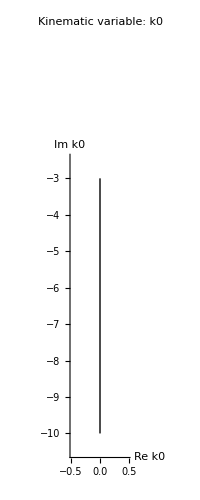

SeaSyde: Moving from the point k0=0.-3. ⅈ to k0=0.-10. ⅈ, along the line k0=(0.-7. ⅈ) tInt-(0.+3. ⅈ)

SeaSyde: The new point is: k0=0.-4.3233 ⅈ

SeaSyde: The new point is: k0=0.-6.00492 ⅈ

SeaSyde: The new point is: k0=0.-8.18614 ⅈ

SeaSyde: I arrived at k0=0.-10. ⅈ. The error estimate is: 1.38014×10^-13. The radius of convergence is: 3.44416.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

SeaSyde: Moving following these points: {2.6,8.2}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable k1

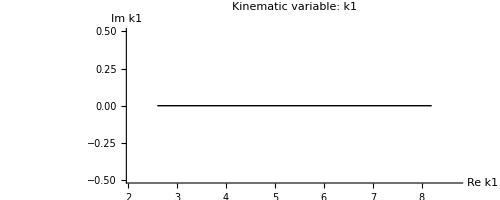

SeaSyde: Moving from the point k1=2.6 to k1=8.2, along the line k1=5.6 tInt+2.6

SeaSyde: The new point is: k1=3.46667

SeaSyde: The new point is: k1=4.62222

SeaSyde: The new point is: k1=6.16296

SeaSyde: I arrived at k1=8.2. The error estimate is: 1.38014×10^-13. The radius of convergence is: 2.73333.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

Logarithmic expansion time: 40.5044

(0.0000301255452406986003061444770424533099054030343982913770339543930481453434822203609046574315845304838895863280663257416922281201405376931959061093987844936488526368463452314730675104911381197667250308352073681020988196249382789747579908941013617007865+0.00007577201975500754528392260898248378817494372454162588562704281101082921146261979530348333266849271149999420538886156318571481632775309818205102894275425353491315716641543604828826847779733270014472215199794105369407021086037687865336864058452326246732 ⅈ
-0.00008366556509766477232281544706747028225386734260890438126279469089138588235047037068956066483556311857181795818353694040662197742839186343818797943372147733808136591496460391739344485200859542868759912451882208062682605462427461734951599991047585094978+0.0000117633847993540329581234658216666675689180538123596085479533066985555813225489741318590823498395720510675621156588621759936079088049213866216898274719375753164175097096105213544393011161547774521353607555876754252583025154928975148979976582333475458 ⅈ)

```mathematica
res1=AbsoluteTiming[
TransportBoundaryConditions[repN2[[;;,2]]]
];
Print[Style["Logarithmic expansion time: "<>ToString[res1[[1]]],Red]]
solLog=SolutionTable[]
```

```mathematica
(solLog//Transpose//Flatten )- intsBC2
```

{2.478794532023424386×10^-15-5.487612493021756827×10^-15 ⅈ,2.233481288029886361×10^-15+3.106566599158104763×10^-15 ⅈ}

## pp mm

```mathematica
test1=Omegan[1]//repknuset[#,{k12,ks},{v0,v1}]&
test2=Omegan[1]//repknuset[#,{k34,ks},{v0,v1}]&
Omegapm=KroneckerProduct[test1,Sigman[1,1,0]]+KroneckerProduct[Sigman[1,1,0],test2]
```

(-ⅈ (v0+1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks)) | -ⅈ (v0-2 v1) (1/2 log(k12+ks)-1/2 log(k12-ks))
-ⅈ (v0+1) (1/2 log(k12-ks)-1/2 log(k12+ks)) | -((2 v1+1) log(ks))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks)))

(-ⅈ (v0+1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks)) | -ⅈ (v0-2 v1) (1/2 log(k34+ks)-1/2 log(k34-ks))
-ⅈ (v0+1) (1/2 log(k34-ks)-1/2 log(k34+ks)) | -((2 v1+1) log(ks))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks)))

(-ⅈ (v0+1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks))-ⅈ (v0+1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks)) | -ⅈ (v0-2 v1) (1/2 log(k34+ks)-1/2 log(k34-ks)) | -ⅈ (v0-2 v1) (1/2 log(k12+ks)-1/2 log(k12-ks)) | 0
-ⅈ (v0+1) (1/2 log(k34-ks)-1/2 log(k34+ks)) | -ⅈ (v0+1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks))-((2 v1+1) log(ks)) | 0 | -ⅈ (v0-2 v1) (1/2 log(k12+ks)-1/2 log(k12-ks))
-ⅈ (v0+1) (1/2 log(k12-ks)-1/2 log(k12+ks)) | 0 | -ⅈ (v0-2 v1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks))-ⅈ (v0+1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks))-((2 v1+1) log(ks)) | -ⅈ (v0-2 v1) (1/2 log(k34+ks)-1/2 log(k34-ks))
0 | -ⅈ (v0+1) (1/2 log(k12-ks)-1/2 log(k12+ks)) | -ⅈ (v0+1) (1/2 log(k34-ks)-1/2 log(k34+ks)) | -ⅈ (v0-2 v1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks))-2 (2 v1+1) log(ks))

```mathematica
D[Omegapm/.log->Log,k12]//Simplify
Export["./de/dk12_0.m",%];
D[Omegapm/.log->Log,k34]//Simplify
Export["./de/dk13_0.m",%];
D[Omegapm/.log->Log,ks]//Simplify
Export["./de/dks_0.m",%];
```

(-(k12 (v0+1))/(k12^2-ks^2) | 0 | (ⅈ ks (v0-2 v1))/((k12-ks) (k12+ks)) | 0
0 | -(k12 (v0+1))/(k12^2-ks^2) | 0 | (ⅈ ks (v0-2 v1))/((k12-ks) (k12+ks))
-(ⅈ ks (v0+1))/((k12-ks) (k12+ks)) | 0 | -(k12 (v0-2 v1))/(k12^2-ks^2) | 0
0 | -(ⅈ ks (v0+1))/((k12-ks) (k12+ks)) | 0 | -(k12 (v0-2 v1))/(k12^2-ks^2))

(-(k34 (v0+1))/(k34^2-ks^2) | (ⅈ ks (v0-2 v1))/((k34-ks) (k34+ks)) | 0 | 0
-(ⅈ ks (v0+1))/((k34-ks) (k34+ks)) | -(k34 (v0-2 v1))/(k34^2-ks^2) | 0 | 0
0 | 0 | -(k34 (v0+1))/(k34^2-ks^2) | (ⅈ ks (v0-2 v1))/((k34-ks) (k34+ks))
0 | 0 | -(ⅈ ks (v0+1))/((k34-ks) (k34+ks)) | -(k34 (v0-2 v1))/(k34^2-ks^2))

(-(ks (v0+1) (k12^2+k34^2-2 ks^2))/((k12-ks) (k12+ks) (ks-k34) (k34+ks)) | -(ⅈ k34 (v0-2 v1))/((k34-ks) (k34+ks)) | -(ⅈ k12 (v0-2 v1))/((k12-ks) (k12+ks)) | 0
(ⅈ k34 (v0+1))/((k34-ks) (k34+ks)) | (k12^2 (k34^2 (2 v1+1)-ks^2 (v0+1))-k34^2 ks^2 (v0+2 v1+2)+2 ks^4 (v0+1))/(ks (k12-ks) (k12+ks) (ks-k34) (k34+ks)) | 0 | -(ⅈ k12 (v0-2 v1))/((k12-ks) (k12+ks))
(ⅈ k12 (v0+1))/((k12-ks) (k12+ks)) | 0 | (k12^2 (k34^2 (2 v1+1)-ks^2 (v0+2 v1+2))+ks^2 (v0+1) (2 ks^2-k34^2))/(ks (ks-k12) (k12+ks) (k34-ks) (k34+ks)) | -(ⅈ k34 (v0-2 v1))/((k34-ks) (k34+ks))
0 | (ⅈ k12 (v0+1))/((k12-ks) (k12+ks)) | (ⅈ k34 (v0+1))/((k34-ks) (k34+ks)) | (k12^2 (k34^2 (4 v1+2)-ks^2 (v0+2 v1+2))-k34^2 ks^2 (v0+2 v1+2)+2 ks^4 (v0+1))/(ks (k12-ks) (k12+ks) (ks-k34) (k34+ks)))

## Numerical DE DiffExp ++ -- (not finished)

```mathematica
Quit[];
```

```mathematica
Get["~/Software/diffexp-master/DiffExp.m"]
SetDirectory[NotebookDirectory[]]
```

Loading DiffExp version 1.0.9

For questions, email: martijnhidding@outlook.com

For the latest version, see: https://gitlab.com/hiddingm/diffexp

/home/fbgroup/jiaqichen/000Work/000 Ads ds amp/dS DE

## p x m

```mathematica
Omegan[2]//repknuset[#,{k0,k1,k2},{v0,v1,v2}]&
```

```mathematica
({{-ⅈ (v0+1) (-1/4 ⅈ log(-, k1 k2+k0-ki(2))-1/4 ⅈ log(, k1 k2+k0-ki(2))-1/4 ⅈ log(-, k1 k2+k0+ki(2))-1/4 ⅈ log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v2) (-1/4 log(-, k1 k2+k0-ki(2))-1/4 log(, k1 k2+k0-ki(2))+1/4 log(-, k1 k2+k0+ki(2))+1/4 log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v1) (-1/4 log(-, k1 k2+k0-ki(2))+1/4 log(, k1 k2+k0-ki(2))-1/4 log(-, k1 k2+k0+ki(2))+1/4 log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v1-2 v2-1) (1/4 ⅈ log(-, k1 k2+k0-ki(2))-1/4 ⅈ log(, k1 k2+k0-ki(2))-1/4 ⅈ log(-, k1 k2+k0+ki(2))+1/4 ⅈ log(, k1 k2+k0+ki(2)))}, {-ⅈ (v0+1) (1/4 log(-, k1 k2+k0-ki(2))+1/4 log(, k1 k2+k0-ki(2))-1/4 log(-, k1 k2+k0+ki(2))-1/4 log(, k1 k2+k0+ki(2))), -((2 v2+1) log(ki(2)))-ⅈ (v0-2 v2) (-1/4 ⅈ log(-, k1 k2+k0-ki(2))-1/4 ⅈ log(, k1 k2+k0-ki(2))-1/4 ⅈ log(-, k1 k2+k0+ki(2))-1/4 ⅈ log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v1) (-1/4 ⅈ log(-, k1 k2+k0-ki(2))+1/4 ⅈ log(, k1 k2+k0-ki(2))+1/4 ⅈ log(-, k1 k2+k0+ki(2))-1/4 ⅈ log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v1-2 v2-1) (-1/4 log(-, k1 k2+k0-ki(2))+1/4 log(, k1 k2+k0-ki(2))-1/4 log(-, k1 k2+k0+ki(2))+1/4 log(, k1 k2+k0+ki(2)))}, {-ⅈ (v0+1) (1/4 log(-, k1 k2+k0-ki(2))-1/4 log(, k1 k2+k0-ki(2))+1/4 log(-, k1 k2+k0+ki(2))-1/4 log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v2) (-1/4 ⅈ log(-, k1 k2+k0-ki(2))+1/4 ⅈ log(, k1 k2+k0-ki(2))+1/4 ⅈ log(-, k1 k2+k0+ki(2))-1/4 ⅈ log(, k1 k2+k0+ki(2))), -((2 v1+1) log(, k1 k2))-ⅈ (v0-2 v1) (-1/4 ⅈ log(-, k1 k2+k0-ki(2))-1/4 ⅈ log(, k1 k2+k0-ki(2))-1/4 ⅈ log(-, k1 k2+k0+ki(2))-1/4 ⅈ log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v1-2 v2-1) (-1/4 log(-, k1 k2+k0-ki(2))-1/4 log(, k1 k2+k0-ki(2))+1/4 log(-, k1 k2+k0+ki(2))+1/4 log(, k1 k2+k0+ki(2)))}, {-ⅈ (v0+1) (1/4 ⅈ log(-, k1 k2+k0-ki(2))-1/4 ⅈ log(, k1 k2+k0-ki(2))-1/4 ⅈ log(-, k1 k2+k0+ki(2))+1/4 ⅈ log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v2) (1/4 log(-, k1 k2+k0-ki(2))-1/4 log(, k1 k2+k0-ki(2))+1/4 log(-, k1 k2+k0+ki(2))-1/4 log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v1) (1/4 log(-, k1 k2+k0-ki(2))+1/4 log(, k1 k2+k0-ki(2))-1/4 log(-, k1 k2+k0+ki(2))-1/4 log(, k1 k2+k0+ki(2))), -ⅈ (v0-2 v1-2 v2-1) (-1/4 ⅈ log(-, k1 k2+k0-ki(2))-1/4 ⅈ log(, k1 k2+k0-ki(2))-1/4 ⅈ log(-, k1 k2+k0+ki(2))-1/4 ⅈ log(, k1 k2+k0+ki(2)))-((2 v1+1) log(, k1 k2))-(2 v2+1) log(ki(2))}})
```

```mathematica
v01==p1+3/2+v1     v02==p2+3/2+v1
```

```mathematica
repvi
```

{v0→19/5,v1→ⅈ/3}

```mathematica
test1=Omegan[1]//repknuset[#,{ k0,k1},{v0,v1}]&
(*D[test1/.log->Log,t0]/.repvi//Simplify
Export["./deV/dt0_0.m",%];*)
D[test1/.log->Log,k0]/.repvi//Simplify
Export["./deV/dk0_0.m",%];
D[test1/.log->Log,k1]/.repvi//Simplify
Export["./deV/dk1_0.m",%];
```

(-ⅈ (v0+1) (-1/2 ⅈ log(k0-k1)-1/2 ⅈ log(k0+k1)) | -ⅈ (v0-2 v1) (1/2 log(k0+k1)-1/2 log(k0-k1))
-ⅈ (v0+1) (1/2 log(k0-k1)-1/2 log(k0+k1)) | -((2 v1+1) log(k1))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k0-k1)-1/2 ⅈ log(k0+k1)))

(-(12 k0)/(5 (k0^2-k1^2)) | ((8/3+(7 ⅈ)/5) k1)/(k0^2-k1^2)
(12 ⅈ k1)/(5 (k1^2-k0^2)) | -((7/5-(8 ⅈ)/3) k0)/(k0^2-k1^2))

((12 k1)/(5 (k0^2-k1^2)) | -((8/3+(7 ⅈ)/5) k0)/(k0^2-k1^2)
(12 ⅈ k0)/(5 (k0^2-k1^2)) | -(-36 k1^2+(15+40 ⅈ) k0^2)/(15 k0^2 k1-15 k1^3))

```mathematica
Configuration={
AccuracyGoal->30,
EpsilonOrder->0,
ExpansionOrder->50,
DeltaPrescriptions->{(*k0+ⅈ δ,k1+ⅈ δ*)},
MatrixDirectory->"./deV",
Verbosity->1,
(*UseMobius->True,
UsePade->True,*)
WorkingPrecision->250,(*精度不足时下面计算会报错或结果错误！！！原因未知 AccuracyGoal->30时建议至少设成150 100*)
ChopPrecision->200
};
LoadConfiguration[Configuration];
```

DiffExp: Loading matrices.

DiffExp: Found files: {dk0_0.m,dk1_0.m}

DiffExp: Kinematic invariants and masses: {k0,k1}

DiffExp: Loaded system of size 2 x 2

DiffExp: Getting irreducible factors..

DiffExp: Configuration updated.

```mathematica
repN1//InputForm
```

{k0 -> -3*I, k1 -> 13/5}

```mathematica
BoundaryValuesX0=intsBC1
X0=repN1
Xiv[0](*v for value*)=PrepareBoundaryConditions[BoundaryValuesX0,X0]
```

{-0.401602400578613668018084633301-0.27443994393140818336326255501 ⅈ,0.0579278017263450875047214839995-0.024609914310196075925061989856 ⅈ}

{k0→-3 ⅈ,k1→3/5}

{<|k0→-3 ⅈ,k1→3/5|>,(-0.401602400578613668018084633301-0.27443994393140818336326255501 ⅈ
0.0579278017263450875047214839995-0.024609914310196075925061989856 ⅈ)}

```mathematica
(*注意！错误的积分路径会导致结果错误*)
```

### Set Path

```mathematica
{repN1,repN2}
Xi={(*<|k0->-3 I,k1->41/5|>,*)repN2}
```

{{k0→-3 ⅈ,k1→3/5},{k0→-10 ⅈ,k1→7/5}}

{{k0→-10 ⅈ,k1→7/5}}

### run

```mathematica
Do[Xiv[i]=TransportTo[Xiv[i-1],Xi[[i]]],{i,Length[Xi]}]
```

DiffExp: Transporting boundary conditions along <|k0→(0.-7. ⅈ) x-(0.+3. ⅈ),k1→0.8 x+0.6|> from x = 0. to x = 1.

DiffExp: Preparing differential equations along current line..

DiffExp: Determining positions of singularities and branch-cuts.

DiffExp: Possible singularities along line at positions {}.

DiffExp: Analyzing integration segments.

DiffExp: Segments to integrate: 3.

DiffExp: Integrating segment: <|k0→3. ((0.-0.92506 ⅈ) x-(0.+1. ⅈ)),k1→0.317164 x+0.6|>.

DiffExp: Evaluating at x = 0.132151

DiffExp: Integrated segment 1 out of 3 in 0.939963 seconds.

DiffExp: Current segment error estimate: 3.79245×10^-37

DiffExp: Total error estimate: 4.86418×10^-31

DiffExp: Integrating segment: <|k0→5.77518 ((0.-0.961072 ⅈ) x-(0.+1. ⅈ)),k1→0.634327 x+0.917164|>.

DiffExp: Evaluating at x = 0.660757

DiffExp: Integrated segment 2 out of 3 in 0.985669 seconds.

DiffExp: Current segment error estimate: 1.27788×10^-33

DiffExp: Total error estimate: 4.87696×10^-31

DiffExp: Integrating segment: <|k0→11.3255 ((0.-0.980149 ⅈ) x-(0.+1. ⅈ)),k1→1.55149 (0.8177 x+1.)|>.

DiffExp: Evaluating at x = 1.

DiffExp: Integrated segment 3 out of 3 in 1.26488 seconds.

DiffExp: Current segment error estimate: 1.34176×10^-35

DiffExp: Total error estimate: 4.87709×10^-31

DiffExp: Finished integration of 3 segments in 3.21842 seconds.

### check

```mathematica
result=Xiv[Length[Xi]][[2]]//Flatten
result-intsBC2
```

{-0.02287159889625575161500697126268205640707993277409423931799020397533624363651863129556514395768357385959137400311290601418845981714466393810091827219673482964698107469498095418492354228791649467694654750033018233354882384528719111166764539813604757373-0.01507443834777156103173931564096816436231265581507426167055577852327942749246970052408082910536649557466627942106064132265498375989768499769344762888529117792459966816420439995096175795995766328873034568941327669008968077963438165004501014437878545269 ⅈ,0.002390794773625270569948198922664207642871077510582986081435952684310579870869475764785331553519014087901556187536106166006477624422558893914551144049485611878085671712687412553079894136817002001970428991605382804587036609286690057797515247871486287722-0.001487215487996385236199619727301615937347551260706138883461540523535292032546948196165707613534383283041992584188049121324739603389726314320198749285053329579339331813192499782381148607778454814642707873890722276905023462466251433745055480470601379127 ⅈ}

{-3.×10^-31+9.×10^-31 ⅈ,-8.5×10^-31-3.5×10^-31 ⅈ}

## pp mm

```mathematica
test1=Omegan[1]//repknuset[#,{k12,ks},{v0,v1}]&
test2=Omegan[1]//repknuset[#,{k34,ks},{v0,v1}]&
Omegapm=KroneckerProduct[test1,Sigman[1,1,0]]+KroneckerProduct[Sigman[1,1,0],test2]
```

(-ⅈ (v0+1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks)) | -ⅈ (v0-2 v1) (1/2 log(k12+ks)-1/2 log(k12-ks))
-ⅈ (v0+1) (1/2 log(k12-ks)-1/2 log(k12+ks)) | -((2 v1+1) log(ks))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks)))

(-ⅈ (v0+1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks)) | -ⅈ (v0-2 v1) (1/2 log(k34+ks)-1/2 log(k34-ks))
-ⅈ (v0+1) (1/2 log(k34-ks)-1/2 log(k34+ks)) | -((2 v1+1) log(ks))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks)))

(-ⅈ (v0+1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks))-ⅈ (v0+1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks)) | -ⅈ (v0-2 v1) (1/2 log(k34+ks)-1/2 log(k34-ks)) | -ⅈ (v0-2 v1) (1/2 log(k12+ks)-1/2 log(k12-ks)) | 0
-ⅈ (v0+1) (1/2 log(k34-ks)-1/2 log(k34+ks)) | -ⅈ (v0+1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks))-((2 v1+1) log(ks)) | 0 | -ⅈ (v0-2 v1) (1/2 log(k12+ks)-1/2 log(k12-ks))
-ⅈ (v0+1) (1/2 log(k12-ks)-1/2 log(k12+ks)) | 0 | -ⅈ (v0-2 v1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks))-ⅈ (v0+1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks))-((2 v1+1) log(ks)) | -ⅈ (v0-2 v1) (1/2 log(k34+ks)-1/2 log(k34-ks))
0 | -ⅈ (v0+1) (1/2 log(k12-ks)-1/2 log(k12+ks)) | -ⅈ (v0+1) (1/2 log(k34-ks)-1/2 log(k34+ks)) | -ⅈ (v0-2 v1) (-1/2 ⅈ log(k12-ks)-1/2 ⅈ log(k12+ks))-ⅈ (v0-2 v1) (-1/2 ⅈ log(k34-ks)-1/2 ⅈ log(k34+ks))-2 (2 v1+1) log(ks))

```mathematica
D[Omegapm/.log->Log,k12]//Simplify
Export["./de/dk12_0.m",%];
D[Omegapm/.log->Log,k34]//Simplify
Export["./de/dk13_0.m",%];
D[Omegapm/.log->Log,ks]//Simplify
Export["./de/dks_0.m",%];
```

(-(k12 (v0+1))/(k12^2-ks^2) | 0 | (ⅈ ks (v0-2 v1))/((k12-ks) (k12+ks)) | 0
0 | -(k12 (v0+1))/(k12^2-ks^2) | 0 | (ⅈ ks (v0-2 v1))/((k12-ks) (k12+ks))
-(ⅈ ks (v0+1))/((k12-ks) (k12+ks)) | 0 | -(k12 (v0-2 v1))/(k12^2-ks^2) | 0
0 | -(ⅈ ks (v0+1))/((k12-ks) (k12+ks)) | 0 | -(k12 (v0-2 v1))/(k12^2-ks^2))

(-(k34 (v0+1))/(k34^2-ks^2) | (ⅈ ks (v0-2 v1))/((k34-ks) (k34+ks)) | 0 | 0
-(ⅈ ks (v0+1))/((k34-ks) (k34+ks)) | -(k34 (v0-2 v1))/(k34^2-ks^2) | 0 | 0
0 | 0 | -(k34 (v0+1))/(k34^2-ks^2) | (ⅈ ks (v0-2 v1))/((k34-ks) (k34+ks))
0 | 0 | -(ⅈ ks (v0+1))/((k34-ks) (k34+ks)) | -(k34 (v0-2 v1))/(k34^2-ks^2))

(-(ks (v0+1) (k12^2+k34^2-2 ks^2))/((k12-ks) (k12+ks) (ks-k34) (k34+ks)) | -(ⅈ k34 (v0-2 v1))/((k34-ks) (k34+ks)) | -(ⅈ k12 (v0-2 v1))/((k12-ks) (k12+ks)) | 0
(ⅈ k34 (v0+1))/((k34-ks) (k34+ks)) | (k12^2 (k34^2 (2 v1+1)-ks^2 (v0+1))-k34^2 ks^2 (v0+2 v1+2)+2 ks^4 (v0+1))/(ks (k12-ks) (k12+ks) (ks-k34) (k34+ks)) | 0 | -(ⅈ k12 (v0-2 v1))/((k12-ks) (k12+ks))
(ⅈ k12 (v0+1))/((k12-ks) (k12+ks)) | 0 | (k12^2 (k34^2 (2 v1+1)-ks^2 (v0+2 v1+2))+ks^2 (v0+1) (2 ks^2-k34^2))/(ks (ks-k12) (k12+ks) (k34-ks) (k34+ks)) | -(ⅈ k34 (v0-2 v1))/((k34-ks) (k34+ks))
0 | (ⅈ k12 (v0+1))/((k12-ks) (k12+ks)) | (ⅈ k34 (v0+1))/((k34-ks) (k34+ks)) | (k12^2 (k34^2 (4 v1+2)-ks^2 (v0+2 v1+2))-k34^2 ks^2 (v0+2 v1+2)+2 ks^4 (v0+1))/(ks (k12-ks) (k12+ks) (ks-k34) (k34+ks)))